# Quantum sensor HI

## Version. 2

## Updates: SNSPD case removed only DM-electron for clarity rearranged contents

## Settings

```mathematica
(* Directory *)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND

```mathematica
Direc=NotebookDirectory[]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/

## Constants

All parameters defined in terms of GeV

```mathematica
(* Default 10^9 *)
```

```mathematica
GeV=10^9;
```

### Units

```mathematica
(* eVs *)
```

```mathematica
eV=10^-9 GeV;
keV=10^-6 GeV;
MeV=10^-3 GeV;
```

```mathematica
(* Conversions *)
```

```mathematica
grams=5.62 10^23 GeV;
cm=(1.98 10^-14 GeV)^-1;
sec=(6.58 10^-25 GeV)^-1;
Kel=8.62 10^-14 GeV;
```

```mathematica
(* Mass *)
```

```mathematica
ng=10^-9*grams;
μg=10^-6*grams;
mg=10^-3*grams;
kg=10^3*grams;
me=0.5109989 MeV;
Mpl=1.22 10^19 GeV;
```

```mathematica
(* Length, Time *)
```

```mathematica
km=10^5 cm;
mtr=10^2 cm;
mic=μm=10^-4 cm;
nm=10^-7 cm;

yr=365*24*3600*sec;
month=yr/12;
day=24*3600*sec;
```

### Parameters

```mathematica
(* Halo velocity *)
```

```mathematica
kps=km/sec; (* km/s *)

(* from astro-ph/9710077v1 *)
v0=220 kps;
vemax= 241.279 kps;
vemin= 212.448 kps;
ve=(vemax+vemin)/2; (* earth speed *)

(* astro-ph/0611671 *)
vesc=544 kps;
```

```mathematica
(* particle *)
```

```mathematica
(* alpha *)
alpha=1/137;
(* DM density *)
ρDM=0.4 GeV/cm^3;
ρb=10^14 GeV/cm^3;
```

```mathematica
(* 1 Amu in kg, or ~0.9 GeV/kg *)
amukg=1.660538782 10^-27;
```

```mathematica
(* Material *)
```

```mathematica
rhoAl=2.7 grams/cm^3;
rhoTiN=5.4 grams/cm^3;
```

## Material Input

### TES

```mathematica
(* Al *)
(* Mermin Model *)
```

```mathematica
rhoAl=2.7 grams/cm^3;
mp=0.94 GeV;
AAl=27;
mAl=mp*AAl;
a0Al=4.046 10^-8 cm;
vLA=6.2kps;
```

```mathematica
(* dielectric function *)
```

```mathematica
datAl= Import["Al_mermin.dat"];
datLAl=Length[datAl];
```

```mathematica
eps1Aldat=ConstantArray[0,datLAl-1];
eps2Aldat=ConstantArray[0,datLAl-1];
ImepsAldat=ConstantArray[0,datLAl-1];
```

```mathematica
For[i=2,i≤datLAl,i++,
eps1Aldat[[i-1]]={{datAl[[i,1]],datAl[[i,2]]},datAl[[i,3]]}
];
For[i=2,i≤datLAl,i++,
eps2Aldat[[i-1]]={{datAl[[i,1]],datAl[[i,2]]},datAl[[i,4]]}
];
For[i=2,i≤datLAl,i++,
ImepsAldat[[i-1]]={{datAl[[i,1]],datAl[[i,2]]},datAl[[i,4]]/((datAl[[i,4]])^2+(datAl[[i,3]])^2)}
];
```

```mathematica
eps1AlIntpl=Interpolation[eps1Aldat,InterpolationOrder->1];
eps2AlIntpl=Interpolation[eps2Aldat,InterpolationOrder->1];
ImepsAlIntpl=Interpolation[ImepsAldat,InterpolationOrder->1];
```

```mathematica
ImepsAlf[w_,q_]:=If[(0<=w<=99.29999999999999716`18.996949248495383)&&(0<=q<=37289.5`18.57158656011924),ImepsAlIntpl[w,q],0]
eps2Alf[w_,q_]:=If[(0<=w<=99.29999999999999716`18.996949248495383)&&(0<=q<=37289.5`18.57158656011924),eps2AlIntpl[w,q],0]
eps1Alf[w_,q_]:=If[(0<=w<=99.29999999999999716`18.996949248495383)&&(0<=q<=37289.5`18.57158656011924),eps1AlIntpl[w,q],0]
```

```mathematica
(* phonon Fn(ω) *)
```

```mathematica
AlRawDos=Transpose[Delete[Import[FileNameJoin[Direc,"Al_pDoS.dat"]],1]];
Print[{AlRawDos[[1,1]],AlRawDos[[1,-1]]}]
DwAl=IntplArray[AlRawDos];
```

{0.,0.0419457982120051004}

```mathematica
wDw=AlRawDos[[1,-1]];
```

```mathematica
Dw[w_?NumericQ]:=Piecewise[{{DwAl[[1]][w],w<=wDw},{0,w>wDw}}]
```

```mathematica
AveOmg=NIntegrate[w*DwAl[[1]][w],{w,0.,0.04194579821200510039`18.622688463264012}]
AveInvOmg=NIntegrate[w^-1*DwAl[[1]][w],{w,0.,0.04194579821200510039`18.622688463264012}]
```

0.0255029

44.7577

```mathematica
AlRawFn=Transpose[Delete[Import[FileNameJoin[Direc,"Al_Fn.dat"]],1]];
Print[{AlRawFn[[1,1]],AlRawFn[[1,-1]]}]
FnwAl=IntplArray[AlRawFn];
```

{0.,0.209728991060025516}

```mathematica
Fnw10GeV1[w_]:=Piecewise[{{FnwAl[[1]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV2[w_]:=Piecewise[{{FnwAl[[2]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV3[w_]:=Piecewise[{{FnwAl[[3]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV4[w_]:=Piecewise[{{FnwAl[[4]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV5[w_]:=Piecewise[{{FnwAl[[5]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV6[w_]:=Piecewise[{{FnwAl[[6]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV7[w_]:=Piecewise[{{FnwAl[[7]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV8[w_]:=Piecewise[{{FnwAl[[8]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV9[w_]:=Piecewise[{{FnwAl[[9]][w],w<=0.2},{0,w>0.2}}]
Fnw10GeV10[w_]:=Piecewise[{{FnwAl[[10]][w],w<=0.2},{0,w>0.2}}]
```

```mathematica
Fnw10GeV={Fnw10GeV1,Fnw10GeV2,Fnw10GeV3,Fnw10GeV4,Fnw10GeV5,Fnw10GeV6,Fnw10GeV7,Fnw10GeV8,Fnw10GeV9,Fnw10GeV10}
```

{Fnw10GeV1,Fnw10GeV2,Fnw10GeV3,Fnw10GeV4,Fnw10GeV5,Fnw10GeV6,Fnw10GeV7,Fnw10GeV8,Fnw10GeV9,Fnw10GeV10}

### MKID

```mathematica
(* TiN *)
(* Lindhard Model *)
```

```mathematica
rhoTiN=5.4 grams/cm^3;
kFTiN=(2 me (3.94eV))^(1/2);
vFTiN=kFTiN/me;
wpTiN=((4Pi alpha)/me((2me(3.94eV))^(3/2)/(3 Pi^2)))^(1/2);
GammaTiN=0.1*(3.94eV);
```

```mathematica
ImepsLTiN[w_,q_]:=Im[-(1+(3(wpTiN)^2)/(q^2 vFTiN^2)(1/2+kFTiN/(4q)(1-(q/(2kFTiN)-(w+I*GammaTiN)/(q vFTiN))^2)Log[(q/(2kFTiN)-(w+I*GammaTiN)/(q vFTiN)+1)/(q/(2kFTiN)-(w+I*GammaTiN)/(q vFTiN)-1)]+kFTiN/(4q)(1-(q/(2kFTiN)+(w+I*GammaTiN)/(q vFTiN))^2)Log[(q/(2kFTiN)+(w+I*GammaTiN)/(q vFTiN)+1)/(q/(2kFTiN)+(w+I*GammaTiN)/(q vFTiN)-1)]))^-1]
```

## Functions

### Math

```mathematica
LIntpl1D[x1_,y1_]:=Module[{l1,Leng,loopvar},
Leng=Length[x1];
l1=ConstantArray[0,Leng];
For[loopvar=1,loopvar<=Leng,loopvar++,
l1[[loopvar]]={{x1[[loopvar]]},y1[[loopvar]]};
];
ListInterpolation[l1,InterpolationOrder->1]
]
```

```mathematica
IntplArray[m_]:=Module[{len,intpl,lv},
len=Length[m];
intpl=ConstantArray[0,len-1];
For[lv=1,lv<=len-1,lv++,
intpl[[lv]]=LIntpl1D[m[[1]],m[[lv+1]]];
];
intpl
]
```

### Utility

```mathematica
Inword[word_][a_][x_,y_][color_]:=Inset[Style[word,a,color,FontFamily->"Times"],ImageScaled[{x,y}],{Center,Center}];
```

## Defined for this project

## Functions

### Domain

```mathematica
μχt[mχ_,mt_]:=(mt*mχ)/(mt+mχ);  (*In eV/c^2*)
```

```mathematica
ql[Ee_][mχ_][vmin_]:=mχ*vmin-Sqrt[mχ^2*vmin^2-2mχ*Ee];
qr[Ee_][mχ_][vmin_]:=mχ*vmin+Sqrt[mχ^2*vmin^2-2mχ*Ee];
q0[Ee_][md_]:=Sqrt[2md*Ee];
```

```mathematica
Jacobl[Ee_][mχ_][vmin_]:=-(mχ-(mχ^2 vmin)/Sqrt[mχ^2 vmin^2-2mχ*Ee]);
Jacobr[Ee_][mχ_][vmin_]:=(mχ+(mχ^2 vmin)/Sqrt[mχ^2 vmin^2-2mχ*Ee]);
```

```mathematica
vmin[Ee_][mχ_][q_]:=(q/(2 mχ)+Ee/q);
vmin0[Ee_][md_]:=Sqrt[(2Ee)/md];
```

```mathematica
Eq[q_][md_][v_]:=q*v-q^2/(2md);
```

### FDM

```mathematica
FDM[q_][n_]:=((alpha me)/q)^n;
FmedH[md_][q_]:=(((md*240kps)^2+(100 md)^2)/(q^2+(100 md)^2));
FmedL[md_][q_]:=(((md*240kps)^2+0)/(q^2+0));
```

### η

```mathematica
(* for η *)
KKf[v0_,vesc_]:=v0^3(-2. Exp[-vesc^2/v0^2]π vesc/v0+π^(3/2)Erf[vesc/v0]);
```

```mathematica
(* η for halo, disk, bound DM *)
```

```mathematica
ηth[mχ_][vm_][v0_,ve_,vesc_]:=((ρDM*σe)/mχ)(v0^2 π)/(2 ve KKf[v0,vesc])*Piecewise[{{-4 Exp[-vesc^2/v0^2]ve+√π v0(Erf[(vm+ve)/v0]-Erf[(vm-ve)/v0]),vm<(vesc-ve)},{-2 Exp[-vesc^2/v0^2](ve+vesc-vm)+√π v0(Erf[vesc/v0]-Erf[(vm-ve)/v0]),vm<(vesc+ve)&&(vesc-ve)<vm},{0,vm>(vesc+ve)}}]
```

```mathematica
ηtd[mχ_][vm_][v0_,ve_,vesc_]:=((0.5*ρDM*σe)/mχ)(v0^2 π)/(2 ve KKf[v0,vesc])*Piecewise[{{-4 Exp[-vesc^2/v0^2]ve+√π v0(Erf[(vm+ve)/v0]-Erf[(vm-ve)/v0]),vm<(vesc-ve)},{-2 Exp[-vesc^2/v0^2](ve+vesc-vm)+√π v0(Erf[vesc/v0]-Erf[(vm-ve)/v0]),vm<(vesc+ve)&&(vesc-ve)<vm},{0,vm>(vesc+ve)}}]
```

```mathematica
ηtb[mχ_][vm_][v0_,vesc_]:=((ρb*σe)/mχ)*Piecewise[{{(v0^2/2)^-1*(Exp[-vm^2/v0^2]-Exp[-vesc^2/v0^2])*2π*v0^2,vm<=vesc},{0,vm>vesc}}]
```

```mathematica
(* conventional η *)
```

```mathematica
η[Ee_][mχ_][q_]:=(v0^2 π)/(2 ve KK)*Piecewise[{{-4 Exp[-vesc^2/v0^2]ve+√π v0(Erf[(vmin[Ee][mχ][q]+ve)/v0]-Erf[(vmin[Ee][mχ][q]-ve)/v0]),vmin[Ee][mχ][q]<(vesc-ve)},{-2 Exp[-vesc^2/v0^2](ve+vesc-vmin[Ee][mχ][q])+√π v0(Erf[vesc/v0]-Erf[(vmin[Ee][mχ][q]-ve)/v0]),vmin[Ee][mχ][q]<(vesc+ve)&&(vesc-ve)<vmin[Ee][mχ][q]},{0,vmin[Ee][mχ][q]>(vesc+ve)}}]
```

### Resolution

```mathematica
(* Box *)
```

```mathematica
cnt0=1;
G[E_][Ep_,sig_]:=cnt0/(2 sig)UnitBox[(E-Ep)/(2 sig)];
```

## Parameters

```mathematica
(* cross section *)
```

```mathematica
σe=10^-30 cm^2;
σN=10^-32 cm^2;
```

```mathematica
(* resolution *)
```

```mathematica
TESsig=.068/.8/2.355
MKIDsig=0.3/2.355
```

0.0360934

0.127389

```mathematica
(* exposure *)
```

```mathematica
TiNexp=10^7 rhoTiN*(1 μm)*(50 μm)*(22 nm)*month
Alexp=(8200 ng)*month
```

1.33328×10^50

1.84056×10^49

## Calculation

## Response function

### defined functions

#### Al

```mathematica
kerRAll[E_][mχ_][n_][vmin_]:=If[Internal`RealValuedNumericQ[ql[E][mχ][vmin]],(1/rhoAl 1/(8 π^2 alpha)1/(μχt[mχ,me])^2 Jacobl[E][mχ][vmin]*(ql[E][mχ][vmin])^3*(FDM[ql[E][mχ][vmin]][n])^2*ImepsAlf[E,ql[E][mχ][vmin]]),0];
kerRAlr[E_][mχ_][n_][vmin_]:=If[Internal`RealValuedNumericQ[qr[E][mχ][vmin]],(1/rhoAl 1/(8 π^2 alpha)1/(μχt[mχ,me])^2 Jacobr[E][mχ][vmin]*(qr[E][mχ][vmin])^3*(FDM[qr[E][mχ][vmin]][n])^2*ImepsAlf[E,qr[E][mχ][vmin]]),0];
```

```mathematica
RangeAlGen[vmin_][md_][Ep_][Sig_]:=Module[
{emax,emin},
emax=Min[1/2 md vmin^2,Ep+5*Sig];
emin=Max[0.1eV,Ep-5*Sig];
If[(emin<emax),{emin,emax},{0,0}]
];
```

```mathematica
IntkerRAll[E1_,E2_][mχ_][n_][Ep_,sig_][vmin_]:=Module[{tab,int},
tab=Table[PDF[NormalDistribution[Ep,sig],ER]*kerRAll[ER][mχ][n][vmin],{ER,E1,E2,0.001 eV}];
int=Total[tab]*.001eV
]
IntkerRAlr[E1_,E2_][mχ_][n_][Ep_,sig_][vmin_]:=Module[{tab,int},
tab=Table[PDF[NormalDistribution[Ep,sig],ER]*kerRAlr[ER][mχ][n][vmin],{ER,E1,E2,0.001 eV}];
int=Total[tab]*.001eV
]
```

```mathematica
KerRAll[md_][n_][Ep_,sig_][vmin_]:=Module[
{range,r1,r2},
range=RangeAlGen[vmin][md][Ep][sig];
r1=range[[1]];
r2=range[[2]];
If[(r1==0 &&r2==0),0,IntkerRAll[r1,r2][md][n][Ep,sig][vmin]]
]
KerRAlr[md_][n_][Ep_,sig_][vmin_]:=Module[
{range,r1,r2},
range=RangeAlGen[vmin][md][Ep][sig];
r1=range[[1]];
r2=range[[2]];
If[(r1==0 &&r2==0),0,IntkerRAlr[r1,r2][md][n][Ep,sig][vmin]]
]
```

#### TiN

```mathematica
kerRTiNl[E_][mχ_][n_][vmin_]:=If[Internal`RealValuedNumericQ[ql[E][mχ][vmin]],(1/rhoTiN 1/(8 π^2 alpha)1/(μχt[mχ,me])^2 Jacobl[E][mχ][vmin]*(ql[E][mχ][vmin])^3*(FDM[ql[E][mχ][vmin]][n])^2*ImepsLTiN[E,ql[E][mχ][vmin]]),0];
kerRTiNr[E_][mχ_][n_][vmin_]:=If[Internal`RealValuedNumericQ[qr[E][mχ][vmin]],(1/rhoTiN 1/(8 π^2 alpha)1/(μχt[mχ,me])^2 Jacobr[E][mχ][vmin]*(qr[E][mχ][vmin])^3*(FDM[qr[E][mχ][vmin]][n])^2*ImepsLTiN[E,qr[E][mχ][vmin]]),0];
```

```mathematica
RangeTiNGen[vmin_][md_][Ep_][Sig_]:=Module[
{emax,emin},
emax=Min[1/2 md vmin^2,Ep+5*Sig];
emin=Max[0.2eV,Ep-5*Sig];
If[(emin<emax),{emin,emax},{0,0}]
];
```

```mathematica
IntkerRTiNl[E1_,E2_][mχ_][n_][Ep_,sig_][vmin_]:=Module[{tab,int},
tab=Table[PDF[NormalDistribution[Ep,sig],ER]*kerRTiNl[ER][mχ][n][vmin],{ER,E1,E2,0.001 eV}];
int=Total[tab]*.001eV
]
IntkerRTiNr[E1_,E2_][mχ_][n_][Ep_,sig_][vmin_]:=Module[{tab,int},
tab=Table[PDF[NormalDistribution[Ep,sig],ER]*kerRTiNr[ER][mχ][n][vmin],{ER,E1,E2,0.001 eV}];
int=Total[tab]*.001eV
]
```

```mathematica
KerRTiNl[md_][n_][Ep_,sig_][vmin_]:=Module[
{range,r1,r2},
range=RangeTiNGen[vmin][md][Ep][sig];
r1=range[[1]];
r2=range[[2]];
If[(r1==0 &&r2==0),0,IntkerRTiNl[r1,r2][md][n][Ep,sig][vmin]]
]
KerRTiNr[md_][n_][Ep_,sig_][vmin_]:=Module[
{range,r1,r2},
range=RangeTiNGen[vmin][md][Ep][sig];
r1=range[[1]];
r2=range[[2]];
If[(r1==0 &&r2==0),0,IntkerRTiNr[r1,r2][md][n][Ep,sig][vmin]]
]
```

### plot

```mathematica
(* function format *)
```

KerR(material) (left/right branch)[DM mass][heavy/light][threshold, uncertainty][vmin]

#### Al

```mathematica
AbsoluteTiming[K0AlM10=Plot[
{
(KerRAll[10MeV][0][0.1,TESsig*.1][vmin kps]+KerRAlr[10 MeV][0][0.1,TESsig*.1][vmin kps])*kg/10^22/1/.11,
(KerRAll[10 MeV][0][1,TESsig*1][vmin kps]+KerRAlr[10 MeV][0][1,TESsig*1][vmin kps])*kg/10^22/1/3.81/1.44}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K2AlM10=Plot[
{
(KerRAll[10MeV][2][0.1,TESsig*.1][vmin kps]+KerRAlr[10 MeV][2][0.1,TESsig*.1][vmin kps])*kg/10^22/1/.83,
(KerRAll[10 MeV][2][1,TESsig*1][vmin kps]+KerRAlr[10 MeV][2][1,TESsig*1][vmin kps])*kg/10^22/1/2.3}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K0AlM100=Plot[
{
(KerRAll[100MeV][0][0.1,TESsig*.1][vmin kps]+KerRAlr[100 MeV][0][0.1,TESsig*.1][vmin kps])*kg/10^22/4.33,
(KerRAll[100 MeV][0][1,TESsig*1][vmin kps]+KerRAlr[100 MeV][0][1,TESsig*1][vmin kps])*kg/10^22/4.2/.93}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K2AlM100=Plot[
{
(KerRAll[100MeV][2][0.1,TESsig*.1][vmin kps]+KerRAlr[100 MeV][2][0.1,TESsig*.1][vmin kps])*kg/10^22/1.84/.998,
(KerRAll[100 MeV][2][1,TESsig*1][vmin kps]+KerRAlr[100 MeV][2][1,TESsig*1][vmin kps])*kg/10^22/.51/.954}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K0AlM1000=Plot[
{
(KerRAll[1000 MeV][0][0.1,TESsig*.1][vmin kps]+KerRAlr[1000 MeV][0][0.1,TESsig*.1][vmin kps])*kg/10^22/3.83,
(KerRAll[1000 MeV][0][1,TESsig*1][vmin kps]+KerRAlr[1000 MeV][0][1,TESsig*1][vmin kps])*kg/10^22/3.92/.818}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K2AlM1000=Plot[
{
(KerRAll[1000 MeV][2][0.1,TESsig*.1][vmin kps]+KerRAlr[1000 MeV][2][0.1,TESsig*.1][vmin kps])*kg/10^22/.268/.998,
(KerRAll[1000 MeV][2][1,TESsig*1][vmin kps]+KerRAlr[1000 MeV][2][1,TESsig*1][vmin kps])*kg/10^22/.42/.997}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

#### TiN

```mathematica
AbsoluteTiming[K0TiNM10=Plot[
{
(KerRTiNl[10MeV][0][0.2,0.2*MKIDsig][vmin kps]+KerRTiNr[10 MeV][0][0.2,0.2*MKIDsig][vmin kps])*kg/10^22/.095/1.02/.997,
(KerRTiNl[10 MeV][0][1,1*MKIDsig][vmin kps]+KerRTiNr[10 MeV][0][1,1*MKIDsig][vmin kps])*kg/10^22/.92/.43/.99/.98/.997}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["MKID, heavy mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K0TiNM100=Plot[
{
(KerRTiNl[100MeV][0][0.2,0.2*MKIDsig][vmin kps]+KerRTiNr[100 MeV][0][0.2,0.2*MKIDsig][vmin kps])*kg/10^22/.185/1.04,
(KerRTiNl[100 MeV][0][1,1*MKIDsig][vmin kps]+KerRTiNr[100 MeV][0][1,1*MKIDsig][vmin kps])*kg/10^22/.247/.99/1.04}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["MKID, heavy mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K0TiNM1000=Plot[
{
(KerRTiNl[1000MeV][0][0.2,0.2*MKIDsig][vmin kps]+KerRTiNr[1000 MeV][0][0.2,0.2*MKIDsig][vmin kps])*kg/10^22/.145/1.06,
(KerRTiNl[1000 MeV][0][1,1*MKIDsig][vmin kps]+KerRTiNr[1000 MeV][0][1,1*MKIDsig][vmin kps])*kg/10^22/.234/1.04}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["MKID, heavy mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K2TiNM10=Plot[
{
(KerRTiNl[10MeV][2][0.2,0.2*MKIDsig][vmin kps]+KerRTiNr[10 MeV][2][0.2,0.2*MKIDsig][vmin kps])*kg/10^22/.663/.98,
(KerRTiNl[10 MeV][2][1,1*MKIDsig][vmin kps]+KerRTiNr[10 MeV][2][1,1*MKIDsig][vmin kps])*kg/10^22/.637/1.02}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["MKID, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K2TiNM100=Plot[
{
(KerRTiNl[100MeV][2][0.2,0.2*MKIDsig][vmin kps]+KerRTiNr[100 MeV][2][0.2,0.2*MKIDsig][vmin kps])*kg/10^22/.241/1.03,
(KerRTiNl[100 MeV][2][1,1*MKIDsig][vmin kps]+KerRTiNr[100 MeV][2][1,1*MKIDsig][vmin kps])*kg/10^22/.382/1.02}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["MKID, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K2TiNM1000=Plot[
{
(KerRTiNl[1000MeV][2][0.2,0.2*MKIDsig][vmin kps]+KerRTiNr[1000 MeV][2][0.2,0.2*MKIDsig][vmin kps])*kg/10^22/.192/1.03,
(KerRTiNl[1000 MeV][2][1,1*MKIDsig][vmin kps]+KerRTiNr[1000 MeV][2][1,1*MKIDsig][vmin kps])*kg/10^22/.365/1.02}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["MKID, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

#### Result

```mathematica
(* Depends on how we want to combine the plots *)
```

```mathematica
(* Al,Heavy *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K0Al=Show[K0AlM10,K0AlM100,K0AlM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
(* Al,Light *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K2Al=Show[K2AlM10,K2AlM100,K2AlM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
(* TiN,Heavy *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K0TiN=Show[K0TiNM10,K0TiNM100,K0TiNM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
(* TiN,Light *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K2TiN=Show[K2TiNM10,K2TiNM100,K2TiNM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
Export[FileNameJoin[Direc,"Alq0.pdf"],K0Al]
Export[FileNameJoin[Direc,"Alq2.pdf"],K2Al]
```

```mathematica
Export[FileNameJoin[Direc,"TiNq0.pdf"],K0TiN]
Export[FileNameJoin[Direc,"TiNq2.pdf"],K2TiN]
```

### Matrix data

#### defined

```mathematica
(* Format *)
```

CRvm(material)[DM mass, heavy/light][E1, E2]

```mathematica
(* vm interval set to 1 km/s *)
(* reduce if necessary *)
```

```mathematica
CRvmTES[md_,n_][E1_,E2_]:=Module[{vm,Rlist,tab},
vm=1;
Rlist=ConstantArray[0,800];
While[vm<=800,
tab=Total[Table[.01eV*(KerRAll[md][n][w,TESsig*w][vm kps]+KerRAlr[md][n][w,TESsig*w][vm kps]),{w,E1,E2,.01}]];
Rlist[[vm]]=tab;
vm=vm+1;
];
Rlist
]
```

```mathematica
CRvmTiN[md_,n_][E1_,E2_]:=Module[{vm,Rlist,tab},
vm=1;
Rlist=ConstantArray[0,800];
While[vm<=800,
tab=Total[Table[.01eV*(KerRTiNl[md][n][w,MKIDsig*w][vm kps]+KerRTiNr[md][n][w,MKIDsig*w][vm kps]),{w,E1,E2,.01}]];
Rlist[[vm]]=tab;
vm=vm+1;
];
Rlist
]
```

#### matrices

```mathematica
(* format *)
```

R(material)M(DM mass)q(heavy/light)Bin(#bin)

```mathematica
(* Repeat these for heavy/light, DM mass, or bin size if needed *)
```

```mathematica
(* Use different kernel for faster calculation *)
```

```mathematica
AbsoluteTiming[RAlM1q0Bin5={
CRvmTES[10 MeV,0][.1,.3],
CRvmTES[10 MeV,0][.3,.5],
CRvmTES[10 MeV,0][.5,.7],
CRvmTES[10 MeV,0][.7,.9],
CRvmTES[10 MeV,0][.9,1.1]}]
```

{1972.57,{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.53037×10^-18,3.61463×10^-18,6.58278×10^-18,9.53329×10^-18,1.34069×10^-17,1.8561×10^-17,2.82794×10^-17,3.12375×10^-17,3.66254×10^-17,4.68329×10^-17,5.61793×10^-17,6.55501×10^-17,7.73126×10^-17,9.18251×10^-17,1.08358×10^-16,1.35264×10^-16,1.46167×10^-16,1.68072×10^-16,1.91834×10^-16,2.20352×10^-16,2.48606×10^-16,2.75344×10^-16,3.24908×10^-16,3.55031×10^-16,3.90514×10^-16,4.45063×10^-16,4.96014×10^-16,5.48306×10^-16,6.00712×10^-16,6.49689×10^-16,7.09925×10^-16,7.53357×10^-16,7.7693×10^-16,7.96456×10^-16,8.0323×10^-16,8.1938×10^-16,8.38666×10^-16,8.59775×10^-16,8.81795×10^-16,9.04375×10^-16,9.27318×10^-16,9.50499×10^-16,9.73824×10^-16,9.97245×10^-16,1.02084×10^-15,1.04463×10^-15,1.06861×10^-15,1.09277×10^-15,1.11711×10^-15,1.14171×10^-15,1.1666×10^-15,1.19174×10^-15,1.21708×10^-15,1.24265×10^-15,1.26854×10^-15,1.29467×10^-15,1.32082×10^-15,1.34697×10^-15,1.37312×10^-15,1.39766×10^-15,1.41118×10^-15,1.40935×10^-15,1.38857×10^-15,1.34496×10^-15,1.27436×10^-15,1.18055×10^-15,1.06651×10^-15,9.31152×10^-16,7.75169×10^-16,6.14276×10^-16,4.70312×10^-16,3.52846×10^-16,2.68259×10^-16,2.20368×10^-16,1.93765×10^-16,1.71835×10^-16,1.53669×10^-16,1.40277×10^-16,1.32224×10^-16,1.2699×10^-16,1.22143×10^-16,1.17566×10^-16,1.13368×10^-16,1.09616×10^-16,1.05969×10^-16,1.0208×10^-16,9.79218×10^-17,9.36391×10^-17,8.93326×10^-17,8.50588×10^-17,8.08776×10^-17,7.68604×10^-17,7.31382×10^-17,6.99289×10^-17,6.71342×10^-17,6.4505×10^-17,6.20665×10^-17,5.98907×10^-17,5.8111×10^-17,5.66993×10^-17,5.53854×10^-17,5.41399×10^-17,5.29954×10^-17,5.2001×10^-17,5.11984×10^-17,5.04621×10^-17,4.97591×10^-17,4.91091×10^-17,4.85346×10^-17,4.80736×10^-17,4.76721×10^-17,4.72876×10^-17,4.69323×10^-17,4.66209×10^-17,4.63726×10^-17,4.61788×10^-17,4.59954×10^-17,4.58275×10^-17,4.56854×10^-17,4.55801×10^-17,4.55175×10^-17,4.54651×10^-17,4.54199×10^-17,4.53894×10^-17,4.53817×10^-17,4.54031×10^-17,4.54374×10^-17,4.54738×10^-17,4.55179×10^-17,4.55757×10^-17,4.56532×10^-17,4.57443×10^-17,4.58354×10^-17,4.59296×10^-17,4.60315×10^-17,4.61462×10^-17,4.6274×10^-17,4.6402×10^-17,4.65297×10^-17,4.66611×10^-17,4.68005×10^-17,4.69512×10^-17,4.71036×10^-17,4.72537×10^-17,4.74047×10^-17,4.756×10^-17,4.77234×10^-17,4.78923×10^-17,4.80571×10^-17,4.82206×10^-17,4.83859×10^-17,4.85563×10^-17,4.87339×10^-17,4.89086×10^-17,4.90799×10^-17,4.9251×10^-17,4.94248×10^-17,4.96045×10^-17,4.97862×10^-17,4.99621×10^-17,5.01361×10^-17,5.0311×10^-17,5.04898×10^-17,5.06737×10^-17,5.08529×10^-17,5.10279×10^-17,5.12023×10^-17,5.13788×10^-17,5.15602×10^-17,5.17421×10^-17,5.19172×10^-17,5.20902×10^-17,5.22637×10^-17,5.24406×10^-17,5.2622×10^-17,5.27979×10^-17,5.2969×10^-17,5.31393×10^-17,5.33115×10^-17,5.34885×10^-17,5.36657×10^-17,5.38355×10^-17,5.40028×10^-17,5.41707×10^-17,5.4342×10^-17,5.45179×10^-17,5.46885×10^-17,5.48534×10^-17,5.50177×10^-17,5.51841×10^-17,5.53556×10^-17,5.55279×10^-17,5.56927×10^-17,5.58545×10^-17,5.60174×10^-17,5.61842×10^-17,5.63565×10^-17,5.65243×10^-17,5.66858×10^-17,5.6847×10^-17,5.70112×10^-17,5.71817×10^-17,5.73545×10^-17,5.75202×10^-17,5.76827×10^-17,5.78474×10^-17,5.80179×10^-17,5.81964×10^-17,5.8372×10^-17,5.85412×10^-17,5.87115×10^-17,5.88874×10^-17,5.90734×10^-17,5.92658×10^-17,5.94523×10^-17,5.96362×10^-17,5.98266×10^-17,6.00291×10^-17,6.02478×10^-17,6.0468×10^-17,6.06829×10^-17,6.09042×10^-17,6.11427×10^-17,6.14067×10^-17,6.16929×10^-17,6.19771×10^-17,6.22638×10^-17,6.25842×10^-17,6.29575×10^-17,6.33996×10^-17,6.38706×10^-17,6.43416×10^-17,6.48309×10^-17,6.53667×10^-17,6.59678×10^-17,6.66343×10^-17,6.73123×10^-17,6.79898×10^-17,6.86154×10^-17,6.91477×10^-17,6.95543×10^-17,6.98922×10^-17,7.0226×10^-17,7.05602×10^-17,7.09079×10^-17,7.12771×10^-17,7.16707×10^-17,7.20668×10^-17,7.24598×10^-17,7.2792×10^-17,7.2993×10^-17,7.30122×10^-17,7.29041×10^-17,7.27804×10^-17,7.26411×10^-17,7.2467×10^-17,7.22439×10^-17,7.19636×10^-17,7.16564×10^-17,7.1333×10^-17,7.10211×10^-17,7.07876×10^-17,7.0675×10^-17,7.06635×10^-17,7.06487×10^-17,7.06245×10^-17,7.06011×10^-17,7.05887×10^-17,7.05942×10^-17,7.06012×10^-17,7.05993×10^-17,7.05885×10^-17,7.05691×10^-17,7.05415×10^-17,7.05055×10^-17,7.04601×10^-17,7.04053×10^-17,7.03433×10^-17,7.0279×10^-17,7.02153×10^-17,7.01477×10^-17,7.00704×10^-17,6.99837×10^-17,6.98907×10^-17,6.97946×10^-17,6.96966×10^-17,6.95903×10^-17,6.9474×10^-17,6.93459×10^-17,6.91983×10^-17,6.90263×10^-17,6.88329×10^-17,6.86279×10^-17,6.84116×10^-17,6.8166×10^-17,6.78637×10^-17,6.74888×10^-17,6.70806×10^-17,6.66579×10^-17,6.62146×10^-17,6.56867×10^-17,6.50196×10^-17,6.42139×10^-17,6.33772×10^-17,6.25193×10^-17,6.15844×10^-17,6.03914×10^-17,5.88231×10^-17,5.70466×10^-17,5.5233×10^-17,5.33847×10^-17,5.16645×10^-17,5.02871×10^-17,4.93299×10^-17,4.84297×10^-17,4.75094×10^-17,4.65852×10^-17,4.57857×10^-17,4.52145×10^-17,4.48116×10^-17,4.44019×10^-17,4.39813×10^-17,4.35844×10^-17,4.33048×10^-17,4.31941×10^-17,4.31331×10^-17,4.3067×10^-17,4.29957×10^-17,4.29094×10^-17,4.27967×10^-17,4.2657×10^-17,4.25096×10^-17,4.23561×10^-17,4.21986×10^-17,4.20516×10^-17,4.19256×10^-17,4.18079×10^-17,4.16848×10^-17,4.15562×10^-17,4.14277×10^-17,4.13125×10^-17,4.12153×10^-17,4.11174×10^-17,4.10145×10^-17,4.0907×10^-17,4.08021×10^-17,4.07078×10^-17,4.06209×10^-17,4.05296×10^-17,4.04337×10^-17,4.0334×10^-17,4.02356×10^-17,4.01415×10^-17,4.0046×10^-17,3.99458×10^-17,3.9841×10^-17,3.97308×10^-17,3.96141×10^-17,3.94905×10^-17,3.93619×10^-17,3.92284×10^-17,3.9089×10^-17,3.89308×10^-17,3.87412×10^-17,3.85305×10^-17,3.83138×10^-17,3.8091×10^-17,3.78465×10^-17,3.7514×10^-17,3.70603×10^-17,3.65724×10^-17,3.60747×10^-17,3.55672×10^-17,3.50983×10^-17,3.47487×10^-17,3.45067×10^-17,3.42633×10^-17,3.4014×10^-17,3.37619×10^-17,3.35435×10^-17,3.3391×10^-17,3.32631×10^-17,3.31312×10^-17,3.29952×10^-17,3.28604×10^-17,3.27464×10^-17,3.26595×10^-17,3.25732×10^-17,3.24835×10^-17,3.23905×10^-17,3.23013×10^-17,3.22266×10^-17,3.21614×10^-17,3.20933×10^-17,3.20223×10^-17,3.19489×10^-17,3.18803×10^-17,3.18217×10^-17,3.17639×10^-17,3.17033×10^-17,3.16399×10^-17,3.15755×10^-17,3.15159×10^-17,3.14617×10^-17,3.14053×10^-17,3.13463×10^-17,3.12845×10^-17,3.12231×10^-17,3.11658×10^-17,3.11095×10^-17,3.10505×10^-17,3.09889×10^-17,3.09251×10^-17,3.08619×10^-17,3.08011×10^-17,3.07387×10^-17,3.06737×10^-17,3.0606×10^-17,3.05363×10^-17,3.04665×10^-17,3.03963×10^-17,3.03235×10^-17,3.02481×10^-17,3.01699×10^-17,3.00887×10^-17,3.00041×10^-17,2.99165×10^-17,2.98262×10^-17,2.97329×10^-17,2.9636×10^-17,2.95294×10^-17,2.94108×10^-17,2.92881×10^-17,2.91622×10^-17,2.90331×10^-17,2.88899×10^-17,2.87058×10^-17,2.84912×10^-17,2.82722×10^-17,2.8049×10^-17,2.78224×10^-17,2.76158×10^-17,2.74525×10^-17,2.72992×10^-17,2.71425×10^-17,2.69825×10^-17,2.68213×10^-17,2.6671×10^-17,2.65342×10^-17,2.63954×10^-17,2.62536×10^-17,2.61087×10^-17,2.59623×10^-17,2.58178×10^-17,2.56729×10^-17,2.55251×10^-17,2.53742×10^-17,2.52201×10^-17,2.50627×10^-17,2.49014×10^-17,2.47369×10^-17,2.45692×10^-17,2.43983×10^-17,2.42235×10^-17,2.40415×10^-17,2.38522×10^-17,2.36595×10^-17,2.34633×10^-17,2.32636×10^-17,2.30572×10^-17,2.28377×10^-17,2.26105×10^-17,2.23795×10^-17,2.21448×10^-17,2.19056×10^-17,2.16526×10^-17,2.13795×10^-17,2.11×10^-17,2.08163×10^-17,2.05284×10^-17,2.02314×10^-17,1.9904×10^-17,1.95506×10^-17,1.91919×10^-17,1.88284×10^-17,1.84597×10^-17,1.8055×10^-17,1.75647×10^-17,1.70418×10^-17,1.65122×10^-17,1.59758×10^-17,1.54309×10^-17,1.48551×10^-17,1.42386×10^-17,1.36116×10^-17,1.29769×10^-17,1.23345×10^-17,1.17189×10^-17,1.12654×10^-17,1.09188×10^-17,1.05681×10^-17,1.0213×10^-17,9.85383×10^-18,9.5191×10^-18,9.24796×10^-18,8.99024×10^-18,8.72932×10^-18,8.46516×10^-18,8.20039×10^-18,7.96267×10^-18,7.75916×10^-18,7.55502×10^-18,7.34835×10^-18,7.13914×10^-18,6.93397×10^-18,6.7558×10^-18,6.59112×10^-18,6.4244×10^-18,6.25563×10^-18,5.78869×10^-18,2.46477×10^-18,7.54098×10^-24,7.4626×10^-24,7.38518×10^-24,7.3087×10^-24,7.23315×10^-24,7.15852×10^-24,7.08479×10^-24,7.01195×10^-24,6.94×10^-24,6.86891×10^-24,6.79867×10^-24,6.72928×10^-24,6.66072×10^-24,6.59298×10^-24,6.52605×10^-24,6.45992×10^-24,6.39457×10^-24,6.33×10^-24,6.2662×10^-24,6.20315×10^-24,6.14085×10^-24,6.07928×10^-24,6.01844×10^-24,5.95831×10^-24,5.89889×10^-24,5.84016×10^-24,5.78212×10^-24,5.72476×10^-24,5.66807×10^-24,5.61203×10^-24,5.55665×10^-24,5.50191×10^-24,5.4478×10^-24,5.39432×10^-24,5.34145×10^-24,5.28919×10^-24,5.23754×10^-24,5.18647×10^-24,5.13599×10^-24,5.08609×10^-24,5.03676×10^-24,4.98799×10^-24,4.93977×10^-24,4.8921×10^-24,4.84497×10^-24,4.79838×10^-24,4.75231×10^-24,4.70676×10^-24,4.66173×10^-24,4.6172×10^-24,4.57317×10^-24,4.52963×10^-24,4.48658×10^-24,4.44401×10^-24,4.40192×10^-24,4.36029×10^-24,4.31913×10^-24,4.27842×10^-24,4.23816×10^-24,4.19835×10^-24,4.15898×10^-24,4.12004×10^-24,4.08153×10^-24,4.04344×10^-24,4.00577×10^-24,3.96852×10^-24,3.93167×10^-24,3.89522×10^-24,3.85917×10^-24,3.82351×10^-24,3.78824×10^-24,3.75335×10^-24,3.71884×10^-24,3.6847×10^-24,3.65093×10^-24,3.61752×10^-24,3.58447×10^-24,3.55178×10^-24,3.51944×10^-24,3.48744×10^-24,3.45579×10^-24,3.42447×10^-24,3.39349×10^-24,3.36283×10^-24,3.33251×10^-24,3.3025×10^-24,3.27281×10^-24,3.24343×10^-24,3.21437×10^-24,3.18561×10^-24,3.15715×10^-24,3.12899×10^-24,3.10113×10^-24,3.07355×10^-24,3.04627×10^-24,3.01927×10^-24,2.99255×10^-24,2.96611×10^-24,2.93995×10^-24,2.91405×10^-24,2.88843×10^-24,2.86307×10^-24,2.83797×10^-24,2.81312×10^-24,2.78854×10^-24,2.76421×10^-24,2.74012×10^-24,2.71629×10^-24,2.69269×10^-24,2.66934×10^-24,2.64623×10^-24,2.62335×10^-24,2.6007×10^-24,2.57829×10^-24,2.5561×10^-24,2.53413×10^-24,2.51239×10^-24,2.49086×10^-24,2.46956×10^-24,2.44846×10^-24,2.42758×10^-24,2.40691×10^-24,2.38645×10^-24,2.36619×10^-24,2.34613×10^-24,2.32627×10^-24,2.30661×10^-24,2.28715×10^-24,2.26787×10^-24,2.24879×10^-24,2.2299×10^-24,2.21119×10^-24,2.19267×10^-24,2.17433×10^-24,2.15618×10^-24,2.1382×10^-24,2.12039×10^-24,2.10276×10^-24,2.0853×10^-24,2.06802×10^-24,2.0509×10^-24,2.03395×10^-24,2.01716×10^-24,2.00054×10^-24,1.98407×10^-24,1.96777×10^-24,1.95162×10^-24,1.93563×10^-24,1.9198×10^-24,1.90411×10^-24,1.88858×10^-24,1.87319×10^-24,1.85796×10^-24,1.84287×10^-24,1.82792×10^-24,1.81311×10^-24,1.79845×10^-24,1.78393×10^-24,1.76954×10^-24,1.75529×10^-24,1.74117×10^-24,1.72719×10^-24,1.71334×10^-24,1.69963×10^-24,1.68604×10^-24,1.67257×10^-24,1.65924×10^-24,1.64603×10^-24,1.63294×10^-24,1.61998×10^-24,1.60713×10^-24,1.59441×10^-24,1.5818×10^-24,1.56932×10^-24,1.55695×10^-24,1.54469×10^-24,1.53254×10^-24,1.52051×10^-24,1.50859×10^-24,1.49678×10^-24,1.48508×10^-24,1.47349×10^-24,1.462×10^-24,1.45062×10^-24,1.43934×10^-24,1.42816×10^-24,1.41709×10^-24,1.40612×10^-24,1.39525×10^-24,1.38447×10^-24,1.3738×10^-24,1.36322×10^-24,1.35274×10^-24,1.34235×10^-24,1.33206×10^-24,1.32185×10^-24,1.31175×10^-24,1.30173×10^-24,1.2918×10^-24,1.28196×10^-24,1.27221×10^-24,1.26254×10^-24,1.25297×10^-24,1.24348×10^-24,1.23407×10^-24,1.22474×10^-24,1.2155×10^-24,1.20634×10^-24,1.19727×10^-24,1.18827×10^-24,1.17935×10^-24,1.17051×10^-24,1.16175×10^-24,1.15307×10^-24,1.14446×10^-24,1.13593×10^-24,1.12747×10^-24,1.11909×10^-24,1.11078×10^-24,1.10254×10^-24,1.09438×10^-24,1.08628×10^-24,1.07826×10^-24,1.07031×10^-24,1.06242×10^-24,1.0546×10^-24,1.04686×10^-24,1.03917×10^-24,1.03156×10^-24,1.02401×10^-24,1.01652×10^-24,1.0091×10^-24,1.00175×10^-24,9.94454×10^-25,9.87222×10^-25,9.80053×10^-25,9.72945×10^-25},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.97364×10^-22,2.09853×10^-21,9.15368×10^-20,3.47501×10^-19,2.99296×10^-18,1.61833×10^-17,5.15316×10^-17,1.01823×10^-16,1.63697×10^-16,2.31682×10^-16,3.08922×10^-16,3.91407×10^-16,4.56948×10^-16,5.51577×10^-16,6.73463×10^-16,7.75672×10^-16,8.52665×10^-16,1.08583×10^-15,1.11107×10^-15,1.31702×10^-15,1.37462×10^-15,1.61102×10^-15,1.69123×10^-15,1.88694×10^-15,2.08474×10^-15,2.66457×10^-15,2.53025×10^-15,2.63222×10^-15,2.71805×10^-15,2.82369×10^-15,2.78075×10^-15,2.76619×10^-15,2.7536×10^-15,2.75653×10^-15,2.77446×10^-15,2.80225×10^-15,2.83638×10^-15,2.8749×10^-15,2.9167×10^-15,2.961×10^-15,3.00742×10^-15,3.05569×10^-15,3.10536×10^-15,3.1557×10^-15,3.19986×10^-15,3.21431×10^-15,3.18381×10^-15,3.10108×10^-15,2.95913×10^-15,2.7593×10^-15,2.52147×10^-15,2.25205×10^-15,1.94984×10^-15,1.61796×10^-15,1.27855×10^-15,9.72538×10^-16,7.28061×10^-16,5.57233×10^-16,4.5576×10^-16,3.95022×10^-16,3.50315×10^-16,3.16256×10^-16,2.93018×10^-16,2.77883×10^-16,2.65858×10^-16,2.54747×10^-16,2.44403×10^-16,2.34758×10^-16,2.25225×10^-16,2.15271×10^-16,2.05116×10^-16,1.9503×10^-16,1.85106×10^-16,1.75425×10^-16,1.66098×10^-16,1.57501×10^-16,1.50019×10^-16,1.43546×10^-16,1.37661×10^-16,1.32238×10^-16,1.27443×10^-16,1.23509×10^-16,1.20264×10^-16,1.17313×10^-16,1.1455×10^-16,1.12039×10^-16,1.09923×10^-16,1.08129×10^-16,1.06474×10^-16,1.04922×10^-16,1.03509×10^-16,1.02317×10^-16,1.01321×10^-16,1.00406×10^-16,9.95556×10^-17,9.87882×10^-17,9.81483×10^-17,9.76382×10^-17,9.7181×10^-17,9.67641×10^-17,9.64002×10^-17,9.61103×10^-17,9.59081×10^-17,9.57428×10^-17,9.56028×10^-17,9.5497×10^-17,9.54363×10^-17,9.54328×10^-17,9.54571×10^-17,9.54969×10^-17,9.55586×10^-17,9.56497×10^-17,9.57764×10^-17,9.59246×10^-17,9.6082×10^-17,9.6253×10^-17,9.64438×10^-17,9.66573×10^-17,9.68863×10^-17,9.71206×10^-17,9.73629×10^-17,9.76182×10^-17,9.78897×10^-17,9.81708×10^-17,9.84547×10^-17,9.87427×10^-17,9.9039×10^-17,9.93475×10^-17,9.96624×10^-17,9.99775×10^-17,1.00294×10^-16,1.00615×10^-16,1.00945×10^-16,1.01282×10^-16,1.01616×10^-16,1.01949×10^-16,1.02284×10^-16,1.02626×10^-16,1.02975×10^-16,1.0332×10^-16,1.03661×10^-16,1.04003×10^-16,1.04349×10^-16,1.04702×10^-16,1.05053×10^-16,1.05398×10^-16,1.05741×10^-16,1.06087×10^-16,1.06438×10^-16,1.06793×10^-16,1.07138×10^-16,1.07479×10^-16,1.07821×10^-16,1.08168×10^-16,1.0852×10^-16,1.08866×10^-16,1.09203×10^-16,1.09541×10^-16,1.09881×10^-16,1.10227×10^-16,1.10573×10^-16,1.10907×10^-16,1.11238×10^-16,1.11571×10^-16,1.1191×10^-16,1.12253×10^-16,1.12587×10^-16,1.12913×10^-16,1.13239×10^-16,1.13571×10^-16,1.13909×10^-16,1.14245×10^-16,1.14567×10^-16,1.14889×10^-16,1.15215×10^-16,1.15547×10^-16,1.15885×10^-16,1.16212×10^-16,1.16531×10^-16,1.16854×10^-16,1.17184×10^-16,1.17524×10^-16,1.17861×10^-16,1.18185×10^-16,1.18511×10^-16,1.18844×10^-16,1.1919×10^-16,1.19543×10^-16,1.19885×10^-16,1.20222×10^-16,1.20569×10^-16,1.20931×10^-16,1.2131×10^-16,1.21688×10^-16,1.22055×10^-16,1.22433×10^-16,1.22831×10^-16,1.23256×10^-16,1.237×10^-16,1.24135×10^-16,1.24575×10^-16,1.25048×10^-16,1.25566×10^-16,1.26132×10^-16,1.26709×10^-16,1.27285×10^-16,1.27924×10^-16,1.28665×10^-16,1.29527×10^-16,1.3048×10^-16,1.31443×10^-16,1.32434×10^-16,1.33523×10^-16,1.34732×10^-16,1.36071×10^-16,1.37459×10^-16,1.3885×10^-16,1.40134×10^-16,1.41228×10^-16,1.42096×10^-16,1.42796×10^-16,1.43474×10^-16,1.44153×10^-16,1.44862×10^-16,1.45612×10^-16,1.46408×10^-16,1.47214×10^-16,1.48013×10^-16,1.48668×10^-16,1.4904×10^-16,1.49075×10^-16,1.48853×10^-16,1.48584×10^-16,1.48281×10^-16,1.47898×10^-16,1.47415×10^-16,1.46826×10^-16,1.46179×10^-16,1.45499×10^-16,1.44872×10^-16,1.44428×10^-16,1.44215×10^-16,1.44174×10^-16,1.44131×10^-16,1.4407×10^-16,1.44019×10^-16,1.43992×10^-16,1.43994×10^-16,1.43996×10^-16,1.43979×10^-16,1.43943×10^-16,1.43891×10^-16,1.43821×10^-16,1.43733×10^-16,1.43627×10^-16,1.435×10^-16,1.43364×10^-16,1.43224×10^-16,1.43083×10^-16,1.4293×10^-16,1.42757×10^-16,1.42565×10^-16,1.42365×10^-16,1.42158×10^-16,1.41944×10^-16,1.41711×10^-16,1.41457×10^-16,1.41171×10^-16,1.40842×10^-16,1.40463×10^-16,1.40049×10^-16,1.39612×10^-16,1.39143×10^-16,1.38581×10^-16,1.3789×10^-16,1.37077×10^-16,1.3622×10^-16,1.35332×10^-16,1.34348×10^-16,1.33121×10^-16,1.31603×10^-16,1.29906×10^-16,1.28163×10^-16,1.2636×10^-16,1.24166×10^-16,1.2133×10^-16,1.17836×10^-16,1.14149×10^-16,1.10385×10^-16,1.06677×10^-16,1.03546×10^-16,1.01201×10^-16,9.93482×10^-17,9.7476×10^-17,9.55645×10^-17,9.38048×10^-17,9.24347×10^-17,9.14995×10^-17,9.06654×10^-17,8.98091×10^-17,8.89534×10^-17,8.82918×10^-17,8.79268×10^-17,8.77863×10^-17,8.76514×10^-17,8.75062×10^-17,8.7339×10^-17,8.71229×10^-17,8.68506×10^-17,8.65499×10^-17,8.62366×10^-17,8.59117×10^-17,8.56014×10^-17,8.53263×10^-17,8.50814×10^-17,8.48298×10^-17,8.4567×10^-17,8.42991×10^-17,8.4054×10^-17,8.38425×10^-17,8.36419×10^-17,8.34313×10^-17,8.32107×10^-17,8.29917×10^-17,8.27907×10^-17,8.26084×10^-17,8.24214×10^-17,8.22248×10^-17,8.20196×10^-17,8.18156×10^-17,8.16186×10^-17,8.14223×10^-17,8.12169×10^-17,8.1002×10^-17,8.07765×10^-17,8.05379×10^-17,8.02854×10^-17,8.0022×10^-17,7.97484×10^-17,7.94639×10^-17,7.91435×10^-17,7.87642×10^-17,7.83356×10^-17,7.78923×10^-17,7.74367×10^-17,7.69439×10^-17,7.62769×10^-17,7.53808×10^-17,7.43849×10^-17,7.33687×10^-17,7.23325×10^-17,7.13683×10^-17,7.06338×10^-17,7.01199×10^-17,6.96222×10^-17,6.91124×10^-17,6.85956×10^-17,6.81494×10^-17,6.78243×10^-17,6.75612×10^-17,6.72907×10^-17,6.70117×10^-17,6.67358×10^-17,6.65026×10^-17,6.63199×10^-17,6.61423×10^-17,6.59579×10^-17,6.57667×10^-17,6.55848×10^-17,6.54307×10^-17,6.52954×10^-17,6.5155×10^-17,6.50085×10^-17,6.48577×10^-17,6.4718×10^-17,6.45963×10^-17,6.44769×10^-17,6.43518×10^-17,6.42209×10^-17,6.4089×10^-17,6.39672×10^-17,6.38546×10^-17,6.37381×10^-17,6.3616×10^-17,6.34887×10^-17,6.33632×10^-17,6.32453×10^-17,6.31288×10^-17,6.30069×10^-17,6.28796×10^-17,6.27482×10^-17,6.26191×10^-17,6.24937×10^-17,6.23647×10^-17,6.22304×10^-17,6.20906×10^-17,6.19475×10^-17,6.18043×10^-17,6.16594×10^-17,6.15092×10^-17,6.13536×10^-17,6.11925×10^-17,6.1025×10^-17,6.08506×10^-17,6.06702×10^-17,6.04841×10^-17,6.02922×10^-17,6.0091×10^-17,5.98681×10^-17,5.96237×10^-17,5.93716×10^-17,5.9113×10^-17,5.88475×10^-17,5.85392×10^-17,5.8147×10^-17,5.77073×10^-17,5.72587×10^-17,5.68014×10^-17,5.63425×10^-17,5.59411×10^-17,5.56169×10^-17,5.53024×10^-17,5.4981×10^-17,5.46528×10^-17,5.43276×10^-17,5.4029×10^-17,5.37494×10^-17,5.34646×10^-17,5.31736×10^-17,5.28765×10^-17,5.25787×10^-17,5.22843×10^-17,5.19872×10^-17,5.16839×10^-17,5.13743×10^-17,5.10583×10^-17,5.0735×10^-17,5.04042×10^-17,5.00669×10^-17,4.97231×10^-17,4.93728×10^-17,4.90125×10^-17,4.86365×10^-17,4.82484×10^-17,4.78534×10^-17,4.74515×10^-17,4.70419×10^-17,4.66132×10^-17,4.61594×10^-17,4.5694×10^-17,4.52211×10^-17,4.47406×10^-17,4.42467×10^-17,4.37167×10^-17,4.31545×10^-17,4.25826×10^-17,4.20021×10^-17,4.14129×10^-17,4.07893×10^-17,4.00987×10^-17,3.93754×10^-17,3.8642×10^-17,3.78984×10^-17,3.7135×10^-17,3.62491×10^-17,3.52119×10^-17,3.4143×10^-17,3.30605×10^-17,3.19643×10^-17,3.08375×10^-17,2.96304×10^-17,2.83653×10^-17,2.7084×10^-17,2.57872×10^-17,2.44777×10^-17,2.33423×10^-17,2.25487×10^-17,2.18407×10^-17,2.11239×10^-17,2.03982×10^-17,1.96764×10^-17,1.90501×10^-17,1.85225×10^-17,1.79957×10^-17,1.74624×10^-17,1.69224×10^-17,1.64013×10^-17,1.59553×10^-17,1.5543×10^-17,1.51256×10^-17,1.47031×10^-17,1.42767×10^-17,1.38818×10^-17,1.35393×10^-17,1.32027×10^-17,1.28618×10^-17,1.25168×10^-17,8.79089×10^-18,1.17999×10^-18,2.3769×10^-22,2.35196×10^-22,2.32732×10^-22,2.30299×10^-22,2.27896×10^-22,2.25522×10^-22,2.23177×10^-22,2.20861×10^-22,2.18573×10^-22,2.16312×10^-22,2.14079×10^-22,2.11874×10^-22,2.09694×10^-22,2.07542×10^-22,2.05415×10^-22,2.03313×10^-22,2.01237×10^-22,1.99186×10^-22,1.97159×10^-22,1.95157×10^-22,1.93178×10^-22,1.91223×10^-22,1.89291×10^-22,1.87382×10^-22,1.85495×10^-22,1.83631×10^-22,1.81789×10^-22,1.79969×10^-22,1.78169×10^-22,1.76391×10^-22,1.74634×10^-22,1.72898×10^-22,1.71181×10^-22,1.69485×10^-22,1.67808×10^-22,1.66151×10^-22,1.64513×10^-22,1.62894×10^-22,1.61294×10^-22,1.59712×10^-22,1.58148×10^-22,1.56602×10^-22,1.55074×10^-22,1.53564×10^-22,1.5207×10^-22,1.50594×10^-22,1.49135×10^-22,1.47692×10^-22,1.46266×10^-22,1.44855×10^-22,1.43461×10^-22,1.42083×10^-22,1.40719×10^-22,1.39372×10^-22,1.38039×10^-22,1.36722×10^-22,1.35419×10^-22,1.34131×10^-22,1.32857×10^-22,1.31597×10^-22,1.30351×10^-22,1.2912×10^-22,1.27901×10^-22,1.26697×10^-22,1.25505×10^-22,1.24327×10^-22,1.23162×10^-22,1.2201×10^-22,1.2087×10^-22,1.19743×10^-22,1.18628×10^-22,1.17525×10^-22,1.16434×10^-22,1.15355×10^-22,1.14288×10^-22,1.13233×10^-22,1.12189×10^-22,1.11156×10^-22,1.10134×10^-22,1.09124×10^-22,1.08124×10^-22,1.07135×10^-22,1.06157×10^-22,1.05189×10^-22,1.04231×10^-22,1.03284×10^-22,1.02347×10^-22,1.01419×10^-22,1.00502×10^-22,9.95945×10^-23,9.86965×10^-23,9.7808×10^-23,9.69289×10^-23,9.60591×10^-23,9.51984×10^-23,9.43468×10^-23,9.35041×10^-23,9.26703×10^-23,9.18452×10^-23,9.10287×10^-23,9.02207×10^-23,8.94212×10^-23,8.86299×10^-23,8.78469×10^-23,8.7072×10^-23,8.63052×10^-23,8.55462×10^-23,8.47951×10^-23,8.40517×10^-23,8.3316×10^-23,8.25878×10^-23,8.18671×10^-23,8.11538×10^-23,8.04478×10^-23,7.9749×10^-23,7.90573×10^-23,7.83727×10^-23,7.7695×10^-23,7.70242×10^-23,7.63602×10^-23,7.57029×10^-23,7.50522×10^-23,7.44081×10^-23,7.37706×10^-23,7.31394×10^-23,7.25145×10^-23,7.1896×10^-23,7.12836×10^-23,7.06773×10^-23,7.00771×10^-23,6.94829×10^-23,6.88946×10^-23,6.83121×10^-23,6.77354×10^-23,6.71645×10^-23,6.65992×10^-23,6.60394×10^-23,6.54852×10^-23,6.49365×10^-23,6.43931×10^-23,6.38551×10^-23,6.33224×10^-23,6.27949×10^-23,6.22725×10^-23,6.17553×10^-23,6.12431×10^-23,6.07358×10^-23,6.02335×10^-23,5.97361×10^-23,5.92435×10^-23,5.87557×10^-23,5.82726×10^-23,5.77942×10^-23,5.73203×10^-23,5.68511×10^-23,5.63863×10^-23,5.5926×10^-23,5.54701×10^-23,5.50186×10^-23,5.45714×10^-23,5.41284×10^-23,5.36897×10^-23,5.32552×10^-23,5.28247×10^-23,5.23984×10^-23,5.19761×10^-23,5.15578×10^-23,5.11435×10^-23,5.0733×10^-23,5.03265×10^-23,4.99237×10^-23,4.95248×10^-23,4.91296×10^-23,4.8738×10^-23,4.83502×10^-23,4.7966×10^-23,4.75853×10^-23,4.72082×10^-23,4.68347×10^-23,4.64645×10^-23,4.60979×10^-23,4.57346×10^-23,4.53747×10^-23,4.50181×10^-23,4.46648×10^-23,4.43147×10^-23,4.39679×10^-23,4.36243×10^-23,4.32838×10^-23,4.29464×10^-23,4.26122×10^-23,4.22809×10^-23,4.19527×10^-23,4.16275×10^-23,4.13053×10^-23,4.0986×10^-23,4.06696×10^-23,4.0356×10^-23,4.00453×10^-23,3.97374×10^-23,3.94323×10^-23,3.91299×10^-23,3.88303×10^-23,3.85333×10^-23,3.8239×10^-23,3.79474×10^-23,3.76584×10^-23,3.73719×10^-23,3.7088×10^-23,3.68067×10^-23,3.65278×10^-23,3.62515×10^-23,3.59776×10^-23,3.57061×10^-23,3.5437×10^-23,3.51703×10^-23,3.4906×10^-23,3.4644×10^-23,3.43843×10^-23,3.41269×10^-23,3.38717×10^-23,3.36188×10^-23,3.33681×10^-23,3.31196×10^-23,3.28733×10^-23,3.26292×10^-23,3.23871×10^-23,3.21472×10^-23,3.19094×10^-23,3.16736×10^-23,3.14399×10^-23,3.12082×10^-23,3.09785×10^-23,3.07508×10^-23,3.0525×10^-23},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.47657×10^-21,1.12164×10^-20,1.19693×10^-19,9.14774×10^-19,5.01776×10^-18,2.03131×10^-17,6.09635×10^-17,1.81494×10^-16,4.47046×10^-16,6.05031×10^-16,9.84738×10^-16,1.17536×10^-15,1.52348×10^-15,1.82933×10^-15,2.07267×10^-15,2.39084×10^-15,2.74353×10^-15,3.06221×10^-15,3.47153×10^-15,3.80508×10^-15,4.22614×10^-15,4.58486×10^-15,5.01264×10^-15,5.50345×10^-15,5.84476×10^-15,6.02072×10^-15,6.24241×10^-15,6.12302×10^-15,6.00506×10^-15,5.90639×10^-15,5.82182×10^-15,5.77351×10^-15,5.76001×10^-15,5.75934×10^-15,5.73022×10^-15,5.63182×10^-15,5.44172×10^-15,5.15094×10^-15,4.77283×10^-15,4.33702×10^-15,3.85675×10^-15,3.33294×10^-15,2.77371×10^-15,2.21066×10^-15,1.69638×10^-15,1.27924×10^-15,9.8141×10^-16,7.90308×10^-16,6.69255×10^-16,5.86424×10^-16,5.28548×10^-16,4.89606×10^-16,4.61829×10^-16,4.38655×10^-16,4.17489×10^-16,3.97543×10^-16,3.7803×10^-16,3.586×10^-16,3.3946×10^-16,3.20762×10^-16,3.02618×10^-16,2.85244×10^-16,2.69232×10^-16,2.55119×10^-16,2.42832×10^-16,2.31876×10^-16,2.21947×10^-16,2.13252×10^-16,2.05972×10^-16,1.99797×10^-16,1.94233×10^-16,1.89106×10^-16,1.84563×10^-16,1.80674×10^-16,1.77243×10^-16,1.74074×10^-16,1.71147×10^-16,1.6857×10^-16,1.6637×10^-16,1.64407×10^-16,1.6259×10^-16,1.60926×10^-16,1.59482×10^-16,1.58267×10^-16,1.57187×10^-16,1.56198×10^-16,1.55308×10^-16,1.54559×10^-16,1.53954×10^-16,1.53431×10^-16,1.52966×10^-16,1.52567×10^-16,1.52258×10^-16,1.52042×10^-16,1.51877×10^-16,1.51751×10^-16,1.51671×10^-16,1.51647×10^-16,1.51683×10^-16,1.51753×10^-16,1.51849×10^-16,1.51976×10^-16,1.52139×10^-16,1.52341×10^-16,1.52565×10^-16,1.52807×10^-16,1.5307×10^-16,1.53358×10^-16,1.53669×10^-16,1.53994×10^-16,1.54331×10^-16,1.54682×10^-16,1.55052×10^-16,1.55435×10^-16,1.55826×10^-16,1.56224×10^-16,1.56632×10^-16,1.57054×10^-16,1.57484×10^-16,1.57916×10^-16,1.58353×10^-16,1.58796×10^-16,1.59251×10^-16,1.5971×10^-16,1.60168×10^-16,1.60626×10^-16,1.6109×10^-16,1.61562×10^-16,1.62039×10^-16,1.62511×10^-16,1.62981×10^-16,1.63454×10^-16,1.63933×10^-16,1.6442×10^-16,1.649×10^-16,1.65374×10^-16,1.65849×10^-16,1.6633×10^-16,1.66818×10^-16,1.67302×10^-16,1.67775×10^-16,1.68248×10^-16,1.68726×10^-16,1.69211×10^-16,1.69697×10^-16,1.70169×10^-16,1.70637×10^-16,1.71109×10^-16,1.71588×10^-16,1.72073×10^-16,1.72546×10^-16,1.73009×10^-16,1.73475×10^-16,1.73948×10^-16,1.74429×10^-16,1.74905×10^-16,1.75366×10^-16,1.75827×10^-16,1.76295×10^-16,1.76774×10^-16,1.77256×10^-16,1.77721×10^-16,1.78181×10^-16,1.78649×10^-16,1.79129×10^-16,1.7962×10^-16,1.80099×10^-16,1.80567×10^-16,1.81043×10^-16,1.81533×10^-16,1.8204×10^-16,1.82548×10^-16,1.83039×10^-16,1.83536×10^-16,1.84053×10^-16,1.84593×10^-16,1.8515×10^-16,1.85695×10^-16,1.86239×10^-16,1.8681×10^-16,1.87418×10^-16,1.88062×10^-16,1.88713×10^-16,1.89356×10^-16,1.90038×10^-16,1.90782×10^-16,1.91596×10^-16,1.92457×10^-16,1.93316×10^-16,1.94232×10^-16,1.95295×10^-16,1.96532×10^-16,1.97934×10^-16,1.99389×10^-16,2.00868×10^-16,2.02476×10^-16,2.04262×10^-16,2.06242×10^-16,2.08339×10^-16,2.10455×10^-16,2.12452×10^-16,2.14166×10^-16,2.15552×10^-16,2.16651×10^-16,2.17674×10^-16,2.18693×10^-16,2.19753×10^-16,2.20876×10^-16,2.22065×10^-16,2.23281×10^-16,2.24487×10^-16,2.25498×10^-16,2.26077×10^-16,2.26156×10^-16,2.25831×10^-16,2.25401×10^-16,2.24916×10^-16,2.2431×10^-16,2.23552×10^-16,2.22639×10^-16,2.21633×10^-16,2.20577×10^-16,2.19612×10^-16,2.18936×10^-16,2.18601×10^-16,2.18509×10^-16,2.18423×10^-16,2.18314×10^-16,2.18223×10^-16,2.18171×10^-16,2.18158×10^-16,2.1814×10^-16,2.18095×10^-16,2.18023×10^-16,2.17923×10^-16,2.17798×10^-16,2.17645×10^-16,2.17462×10^-16,2.1725×10^-16,2.17027×10^-16,2.16799×10^-16,2.16567×10^-16,2.16313×10^-16,2.16028×10^-16,2.15719×10^-16,2.15398×10^-16,2.15067×10^-16,2.1472×10^-16,2.14343×10^-16,2.13932×10^-16,2.13465×10^-16,2.12928×10^-16,2.1232×10^-16,2.11665×10^-16,2.10975×10^-16,2.10212×10^-16,2.09278×10^-16,2.08145×10^-16,2.06865×10^-16,2.05531×10^-16,2.04139×10^-16,2.02498×10^-16,2.0045×10^-16,1.97995×10^-16,1.95371×10^-16,1.92679×10^-16,1.89752×10^-16,1.85995×10^-16,1.81214×10^-16,1.75708×10^-16,1.70035×10^-16,1.64265×10^-16,1.58967×10^-16,1.54741×10^-16,1.51617×10^-16,1.48789×10^-16,1.45903×10^-16,1.4304×10^-16,1.40648×10^-16,1.38905×10^-16,1.37603×10^-16,1.36311×10^-16,1.34988×10^-16,1.3381×10^-16,1.33038×10^-16,1.327×10^-16,1.32493×10^-16,1.32273×10^-16,1.32033×10^-16,1.31731×10^-16,1.31347×10^-16,1.30897×10^-16,1.30424×10^-16,1.29931×10^-16,1.2944×10^-16,1.28996×10^-16,1.28606×10^-16,1.28225×10^-16,1.27827×10^-16,1.27414×10^-16,1.27023×10^-16,1.26679×10^-16,1.2637×10^-16,1.2605×10^-16,1.25716×10^-16,1.25374×10^-16,1.25056×10^-16,1.24768×10^-16,1.24483×10^-16,1.24185×10^-16,1.23872×10^-16,1.23557×10^-16,1.23251×10^-16,1.2295×10^-16,1.22638×10^-16,1.22312×10^-16,1.2197×10^-16,1.21609×10^-16,1.21227×10^-16,1.20828×10^-16,1.20412×10^-16,1.19981×10^-16,1.19508×10^-16,1.18948×10^-16,1.18307×10^-16,1.17635×10^-16,1.16944×10^-16,1.16216×10^-16,1.15255×10^-16,1.13959×10^-16,1.12458×10^-16,1.10919×10^-16,1.0935×10^-16,1.07851×10^-16,1.06679×10^-16,1.05856×10^-16,1.05101×10^-16,1.04328×10^-16,1.03541×10^-16,1.02844×10^-16,1.02324×10^-16,1.01917×10^-16,1.01506×10^-16,1.01082×10^-16,1.00659×10^-16,1.00297×10^-16,1.0001×10^-16,9.97393×10^-17,9.94583×10^-17,9.9167×10^-17,9.88872×10^-17,9.86482×10^-17,9.84394×10^-17,9.8225×10^-17,9.80013×10^-17,9.77708×10^-17,9.75564×10^-17,9.73681×10^-17,9.71852×10^-17,9.69937×10^-17,9.67936×10^-17,9.65919×10^-17,9.64053×10^-17,9.6232×10^-17,9.60535×10^-17,9.58666×10^-17,9.56719×10^-17,9.54802×10^-17,9.52996×10^-17,9.51209×10^-17,9.49343×10^-17,9.47395×10^-17,9.45388×10^-17,9.43419×10^-17,9.41498×10^-17,9.39523×10^-17,9.37468×10^-17,9.35331×10^-17,9.33147×10^-17,9.30961×10^-17,9.28746×10^-17,9.26451×10^-17,9.24073×10^-17,9.2161×10^-17,9.19051×10^-17,9.16388×10^-17,9.13635×10^-17,9.10795×10^-17,9.07868×10^-17,9.04779×10^-17,9.0135×10^-17,8.97624×10^-17,8.93783×10^-17,8.89845×10^-17,8.85782×10^-17,8.80947×10^-17,8.74863×10^-17,8.68185×10^-17,8.6137×10^-17,8.54424×10^-17,8.47546×10^-17,8.41662×10^-17,8.3681×10^-17,8.32025×10^-17,8.27137×10^-17,8.22148×10^-17,8.17276×10^-17,8.12827×10^-17,8.08578×10^-17,8.04244×10^-17,7.99816×10^-17,7.95303×10^-17,7.908×10^-17,7.8634×10^-17,7.81819×10^-17,7.77204×10^-17,7.72495×10^-17,7.67687×10^-17,7.62765×10^-17,7.57734×10^-17,7.52605×10^-17,7.47378×10^-17,7.4205×10^-17,7.36545×10^-17,7.308×10^-17,7.24903×10^-17,7.189×10^-17,7.12793×10^-17,7.06545×10^-17,6.9996×10^-17,6.93034×10^-17,6.85967×10^-17,6.78785×10^-17,6.71487×10^-17,6.63894×10^-17,6.55715×10^-17,6.47168×10^-17,6.38487×10^-17,6.29676×10^-17,6.20695×10^-17,6.10986×10^-17,6.0033×10^-17,5.89356×10^-17,5.78229×10^-17,5.6695×10^-17,5.5503×10^-17,5.40844×10^-17,5.24917×10^-17,5.0871×10^-17,4.92296×10^-17,4.75665×10^-17,4.58296×10^-17,4.39682×10^-17,4.20494×10^-17,4.0107×10^-17,3.81411×10^-17,3.62024×10^-17,3.46697×10^-17,3.35625×10^-17,3.24889×10^-17,3.1402×10^-17,3.03018×10^-17,2.92493×10^-17,2.83726×10^-17,2.75821×10^-17,2.67832×10^-17,2.59744×10^-17,2.51589×10^-17,2.44118×10^-17,2.37714×10^-17,2.31462×10^-17,2.25132×10^-17,2.18725×10^-17,2.12384×10^-17,2.06767×10^-17,2.01695×10^-17,1.96588×10^-17,1.91418×10^-17,1.82575×10^-17,8.67278×10^-18,1.15298×10^-19,2.24004×10^-21,2.21644×10^-21,2.19314×10^-21,2.17013×10^-21,2.1474×10^-21,2.12495×10^-21,2.10277×10^-21,2.08087×10^-21,2.05923×10^-21,2.03786×10^-21,2.01675×10^-21,1.99589×10^-21,1.97529×10^-21,1.95494×10^-21,1.93483×10^-21,1.91497×10^-21,1.89535×10^-21,1.87596×10^-21,1.8568×10^-21,1.83788×10^-21,1.81918×10^-21,1.80071×10^-21,1.78245×10^-21,1.76441×10^-21,1.74659×10^-21,1.72898×10^-21,1.71157×10^-21,1.69438×10^-21,1.67738×10^-21,1.66059×10^-21,1.64399×10^-21,1.62758×10^-21,1.61137×10^-21,1.59535×10^-21,1.57952×10^-21,1.56387×10^-21,1.5484×10^-21,1.53311×10^-21,1.518×10^-21,1.50307×10^-21,1.4883×10^-21,1.47371×10^-21,1.45928×10^-21,1.44502×10^-21,1.43093×10^-21,1.41699×10^-21,1.40322×10^-21,1.3896×10^-21,1.37614×10^-21,1.36283×10^-21,1.34967×10^-21,1.33666×10^-21,1.3238×10^-21,1.31108×10^-21,1.29851×10^-21,1.28608×10^-21,1.27378×10^-21,1.26163×10^-21,1.24961×10^-21,1.23773×10^-21,1.22598×10^-21,1.21436×10^-21,1.20287×10^-21,1.1915×10^-21,1.18027×10^-21,1.16915×10^-21,1.15816×10^-21,1.1473×10^-21,1.13655×10^-21,1.12592×10^-21,1.1154×10^-21,1.105×10^-21,1.09472×10^-21,1.08455×10^-21,1.07449×10^-21,1.06453×10^-21,1.05469×10^-21,1.04495×10^-21,1.03532×10^-21,1.02579×10^-21,1.01637×10^-21,1.00705×10^-21,9.97826×10^-22,9.88704×10^-22,9.79679×10^-22,9.7075×10^-22,9.61918×10^-22,9.53179×10^-22,9.44534×10^-22,9.35981×10^-22,9.27519×10^-22,9.19147×10^-22,9.10863×10^-22,9.02667×10^-22,8.94558×10^-22,8.86534×10^-22,8.78595×10^-22,8.70739×10^-22,8.62966×10^-22,8.55274×10^-22,8.47663×10^-22,8.40131×10^-22,8.32677×10^-22,8.25302×10^-22,8.18003×10^-22,8.1078×10^-22,8.03632×10^-22,7.96557×10^-22,7.89556×10^-22,7.82627×10^-22,7.7577×10^-22,7.68983×10^-22,7.62266×10^-22,7.55617×10^-22,7.49037×10^-22,7.42524×10^-22,7.36078×10^-22,7.29697×10^-22,7.23381×10^-22,7.1713×10^-22,7.10942×10^-22,7.04816×10^-22,6.98753×10^-22,6.9275×10^-22,6.86809×10^-22,6.80927×10^-22,6.75104×10^-22,6.6934×10^-22,6.63633×10^-22,6.57984×10^-22,6.52391×10^-22,6.46854×10^-22,6.41372×10^-22,6.35945×10^-22,6.30572×10^-22,6.25252×10^-22,6.19984×10^-22,6.14769×10^-22,6.09605×10^-22,6.04493×10^-22,5.9943×10^-22,5.94417×10^-22,5.89454×10^-22,5.84539×10^-22,5.79673×10^-22,5.74854×10^-22,5.70082×10^-22,5.65356×10^-22,5.60677×10^-22,5.56043×10^-22,5.51453×10^-22,5.46909×10^-22,5.42408×10^-22,5.37951×10^-22,5.33537×10^-22,5.29166×10^-22,5.24836×10^-22,5.20548×10^-22,5.16302×10^-22,5.12095×10^-22,5.0793×10^-22,5.03804×10^-22,4.99717×10^-22,4.95669×10^-22,4.9166×10^-22,4.87689×10^-22,4.83755×10^-22,4.79859×10^-22,4.76×10^-22,4.72177×10^-22,4.6839×10^-22,4.64639×10^-22,4.60923×10^-22,4.57242×10^-22,4.53596×10^-22,4.49983×10^-22,4.46405×10^-22,4.4286×10^-22,4.39348×10^-22,4.35868×10^-22,4.32421×10^-22,4.29006×10^-22,4.25623×10^-22,4.22271×10^-22,4.1895×10^-22,4.1566×10^-22,4.124×10^-22,4.0917×10^-22,4.0597×10^-22,4.02799×10^-22,3.99657×10^-22,3.96544×10^-22,3.9346×10^-22,3.90404×10^-22,3.87375×10^-22,3.84375×10^-22,3.81401×10^-22,3.78455×10^-22,3.75535×10^-22,3.72642×10^-22,3.69775×10^-22,3.66933×10^-22,3.64118×10^-22,3.61328×10^-22,3.58563×10^-22,3.55822×10^-22,3.53107×10^-22,3.50416×10^-22,3.47748×10^-22,3.45105×10^-22,3.42485×10^-22,3.39889×10^-22,3.37316×10^-22,3.34765×10^-22,3.32238×10^-22,3.29733×10^-22,3.27249×10^-22,3.24788×10^-22,3.22349×10^-22,3.19931×10^-22,3.17534×10^-22,3.15159×10^-22,3.12804×10^-22,3.1047×10^-22,3.08157×10^-22,3.05864×10^-22,3.03591×10^-22,3.01337×10^-22,2.99104×10^-22,2.96889×10^-22,2.94694×10^-22,2.92518×10^-22,2.90361×10^-22},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.12024×10^-23,4.13382×10^-21,2.67433×10^-20,2.40901×10^-19,9.52006×10^-19,5.05202×10^-18,2.32725×10^-17,6.61486×10^-17,1.82742×10^-16,3.95183×10^-16,7.41352×10^-16,1.45167×10^-15,1.91724×10^-15,2.92534×10^-15,3.34726×10^-15,4.21533×10^-15,5.00003×10^-15,5.47265×10^-15,6.18045×10^-15,7.10616×10^-15,7.77808×10^-15,8.96632×10^-15,9.36584×10^-15,1.05333×10^-14,1.06069×10^-14,1.10782×10^-14,1.10304×10^-14,1.0849×10^-14,1.06004×10^-14,1.01485×10^-14,9.45523×10^-15,8.77093×10^-15,8.00365×10^-15,7.19529×10^-15,6.34869×10^-15,5.46301×10^-15,4.55207×10^-15,3.6563×10^-15,2.83855×10^-15,2.16258×10^-15,1.66207×10^-15,1.32453×10^-15,1.10606×10^-15,9.62807×10^-16,8.66211×10^-16,7.98301×10^-16,7.46155×10^-16,7.01575×10^-16,6.60714×10^-16,6.22092×10^-16,5.85186×10^-16,5.49785×10^-16,5.15875×10^-16,4.83781×10^-16,4.5424×10^-16,4.27872×10^-16,4.04655×10^-16,3.84078×10^-16,3.65745×10^-16,3.49694×10^-16,3.35893×10^-16,3.23882×10^-16,3.13099×10^-16,3.03353×10^-16,2.94713×10^-16,2.8708×10^-16,2.80174×10^-16,2.7382×10^-16,2.68066×10^-16,2.62965×10^-16,2.58398×10^-16,2.54201×10^-16,2.50334×10^-16,2.46861×10^-16,2.43788×10^-16,2.41012×10^-16,2.38452×10^-16,2.36109×10^-16,2.3403×10^-16,2.32198×10^-16,2.3054×10^-16,2.2902×10^-16,2.27647×10^-16,2.26451×10^-16,2.2541×10^-16,2.24476×10^-16,2.23634×10^-16,2.22895×10^-16,2.22273×10^-16,2.2175×10^-16,2.21296×10^-16,2.20907×10^-16,2.20588×10^-16,2.20348×10^-16,2.20172×10^-16,2.20042×10^-16,2.19959×10^-16,2.19926×10^-16,2.19944×10^-16,2.20004×10^-16,2.20097×10^-16,2.20224×10^-16,2.20386×10^-16,2.2058×10^-16,2.20803×10^-16,2.2105×10^-16,2.21321×10^-16,2.21618×10^-16,2.21934×10^-16,2.22269×10^-16,2.2262×10^-16,2.2299×10^-16,2.23379×10^-16,2.2378×10^-16,2.2419×10^-16,2.24612×10^-16,2.25048×10^-16,2.255×10^-16,2.25958×10^-16,2.26418×10^-16,2.26887×10^-16,2.27367×10^-16,2.27861×10^-16,2.28357×10^-16,2.28851×10^-16,2.29349×10^-16,2.29857×10^-16,2.30376×10^-16,2.30899×10^-16,2.31414×10^-16,2.3193×10^-16,2.32455×10^-16,2.3299×10^-16,2.33531×10^-16,2.34061×10^-16,2.34588×10^-16,2.35121×10^-16,2.35666×10^-16,2.36219×10^-16,2.36761×10^-16,2.37295×10^-16,2.37835×10^-16,2.38385×10^-16,2.38947×10^-16,2.39502×10^-16,2.40043×10^-16,2.40588×10^-16,2.41145×10^-16,2.41716×10^-16,2.42287×10^-16,2.42841×10^-16,2.43395×10^-16,2.43962×10^-16,2.44547×10^-16,2.4514×10^-16,2.45718×10^-16,2.4629×10^-16,2.46878×10^-16,2.47488×10^-16,2.48117×10^-16,2.48737×10^-16,2.49347×10^-16,2.49975×10^-16,2.50634×10^-16,2.51323×10^-16,2.52019×10^-16,2.52703×10^-16,2.53408×10^-16,2.54158×10^-16,2.54959×10^-16,2.55793×10^-16,2.56622×10^-16,2.57474×10^-16,2.58404×10^-16,2.59425×10^-16,2.60529×10^-16,2.61657×10^-16,2.62819×10^-16,2.64149×10^-16,2.65707×10^-16,2.67498×10^-16,2.69424×10^-16,2.71385×10^-16,2.73477×10^-16,2.75802×10^-16,2.78384×10^-16,2.81166×10^-16,2.84009×10^-16,2.8675×10^-16,2.89141×10^-16,2.91098×10^-16,2.92646×10^-16,2.94017×10^-16,2.95369×10^-16,2.96767×10^-16,2.98248×10^-16,2.99817×10^-16,3.01436×10^-16,3.03044×10^-16,3.04425×10^-16,3.05237×10^-16,3.05384×10^-16,3.04967×10^-16,3.04352×10^-16,3.03656×10^-16,3.02803×10^-16,3.01746×10^-16,3.00484×10^-16,2.99089×10^-16,2.97628×10^-16,2.96299×10^-16,2.95361×10^-16,2.94874×10^-16,2.947×10^-16,2.94551×10^-16,2.94376×10^-16,2.94229×10^-16,2.94134×10^-16,2.94086×10^-16,2.94032×10^-16,2.9394×10^-16,2.93811×10^-16,2.93647×10^-16,2.93446×10^-16,2.93208×10^-16,2.92929×10^-16,2.92614×10^-16,2.92286×10^-16,2.91952×10^-16,2.91609×10^-16,2.91233×10^-16,2.90816×10^-16,2.90371×10^-16,2.8991×10^-16,2.89435×10^-16,2.88933×10^-16,2.8839×10^-16,2.87795×10^-16,2.87117×10^-16,2.86341×10^-16,2.85477×10^-16,2.84556×10^-16,2.83581×10^-16,2.8246×10^-16,2.8109×10^-16,2.79462×10^-16,2.77683×10^-16,2.75836×10^-16,2.73847×10^-16,2.71413×10^-16,2.68413×10^-16,2.64963×10^-16,2.61358×10^-16,2.57634×10^-16,2.53257×10^-16,2.47602×10^-16,2.40639×10^-16,2.33058×10^-16,2.253×10^-16,2.17628×10^-16,2.11071×10^-16,2.06042×10^-16,2.02081×10^-16,1.98209×10^-16,1.9427×10^-16,1.90644×10^-16,1.87819×10^-16,1.85805×10^-16,1.84059×10^-16,1.82279×10^-16,1.80531×10^-16,1.79206×10^-16,1.78473×10^-16,1.7814×10^-16,1.77842×10^-16,1.77523×10^-16,1.77147×10^-16,1.76669×10^-16,1.76085×10^-16,1.75449×10^-16,1.74785×10^-16,1.74106×10^-16,1.73471×10^-16,1.72908×10^-16,1.72387×10^-16,1.7185×10^-16,1.71291×10^-16,1.70739×10^-16,1.70243×10^-16,1.69805×10^-16,1.69373×10^-16,1.68922×10^-16,1.68453×10^-16,1.68004×10^-16,1.67595×10^-16,1.67207×10^-16,1.66803×10^-16,1.6638×10^-16,1.65947×10^-16,1.65523×10^-16,1.6511×10^-16,1.64688×10^-16,1.64247×10^-16,1.63786×10^-16,1.633×10^-16,1.62786×10^-16,1.62246×10^-16,1.61685×10^-16,1.61104×10^-16,1.60478×10^-16,1.59746×10^-16,1.58898×10^-16,1.57993×10^-16,1.57062×10^-16,1.56092×10^-16,1.54872×10^-16,1.53212×10^-16,1.51219×10^-16,1.49148×10^-16,1.47036×10^-16,1.44973×10^-16,1.43309×10^-16,1.42121×10^-16,1.41099×10^-16,1.40056×10^-16,1.38993×10^-16,1.38024×10^-16,1.37283×10^-16,1.36718×10^-16,1.36162×10^-16,1.35589×10^-16,1.35013×10^-16,1.3451×10^-16,1.34108×10^-16,1.3374×10^-16,1.33359×10^-16,1.32964×10^-16,1.32581×10^-16,1.3225×10^-16,1.31963×10^-16,1.31671×10^-16,1.31367×10^-16,1.31054×10^-16,1.3076×10^-16,1.305×10^-16,1.30251×10^-16,1.2999×10^-16,1.29718×10^-16,1.29443×10^-16,1.29188×10^-16,1.2895×10^-16,1.28707×10^-16,1.28453×10^-16,1.28188×10^-16,1.27927×10^-16,1.2768×10^-16,1.27436×10^-16,1.27182×10^-16,1.26917×10^-16,1.26644×10^-16,1.26377×10^-16,1.26115×10^-16,1.25846×10^-16,1.25566×10^-16,1.25276×10^-16,1.24979×10^-16,1.24682×10^-16,1.24381×10^-16,1.24069×10^-16,1.23746×10^-16,1.23411×10^-16,1.23063×10^-16,1.22702×10^-16,1.22328×10^-16,1.21943×10^-16,1.21545×10^-16,1.21124×10^-16,1.20656×10^-16,1.20151×10^-16,1.19631×10^-16,1.19098×10^-16,1.18543×10^-16,1.17871×10^-16,1.17038×10^-16,1.16136×10^-16,1.15216×10^-16,1.14278×10^-16,1.13365×10^-16,1.12595×10^-16,1.11945×10^-16,1.11298×10^-16,1.10637×10^-16,1.09964×10^-16,1.09316×10^-16,1.08723×10^-16,1.08149×10^-16,1.07562×10^-16,1.06963×10^-16,1.06355×10^-16,1.05749×10^-16,1.05147×10^-16,1.04536×10^-16,1.03912×10^-16,1.03275×10^-16,1.02624×10^-16,1.01959×10^-16,1.01279×10^-16,1.00585×10^-16,9.98789×10^-17,9.91578×10^-17,9.84097×10^-17,9.7631×10^-17,9.68344×10^-17,9.60236×10^-17,9.51987×10^-17,9.43494×10^-17,9.34512×10^-17,9.25141×10^-17,9.15601×10^-17,9.05906×10^-17,8.96037×10^-17,8.85637×10^-17,8.74468×10^-17,8.62931×10^-17,8.51219×10^-17,8.39332×10^-17,8.27082×10^-17,8.13656×10^-17,7.99157×10^-17,7.84358×10^-17,7.69355×10^-17,7.54122×10^-17,7.37345×10^-17,7.17371×10^-17,6.9583×10^-17,6.73986×10^-17,6.51865×10^-17,6.29353×10^-17,6.05509×10^-17,5.80167×10^-17,5.54311×10^-17,5.2814×10^-17,5.01659×10^-17,4.76923×10^-17,4.58676×10^-17,4.44224×10^-17,4.29755×10^-17,4.15106×10^-17,4.00351×10^-17,3.86986×10^-17,3.75872×10^-17,3.65232×10^-17,3.54462×10^-17,3.43559×10^-17,3.32793×10^-17,3.23345×10^-17,3.14934×10^-17,3.06505×10^-17,2.97972×10^-17,2.89342×10^-17,2.81135×10^-17,2.73988×10^-17,2.67182×10^-17,2.60296×10^-17,2.53322×10^-17,2.01052×10^-17,5.64889×10^-18,2.05201×10^-20,1.17173×10^-20,1.15909×10^-20,1.14662×10^-20,1.13431×10^-20,1.12215×10^-20,1.11014×10^-20,1.09829×10^-20,1.08659×10^-20,1.07503×10^-20,1.06362×10^-20,1.05235×10^-20,1.04123×10^-20,1.03024×10^-20,1.01939×10^-20,1.00867×10^-20,9.98092×10^-21,9.87641×10^-21,9.7732×10^-21,9.67126×10^-21,9.57058×10^-21,9.47114×10^-21,9.37293×10^-21,9.27592×10^-21,9.1801×10^-21,9.08545×10^-21,8.99196×10^-21,8.89961×10^-21,8.80838×10^-21,8.71826×10^-21,8.62924×10^-21,8.54129×10^-21,8.45441×10^-21,8.36858×10^-21,8.28378×10^-21,8.2×10^-21,8.11723×10^-21,8.03545×10^-21,7.95465×10^-21,7.87482×10^-21,7.79594×10^-21,7.71799×10^-21,7.64098×10^-21,7.56488×10^-21,7.48968×10^-21,7.41537×10^-21,7.34194×10^-21,7.26937×10^-21,7.19766×10^-21,7.12679×10^-21,7.05676×10^-21,6.98754×10^-21,6.91913×10^-21,6.85152×10^-21,6.7847×10^-21,6.71866×10^-21,6.65339×10^-21,6.58887×10^-21,6.5251×10^-21,6.46206×10^-21,6.39976×10^-21,6.33817×10^-21,6.27729×10^-21,6.21711×10^-21,6.15761×10^-21,6.0988×10^-21,6.04066×10^-21,5.98319×10^-21,5.92636×10^-21,5.87019×10^-21,5.81465×10^-21,5.75973×10^-21,5.70544×10^-21,5.65176×10^-21,5.59869×10^-21,5.54621×10^-21,5.49432×10^-21,5.44301×10^-21,5.39228×10^-21,5.34211×10^-21,5.2925×10^-21,5.24344×10^-21,5.19493×10^-21,5.14695×10^-21,5.0995×10^-21,5.05258×10^-21,5.00617×10^-21,4.96027×10^-21,4.91487×10^-21,4.86997×10^-21,4.82556×10^-21,4.78164×10^-21,4.73819×10^-21,4.69522×10^-21,4.65271×10^-21,4.61065×10^-21,4.56906×10^-21,4.52791×10^-21,4.4872×10^-21,4.44692×10^-21,4.40708×10^-21,4.36767×10^-21,4.32867×10^-21,4.29009×10^-21,4.25192×10^-21,4.21415×10^-21,4.17678×10^-21,4.1398×10^-21,4.10321×10^-21,4.06701×10^-21,4.03118×10^-21,3.99574×10^-21,3.96065×10^-21,3.92594×10^-21,3.89159×10^-21,3.85759×10^-21,3.82394×10^-21,3.79064×10^-21,3.75769×10^-21,3.72507×10^-21,3.69279×10^-21,3.66084×10^-21,3.62921×10^-21,3.59791×10^-21,3.56693×10^-21,3.53626×10^-21,3.5059×10^-21,3.47585×10^-21,3.44611×10^-21,3.41666×10^-21,3.38752×10^-21,3.35866×10^-21,3.33009×10^-21,3.30182×10^-21,3.27382×10^-21,3.2461×10^-21,3.21866×10^-21,3.19149×10^-21,3.1646×10^-21,3.13797×10^-21,3.1116×10^-21,3.08549×10^-21,3.05965×10^-21,3.03405×10^-21,3.00871×10^-21,2.98362×10^-21,2.95877×10^-21,2.93417×10^-21,2.9098×10^-21,2.88568×10^-21,2.86179×10^-21,2.83813×10^-21,2.8147×10^-21,2.7915×10^-21,2.76853×10^-21,2.74578×10^-21,2.72324×10^-21,2.70093×10^-21,2.67882×10^-21,2.65694×10^-21,2.63526×10^-21,2.61379×10^-21,2.59252×10^-21,2.57146×10^-21,2.5506×10^-21,2.52994×10^-21,2.50947×10^-21,2.4892×10^-21,2.46912×10^-21,2.44924×10^-21,2.42954×10^-21,2.41002×10^-21,2.39069×10^-21,2.37155×10^-21,2.35258×10^-21,2.33379×10^-21,2.31518×10^-21,2.29674×10^-21,2.27848×10^-21,2.26038×10^-21,2.24246×10^-21,2.2247×10^-21,2.2071×10^-21,2.18967×10^-21,2.1724×10^-21,2.1553×10^-21,2.13835×10^-21,2.12155×10^-21,2.10491×10^-21,2.08843×10^-21,2.0721×10^-21,2.05591×10^-21,2.03988×10^-21,2.02399×10^-21,2.00825×10^-21,1.99265×10^-21,1.97719×10^-21,1.96188×10^-21,1.9467×10^-21,1.93166×10^-21,1.91676×10^-21,1.90199×10^-21,1.88736×10^-21,1.87286×10^-21,1.85849×10^-21,1.84425×10^-21,1.83014×10^-21,1.81615×10^-21,1.80229×10^-21,1.78856×10^-21,1.77495×10^-21,1.76146×10^-21,1.74809×10^-21,1.73484×10^-21,1.7217×10^-21,1.70869×10^-21,1.69579×10^-21,1.683×10^-21,1.67033×10^-21,1.65777×10^-21,1.64532×10^-21,1.63298×10^-21,1.62075×10^-21,1.60863×10^-21,1.59661×10^-21,1.5847×10^-21,1.57289×10^-21,1.56119×10^-21,1.54959×10^-21,1.53809×10^-21,1.52669×10^-21,1.51539×10^-21},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,8.50351×10^-22,1.09744×10^-20,7.33016×10^-20,3.63686×10^-19,1.58359×10^-18,5.84305×10^-18,2.56632×10^-17,6.68854×10^-17,2.00594×10^-16,5.32398×10^-16,9.55877×10^-16,1.74535×10^-15,2.60652×10^-15,3.81501×10^-15,5.32433×10^-15,6.63255×10^-15,7.74057×10^-15,9.81367×10^-15,1.04453×10^-14,1.20085×10^-14,1.31674×10^-14,1.4245×10^-14,1.53878×10^-14,1.59404×10^-14,1.70154×10^-14,1.62715×10^-14,1.55242×10^-14,1.43144×10^-14,1.27416×10^-14,1.10884×10^-14,9.39458×10^-15,7.76514×10^-15,6.25826×10^-15,4.90551×10^-15,3.79168×10^-15,2.93831×10^-15,2.33147×10^-15,1.92222×10^-15,1.65145×10^-15,1.46872×10^-15,1.33761×10^-15,1.23462×10^-15,1.14668×10^-15,1.06767×10^-15,9.94858×10^-16,9.27064×10^-16,8.64119×10^-16,8.06539×10^-16,7.5482×10^-16,7.08883×10^-16,6.6818×10^-16,6.32162×10^-16,6.00472×10^-16,5.72667×10^-16,5.4806×10^-16,5.26014×10^-16,5.06201×10^-16,4.88427×10^-16,4.7238×10^-16,4.57738×10^-16,4.44364×10^-16,4.32234×10^-16,4.21222×10^-16,4.11118×10^-16,4.01801×10^-16,3.93274×10^-16,3.85514×10^-16,3.78399×10^-16,3.71811×10^-16,3.65728×10^-16,3.6017×10^-16,3.5509×10^-16,3.50397×10^-16,3.46041×10^-16,3.4203×10^-16,3.38369×10^-16,3.35009×10^-16,3.31894×10^-16,3.29007×10^-16,3.26362×10^-16,3.2395×10^-16,3.21733×10^-16,3.1968×10^-16,3.17788×10^-16,3.16065×10^-16,3.14501×10^-16,3.13066×10^-16,3.11748×10^-16,3.10546×10^-16,3.09463×10^-16,3.08488×10^-16,3.07605×10^-16,3.06807×10^-16,3.06093×10^-16,3.05462×10^-16,3.04907×10^-16,3.04418×10^-16,3.03992×10^-16,3.03628×10^-16,3.0332×10^-16,3.03067×10^-16,3.02862×10^-16,3.02705×10^-16,3.02592×10^-16,3.02518×10^-16,3.02482×10^-16,3.02482×10^-16,3.02521×10^-16,3.02591×10^-16,3.02685×10^-16,3.02807×10^-16,3.02957×10^-16,3.03138×10^-16,3.03342×10^-16,3.0356×10^-16,3.03796×10^-16,3.04056×10^-16,3.04341×10^-16,3.04645×10^-16,3.04956×10^-16,3.05277×10^-16,3.05618×10^-16,3.05981×10^-16,3.06361×10^-16,3.06741×10^-16,3.07127×10^-16,3.0753×10^-16,3.07953×10^-16,3.08392×10^-16,3.08829×10^-16,3.09265×10^-16,3.09716×10^-16,3.10187×10^-16,3.10675×10^-16,3.11161×10^-16,3.11641×10^-16,3.12133×10^-16,3.12646×10^-16,3.13178×10^-16,3.1371×10^-16,3.14233×10^-16,3.14766×10^-16,3.15321×10^-16,3.15899×10^-16,3.16484×10^-16,3.17057×10^-16,3.17638×10^-16,3.18244×10^-16,3.18882×10^-16,3.19535×10^-16,3.20179×10^-16,3.20828×10^-16,3.2151×10^-16,3.22235×10^-16,3.22991×10^-16,3.23747×10^-16,3.24508×10^-16,3.25316×10^-16,3.26188×10^-16,3.2712×10^-16,3.28072×10^-16,3.29033×10^-16,3.30068×10^-16,3.31216×10^-16,3.3248×10^-16,3.33812×10^-16,3.35176×10^-16,3.36692×10^-16,3.3848×10^-16,3.40568×10^-16,3.42886×10^-16,3.45293×10^-16,3.4782×10^-16,3.50616×10^-16,3.53733×10^-16,3.57136×10^-16,3.60674×10^-16,3.64144×10^-16,3.67239×10^-16,3.69799×10^-16,3.71829×10^-16,3.73552×10^-16,3.7521×10^-16,3.76912×10^-16,3.78715×10^-16,3.80629×10^-16,3.82618×10^-16,3.84603×10^-16,3.86336×10^-16,3.87391×10^-16,3.8761×10^-16,3.87103×10^-16,3.86271×10^-16,3.85319×10^-16,3.84175×10^-16,3.82776×10^-16,3.81124×10^-16,3.79295×10^-16,3.77388×10^-16,3.75654×10^-16,3.74409×10^-16,3.73725×10^-16,3.73421×10^-16,3.73173×10^-16,3.72902×10^-16,3.72668×10^-16,3.725×10^-16,3.72386×10^-16,3.72263×10^-16,3.72094×10^-16,3.71879×10^-16,3.71618×10^-16,3.71311×10^-16,3.70957×10^-16,3.70551×10^-16,3.70105×10^-16,3.69644×10^-16,3.69177×10^-16,3.68691×10^-16,3.68163×10^-16,3.67585×10^-16,3.66975×10^-16,3.66348×10^-16,3.65699×10^-16,3.65012×10^-16,3.6427×10^-16,3.63453×10^-16,3.62523×10^-16,3.6147×10^-16,3.60317×10^-16,3.59094×10^-16,3.5778×10^-16,3.5623×10^-16,3.54353×10^-16,3.52183×10^-16,3.49863×10^-16,3.47446×10^-16,3.44718×10^-16,3.41346×10^-16,3.37281×10^-16,3.32788×10^-16,3.28138×10^-16,3.2316×10^-16,3.16962×10^-16,3.09076×10^-16,2.99823×10^-16,2.9008×10^-16,2.80183×10^-16,2.70941×10^-16,2.63442×10^-16,2.57741×10^-16,2.52792×10^-16,2.47815×10^-16,2.42908×10^-16,2.38755×10^-16,2.35671×10^-16,2.33325×10^-16,2.31076×10^-16,2.28795×10^-16,2.26797×10^-16,2.25486×10^-16,2.24847×10^-16,2.24448×10^-16,2.24039×10^-16,2.23586×10^-16,2.23024×10^-16,2.22325×10^-16,2.21528×10^-16,2.20687×10^-16,2.19818×10^-16,2.18969×10^-16,2.18204×10^-16,2.17516×10^-16,2.16833×10^-16,2.16123×10^-16,2.154×10^-16,2.1473×10^-16,2.14138×10^-16,2.13582×10^-16,2.13007×10^-16,2.12407×10^-16,2.11815×10^-16,2.11267×10^-16,2.10759×10^-16,2.10244×10^-16,2.09706×10^-16,2.09148×10^-16,2.08596×10^-16,2.08059×10^-16,2.07519×10^-16,2.06958×10^-16,2.06371×10^-16,2.05755×10^-16,2.05105×10^-16,2.0442×10^-16,2.03708×10^-16,2.02969×10^-16,2.02187×10^-16,2.01287×10^-16,2.00239×10^-16,1.99097×10^-16,1.97918×10^-16,1.96698×10^-16,1.95237×10^-16,1.93249×10^-16,1.9079×10^-16,1.88178×10^-16,1.85512×10^-16,1.82869×10^-16,1.80655×10^-16,1.79042×10^-16,1.77727×10^-16,1.76408×10^-16,1.75062×10^-16,1.73801×10^-16,1.72814×10^-16,1.72067×10^-16,1.71359×10^-16,1.70632×10^-16,1.69896×10^-16,1.69241×10^-16,1.68711×10^-16,1.68237×10^-16,1.67751×10^-16,1.67249×10^-16,1.66756×10^-16,1.66325×10^-16,1.65951×10^-16,1.65579×10^-16,1.6519×10^-16,1.6479×10^-16,1.64411×10^-16,1.64074×10^-16,1.63753×10^-16,1.63419×10^-16,1.63071×10^-16,1.62719×10^-16,1.6239×10^-16,1.62084×10^-16,1.61772×10^-16,1.61446×10^-16,1.61107×10^-16,1.60773×10^-16,1.60456×10^-16,1.60143×10^-16,1.59817×10^-16,1.59478×10^-16,1.5913×10^-16,1.58787×10^-16,1.58452×10^-16,1.58108×10^-16,1.5775×10^-16,1.57379×10^-16,1.57001×10^-16,1.56622×10^-16,1.56236×10^-16,1.55838×10^-16,1.55425×10^-16,1.54998×10^-16,1.54555×10^-16,1.54094×10^-16,1.53617×10^-16,1.53126×10^-16,1.5262×10^-16,1.5208×10^-16,1.51481×10^-16,1.5084×10^-16,1.50179×10^-16,1.49502×10^-16,1.48787×10^-16,1.47914×10^-16,1.46848×10^-16,1.45706×10^-16,1.4454×10^-16,1.43354×10^-16,1.4222×10^-16,1.41272×10^-16,1.40452×10^-16,1.39631×10^-16,1.38793×10^-16,1.37943×10^-16,1.37134×10^-16,1.36391×10^-16,1.35662×10^-16,1.34918×10^-16,1.34158×10^-16,1.33388×10^-16,1.32624×10^-16,1.31861×10^-16,1.31086×10^-16,1.30294×10^-16,1.29486×10^-16,1.2866×10^-16,1.27816×10^-16,1.26953×10^-16,1.26074×10^-16,1.25179×10^-16,1.24263×10^-16,1.23309×10^-16,1.22321×10^-16,1.21311×10^-16,1.20284×10^-16,1.19239×10^-16,1.18154×10^-16,1.17007×10^-16,1.1582×10^-16,1.14612×10^-16,1.13384×10^-16,1.12129×10^-16,1.10793×10^-16,1.09368×10^-16,1.07909×10^-16,1.06427×10^-16,1.04922×10^-16,1.03345×10^-16,1.01609×10^-16,9.97689×10^-17,9.78977×10^-17,9.60007×10^-17,9.4055×10^-17,9.18278×10^-17,8.92276×10^-17,8.65031×10^-17,8.37429×10^-17,8.09473×10^-17,7.80746×10^-17,7.50079×10^-17,7.17906×10^-17,6.85241×10^-17,6.52179×10^-17,6.18956×10^-17,5.90239×10^-17,5.69561×10^-17,5.5145×10^-17,5.33164×10^-17,5.14653×10^-17,4.964×10^-17,4.80634×10^-17,4.67065×10^-17,4.53618×10^-17,4.40006×10^-17,4.26245×10^-17,4.13179×10^-17,4.01921×10^-17,3.91372×10^-17,3.80716×10^-17,3.6993×10^-17,3.59133×10^-17,3.49311×10^-17,3.40606×10^-17,3.32006×10^-17,3.23301×10^-17,3.11093×10^-17,1.8243×10^-17,2.17842×10^-18,4.71603×10^-20,4.56693×10^-20,4.51806×10^-20,4.46981×10^-20,4.42216×10^-20,4.37511×10^-20,4.32864×10^-20,4.28276×10^-20,4.23744×10^-20,4.19269×10^-20,4.14849×10^-20,4.10483×10^-20,4.06172×10^-20,4.01913×10^-20,3.97708×10^-20,3.93553×10^-20,3.8945×10^-20,3.85396×10^-20,3.81393×10^-20,3.77438×10^-20,3.73531×10^-20,3.69671×10^-20,3.65858×10^-20,3.62092×10^-20,3.58371×10^-20,3.54694×10^-20,3.51062×10^-20,3.47474×10^-20,3.43928×10^-20,3.40425×10^-20,3.36964×10^-20,3.33544×10^-20,3.30165×10^-20,3.26826×10^-20,3.23527×10^-20,3.20266×10^-20,3.17044×10^-20,3.13861×10^-20,3.10714×10^-20,3.07605×10^-20,3.04532×10^-20,3.01495×10^-20,2.98494×10^-20,2.95527×10^-20,2.92596×10^-20,2.89698×10^-20,2.86834×10^-20,2.84003×10^-20,2.81205×10^-20,2.78439×10^-20,2.75706×10^-20,2.73003×10^-20,2.70332×10^-20,2.67691×10^-20,2.65081×10^-20,2.625×10^-20,2.59949×10^-20,2.57428×10^-20,2.54934×10^-20,2.52469×10^-20,2.50032×10^-20,2.47623×10^-20,2.45241×10^-20,2.42886×10^-20,2.40557×10^-20,2.38255×10^-20,2.35978×10^-20,2.33727×10^-20,2.31501×10^-20,2.293×10^-20,2.27124×10^-20,2.24971×10^-20,2.22843×10^-20,2.20739×10^-20,2.18657×10^-20,2.16599×10^-20,2.14564×10^-20,2.12551×10^-20,2.1056×10^-20,2.08591×10^-20,2.06644×10^-20,2.04718×10^-20,2.02814×10^-20,2.0093×10^-20,1.99067×10^-20,1.97224×10^-20,1.95401×10^-20,1.93598×10^-20,1.91814×10^-20,1.9005×10^-20,1.88305×10^-20,1.86579×10^-20,1.84872×10^-20,1.83182×10^-20,1.81512×10^-20,1.79859×10^-20,1.78223×10^-20,1.76606×10^-20,1.75005×10^-20,1.73422×10^-20,1.71856×10^-20,1.70306×10^-20,1.68773×10^-20,1.67256×10^-20,1.65756×10^-20,1.64271×10^-20,1.62802×10^-20,1.61348×10^-20,1.5991×10^-20,1.58487×10^-20,1.57079×10^-20,1.55685×10^-20,1.54307×10^-20,1.52942×10^-20,1.51592×10^-20,1.50257×10^-20,1.48935×10^-20,1.47627×10^-20,1.46332×10^-20,1.45051×10^-20,1.43783×10^-20,1.42529×10^-20,1.41287×10^-20,1.40058×10^-20,1.38842×10^-20,1.37638×10^-20,1.36447×10^-20,1.35268×10^-20,1.34101×10^-20,1.32946×10^-20,1.31803×10^-20,1.30672×10^-20,1.29552×10^-20,1.28443×10^-20,1.27346×10^-20,1.2626×10^-20,1.25185×10^-20,1.24121×10^-20,1.23068×10^-20,1.22025×10^-20,1.20993×10^-20,1.19971×10^-20,1.18959×10^-20,1.17958×10^-20,1.16966×10^-20,1.15985×10^-20,1.15013×10^-20,1.14052×10^-20,1.13099×10^-20,1.12156×10^-20,1.11223×10^-20,1.10299×10^-20,1.09384×10^-20,1.08478×10^-20,1.07581×10^-20,1.06693×10^-20,1.05813×10^-20,1.04943×10^-20,1.0408×10^-20,1.03227×10^-20,1.02381×10^-20,1.01544×10^-20,1.00716×10^-20,9.98948×10^-21,9.90821×10^-21,9.82773×10^-21,9.74803×10^-21,9.6691×10^-21,9.59094×10^-21,9.51354×10^-21,9.43689×10^-21,9.36098×10^-21,9.2858×10^-21,9.21134×10^-21,9.1376×10^-21,9.06457×10^-21,8.99224×10^-21,8.9206×10^-21,8.84965×10^-21,8.77938×10^-21,8.70978×10^-21,8.64084×10^-21,8.57255×10^-21,8.50492×10^-21,8.43793×10^-21,8.37157×10^-21,8.30584×10^-21,8.24073×10^-21,8.17624×10^-21,8.11236×10^-21,8.04907×10^-21,7.98638×10^-21,7.92428×10^-21,7.86276×10^-21,7.80182×10^-21,7.74145×10^-21,7.68164×10^-21,7.62239×10^-21,7.56369×10^-21,7.50553×10^-21,7.44792×10^-21,7.39084×10^-21,7.33428×10^-21,7.27825×10^-21,7.22274×10^-21,7.16774×10^-21,7.11325×10^-21,7.05925×10^-21,7.00575×10^-21,6.95274×10^-21,6.90022×10^-21,6.84817×10^-21,6.7966×10^-21,6.7455×10^-21,6.69487×10^-21,6.64469×10^-21,6.59497×10^-21,6.5457×10^-21,6.49687×10^-21,6.44848×10^-21,6.40053×10^-21,6.35301×10^-21,6.30592×10^-21,6.25925×10^-21,6.21299×10^-21,6.16715×10^-21,6.12172×10^-21,6.07669×10^-21,6.03206×10^-21,5.98783×10^-21}}}

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M1_Ko.h5"],RAlM1q0Bin5]
Export[FileNameJoin[Direc,"Al_R5_q0M1_Ko.csv"],RAlM1q0Bin5]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/HALOIND/Al_R5_q0M1_Ko.h5

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/HALOIND/Al_R5_q0M1_Ko.csv

```mathematica
AbsoluteTiming[RAlM1q0Bin10={
CRvmTES[10 MeV,0][.1,.2],
CRvmTES[10 MeV,0][.2,.3],
CRvmTES[10 MeV,0][.3,.4],
CRvmTES[10 MeV,0][.4,.5],
CRvmTES[10 MeV,0][.5,.6],
CRvmTES[10 MeV,0][.6,.7],
CRvmTES[10 MeV,0][.7,.8],
CRvmTES[10 MeV,0][.8,.9],
CRvmTES[10 MeV,0][.9,1.0],
CRvmTES[10 MeV,0][1.0,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R10_q0M1.h5"],RAlM1q0Bin10]
Export[FileNameJoin[Direc,"Al_R10_q0M1.csv"],RAlM1q0Bin10]
```

```mathematica
AbsoluteTiming[RAlM2q0Bin10={
CRvmTES[100 MeV,0][.1,.3],
CRvmTES[100 MeV,0][.3,.5],
CRvmTES[100 MeV,0][.5,.7],
CRvmTES[100 MeV,0][.7,.9],
CRvmTES[100 MeV,0][.9,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M2_Ko.h5"],RAlM2q0Bin5]
Export[FileNameJoin[Direc,"Al_R5_q0M2_Ko.csv"],RAlM2q0Bin5]
```

```mathematica
AbsoluteTiming[RAlM2q0Bin10={
CRvmTES[100 MeV,0][.1,.2],
CRvmTES[100 MeV,0][.2,.3],
CRvmTES[100 MeV,0][.3,.4],
CRvmTES[100 MeV,0][.4,.5],
CRvmTES[100 MeV,0][.5,.6],
CRvmTES[100 MeV,0][.6,.7],
CRvmTES[100 MeV,0][.7,.8],
CRvmTES[100 MeV,0][.8,.9],
CRvmTES[100 MeV,0][.9,1.0],
CRvmTES[100 MeV,0][1.0,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R10_q0M2.h5"],RAlM2q0Bin10]
Export[FileNameJoin[Direc,"Al_R10_q0M2.csv"],RAlM2q0Bin10]
```

```mathematica
AbsoluteTiming[RAlM3q0Bin5={
CRvmTES[1000 MeV,0][.1,.3],
CRvmTES[1000 MeV,0][.3,.5],
CRvmTES[1000 MeV,0][.5,.7],
CRvmTES[1000 MeV,0][.7,.9],
CRvmTES[1000 MeV,0][.9,1.1]}]
```

{2198.63,{{0.,0.,0.,0.,2.27406×10^-15,5.46645×10^-15,8.84036×10^-15,4.06319×10^-15,3.53256×10^-15,3.62336×10^-15,3.82727×10^-15,4.04762×10^-15,4.23059×10^-15,4.33865×10^-15,4.00678×10^-15,3.14026×10^-15,2.39841×10^-15,1.85918×10^-15,1.46038×10^-15,1.15935×10^-15,9.28602×10^-16,7.49633×10^-16,6.09452×10^-16,4.98713×10^-16,4.10552×10^-16,3.3988×10^-16,2.82854×10^-16,2.36562×10^-16,1.9878×10^-16,1.67774×10^-16,1.42197×10^-16,1.21007×10^-16,1.03375×10^-16,8.86326×10^-17,7.62527×10^-17,6.5822×10^-17,5.70053×10^-17,4.95241×10^-17,4.31497×10^-17,3.76981×10^-17,3.30226×10^-17,2.90036×10^-17,2.55404×10^-17,2.25473×10^-17,1.99517×10^-17,1.76933×10^-17,1.57226×10^-17,1.39987×10^-17,1.2488×10^-17,1.1162×10^-17,9.99617×10^-18,8.96901×10^-18,8.06187×10^-18,7.25873×10^-18,6.54594×10^-18,5.91185×10^-18,5.34654×10^-18,4.84159×10^-18,4.38987×10^-18,3.98533×10^-18,3.62276×10^-18,3.29761×10^-18,3.00575×10^-18,2.74349×10^-18,2.50748×10^-18,2.29476×10^-18,2.10272×10^-18,1.92907×10^-18,1.77181×10^-18,1.62917×10^-18,1.4996×10^-18,1.38173×10^-18,1.27435×10^-18,1.1764×10^-18,1.08694×10^-18,1.00513×10^-18,9.30253×10^-19,8.6165×10^-19,7.98753×10^-19,7.41054×10^-19,6.88096×10^-19,6.39461×10^-19,5.9477×10^-19,5.53672×10^-19,5.15847×10^-19,4.81004×10^-19,4.48877×10^-19,4.19229×10^-19,3.91842×10^-19,3.6652×10^-19,3.43089×10^-19,3.21386×10^-19,3.01269×10^-19,2.82606×10^-19,2.65277×10^-19,2.49174×10^-19,2.34199×10^-19,2.20263×10^-19,2.07283×10^-19,1.95186×10^-19,1.83902×10^-19,1.7337×10^-19,1.63533×10^-19,1.5434×10^-19,1.45741×10^-19,1.37694×10^-19,1.30158×10^-19,1.23097×10^-19,1.16476×10^-19,1.10264×10^-19,1.04433×10^-19,9.89567×10^-20,9.38099×10^-20,8.89706×10^-20,8.44181×10^-20,8.01335×10^-20,7.6099×10^-20,7.22984×10^-20,6.87164×10^-20,6.53392×10^-20,6.21535×10^-20,5.91472×10^-20,5.6309×10^-20,5.36283×10^-20,5.10952×10^-20,4.87005×10^-20,4.64357×10^-20,4.42928×10^-20,4.22644×10^-20,4.03435×10^-20,3.85237×10^-20,3.6799×10^-20,3.51636×10^-20,3.36124×10^-20,3.21405×10^-20,3.07432×10^-20,2.94163×10^-20,2.81557×10^-20,2.69576×10^-20,2.58187×10^-20,2.47355×10^-20,2.37049×10^-20,2.27241×10^-20,2.17903×10^-20,2.0901×10^-20,2.00538×10^-20,1.92463×10^-20,1.84766×10^-20,1.77425×10^-20,1.70423×10^-20,1.63741×10^-20,1.57363×10^-20,1.51272×10^-20,1.45456×10^-20,1.39898×10^-20,1.34587×10^-20,1.2951×10^-20,1.24655×10^-20,1.20012×10^-20,1.15569×10^-20,1.11317×10^-20,1.07246×10^-20,1.03348×10^-20,9.96151×10^-21,9.60385×10^-21,9.26109×10^-21,8.93254×10^-21,8.61754×10^-21,8.31543×10^-21,8.02563×10^-21,7.74757×10^-21,7.4807×10^-21,7.22451×10^-21,6.97853×10^-21,6.74228×10^-21,6.51533×10^-21,6.29727×10^-21,6.0877×10^-21,5.88624×10^-21,5.69254×10^-21,5.50625×10^-21,5.32706×10^-21,5.15467×10^-21,4.98876×10^-21,4.82908×10^-21,4.67535×10^-21,4.52732×10^-21,4.38476×10^-21,4.24743×10^-21,4.11511×10^-21,3.9876×10^-21,3.8647×10^-21,3.74622×10^-21,3.63197×10^-21,3.5218×10^-21,3.41553×10^-21,3.313×10^-21,3.21407×10^-21,3.11859×10^-21,3.02643×10^-21,2.93745×10^-21,2.85153×10^-21,2.76856×10^-21,2.6884×10^-21,2.61097×10^-21,2.53615×10^-21,2.46384×10^-21,2.39395×10^-21,2.32638×10^-21,2.26105×10^-21,2.19787×10^-21,2.13676×10^-21,2.07764×10^-21,2.02045×10^-21,1.9651×10^-21,1.91153×10^-21,1.85968×10^-21,1.80948×10^-21,1.76087×10^-21,1.71379×10^-21,1.66819×10^-21,1.62401×10^-21,1.5812×10^-21,1.53971×10^-21,1.4995×10^-21,1.46052×10^-21,1.42273×10^-21,1.38607×10^-21,1.35053×10^-21,1.31604×10^-21,1.28259×10^-21,1.25013×10^-21,1.21863×10^-21,1.18805×10^-21,1.15837×10^-21,1.12956×10^-21,1.10158×10^-21,1.07441×10^-21,1.04802×10^-21,1.02239×10^-21,9.97486×10^-22,9.73291×10^-22,9.4978×10^-22,9.26932×10^-22,9.04724×10^-22,8.83137×10^-22,8.62151×10^-22,8.41746×10^-22,8.21904×10^-22,8.02608×10^-22,7.8384×10^-22,7.65584×10^-22,7.47823×10^-22,7.30543×10^-22,7.13729×10^-22,6.97366×10^-22,6.81441×10^-22,6.6594×10^-22,6.5085×10^-22,6.36159×10^-22,6.21855×10^-22,6.07926×10^-22,5.94361×10^-22,5.81149×10^-22,5.6828×10^-22,5.55743×10^-22,5.43529×10^-22,5.31628×10^-22,5.20031×10^-22,5.08729×10^-22,4.97714×10^-22,4.86977×10^-22,4.76511×10^-22,4.66307×10^-22,4.56357×10^-22,4.46656×10^-22,4.37195×10^-22,4.27968×10^-22,4.18969×10^-22,4.1019×10^-22,4.01626×10^-22,3.9327×10^-22,3.85118×10^-22,3.77162×10^-22,3.69399×10^-22,3.61822×10^-22,3.54426×10^-22,3.47207×10^-22,3.4016×10^-22,3.33279×10^-22,3.26561×10^-22,3.20002×10^-22,3.13595×10^-22,3.07339×10^-22,3.01228×10^-22,2.9526×10^-22,2.89429×10^-22,2.83733×10^-22,2.78167×10^-22,2.72729×10^-22,2.67415×10^-22,2.62223×10^-22,2.57147×10^-22,2.52187×10^-22,2.47338×10^-22,2.42598×10^-22,2.37965×10^-22,2.33434×10^-22,2.29004×10^-22,2.24673×10^-22,2.20437×10^-22,2.16295×10^-22,2.12243×10^-22,2.0828×10^-22,2.04403×10^-22,2.00611×10^-22,1.96901×10^-22,1.93271×10^-22,1.89719×10^-22,1.86244×10^-22,1.82842×10^-22,1.79514×10^-22,1.76256×10^-22,1.73067×10^-22,1.69946×10^-22,1.6689×10^-22,1.63899×10^-22,1.6097×10^-22,1.58102×10^-22,1.55294×10^-22,1.52545×10^-22,1.49852×10^-22,1.47215×10^-22,1.44632×10^-22,1.42102×10^-22,1.39623×10^-22,1.37196×10^-22,1.34817×10^-22,1.32487×10^-22,1.30204×10^-22,1.27966×10^-22,1.25774×10^-22,1.23626×10^-22,1.2152×10^-22,1.19456×10^-22,1.17434×10^-22,1.15451×10^-22,1.13508×10^-22,1.11602×10^-22,1.09734×10^-22,1.07903×10^-22,1.06107×10^-22,1.04347×10^-22,1.0262×10^-22,1.00927×10^-22,9.92665×10^-23,9.76379×10^-23,9.60406×10^-23,9.44738×10^-23,9.29369×10^-23,9.14292×10^-23,8.99502×10^-23,8.84991×10^-23,8.70753×10^-23,8.56784×10^-23,8.43076×10^-23,8.29625×10^-23,8.16425×10^-23,8.03471×10^-23,7.90756×10^-23,7.78278×10^-23,7.66029×10^-23,7.54006×10^-23,7.42203×10^-23,7.30617×10^-23,7.19242×10^-23,7.08074×10^-23,6.97109×10^-23,6.86342×10^-23,6.7577×10^-23,6.65389×10^-23,6.55193×10^-23,6.45181×10^-23,6.35348×10^-23,6.2569×10^-23,6.16203×10^-23,6.06885×10^-23,5.97732×10^-23,5.8874×10^-23,5.79906×10^-23,5.71228×10^-23,5.62701×10^-23,5.54323×10^-23,5.46091×10^-23,5.38002×10^-23,5.30054×10^-23,5.22242×10^-23,5.14566×10^-23,5.07021×10^-23,4.99606×10^-23,4.92318×10^-23,4.85154×10^-23,4.78112×10^-23,4.71189×10^-23,4.64384×10^-23,4.57694×10^-23,4.51117×10^-23,4.4465×10^-23,4.38292×10^-23,4.3204×10^-23,4.25892×10^-23,4.19847×10^-23,4.13902×10^-23,4.08056×10^-23,4.02307×10^-23,3.96652×10^-23,3.9109×10^-23,3.85619×10^-23,3.80238×10^-23,3.74945×10^-23,3.69738×10^-23,3.64616×10^-23,3.59577×10^-23,3.54619×10^-23,3.49742×10^-23,3.44942×10^-23,3.4022×10^-23,3.35574×10^-23,3.31002×10^-23,3.26503×10^-23,3.22075×10^-23,3.17718×10^-23,3.13429×10^-23,3.09209×10^-23,3.05055×10^-23,3.00966×10^-23,2.96941×10^-23,2.9298×10^-23,2.8908×10^-23,2.85241×10^-23,2.81462×10^-23,2.77741×10^-23,2.74078×10^-23,2.70472×10^-23,2.66921×10^-23,2.63425×10^-23,2.59982×10^-23,2.56592×10^-23,2.53253×10^-23,2.49966×10^-23,2.46729×10^-23,2.4354×10^-23,2.404×10^-23,2.37307×10^-23,2.34261×10^-23,2.31261×10^-23,2.28306×10^-23,2.25395×10^-23,2.22527×10^-23,2.19702×10^-23,2.16919×10^-23,2.14178×10^-23,2.11476×10^-23,2.08815×10^-23,2.06193×10^-23,2.0361×10^-23,2.01065×10^-23,1.98556×10^-23,1.96085×10^-23,1.93649×10^-23,1.91249×10^-23,1.88884×10^-23,1.86553×10^-23,1.84256×10^-23,1.81992×10^-23,1.7976×10^-23,1.7756×10^-23,1.75393×10^-23,1.73256×10^-23,1.71149×10^-23,1.69073×10^-23,1.67026×10^-23,1.65008×10^-23,1.63018×10^-23,1.61057×10^-23,1.59123×10^-23,1.57217×10^-23,1.55337×10^-23,1.53484×10^-23,1.51657×10^-23,1.49855×10^-23,1.48078×10^-23,1.46326×10^-23,1.44598×10^-23,1.42894×10^-23,1.41213×10^-23,1.39556×10^-23,1.37922×10^-23,1.3631×10^-23,1.3472×10^-23,1.33151×10^-23,1.31604×10^-23,1.30079×10^-23,1.28574×10^-23,1.27089×10^-23,1.25624×10^-23,1.2418×10^-23,1.22754×10^-23,1.21348×10^-23,1.19961×10^-23,1.18592×10^-23,1.17242×10^-23,1.15909×10^-23,1.14595×10^-23,1.13298×10^-23,1.12018×10^-23,1.10755×10^-23,1.09508×10^-23,1.08279×10^-23,1.07065×10^-23,1.05867×10^-23,1.04685×10^-23,1.03519×10^-23,1.02367×10^-23,1.01231×10^-23,1.0011×10^-23,9.90026×10^-24,9.791×10^-24,9.68315×10^-24,9.57669×10^-24,9.47161×10^-24,9.36788×10^-24,9.26548×10^-24,9.1644×10^-24,9.0646×10^-24,8.96608×10^-24,8.86882×10^-24,8.77279×10^-24,8.67799×10^-24,8.58438×10^-24,8.49196×10^-24,8.4007×10^-24,8.31059×10^-24,8.22162×10^-24,8.13376×10^-24,8.04701×10^-24,7.96134×10^-24,7.87674×10^-24,7.79319×10^-24,7.71068×10^-24,7.6292×10^-24,7.54872×10^-24,7.46925×10^-24,7.39075×10^-24,7.31322×10^-24,7.23664×10^-24,7.16101×10^-24,7.0863×10^-24,7.01251×10^-24,6.93961×10^-24,6.86761×10^-24,6.79648×10^-24,6.72621×10^-24,6.6568×10^-24,6.58823×10^-24,6.52049×10^-24,6.45356×10^-24,6.38744×10^-24,6.32211×10^-24,6.25757×10^-24,6.1938×10^-24,6.13079×10^-24,6.06853×10^-24,6.00702×10^-24,5.94624×10^-24,5.88617×10^-24,5.82682×10^-24,5.76818×10^-24,5.71022×10^-24,5.65295×10^-24,5.59635×10^-24,5.54042×10^-24,5.48514×10^-24,5.43051×10^-24,5.37651×10^-24,5.32315×10^-24,5.27041×10^-24,5.21828×10^-24,5.16676×10^-24,5.11583×10^-24,5.06549×10^-24,5.01574×10^-24,4.96655×10^-24,4.91793×10^-24,4.86988×10^-24,4.82237×10^-24,4.7754×10^-24,4.72897×10^-24,4.68308×10^-24,4.6377×10^-24,4.59284×10^-24,4.54849×10^-24,4.50464×10^-24,4.46129×10^-24,4.41843×10^-24,4.37605×10^-24,4.33415×10^-24,4.29272×10^-24,4.25175×10^-24,4.21124×10^-24,4.17119×10^-24,4.13158×10^-24,4.09241×10^-24,4.05368×10^-24,4.01538×10^-24,3.97751×10^-24,3.94005×10^-24,3.90301×10^-24,3.86638×10^-24,3.83015×10^-24,3.79431×10^-24,3.75888×10^-24,3.72383×10^-24,3.68916×10^-24,3.65487×10^-24,3.62096×10^-24,3.58741×10^-24,3.55424×10^-24,3.52142×10^-24,3.48895×10^-24,3.45684×10^-24,3.42508×10^-24,3.39365×10^-24,3.36257×10^-24,3.33182×10^-24,3.3014×10^-24,3.27131×10^-24,3.24153×10^-24,3.21208×10^-24,3.18294×10^-24,3.15411×10^-24,3.12559×10^-24,3.09737×10^-24,3.06945×10^-24,3.04182×10^-24,3.01449×10^-24,2.98744×10^-24,2.96068×10^-24,2.93421×10^-24,2.908×10^-24,2.88208×10^-24,2.85642×10^-24,2.83104×10^-24,2.80592×10^-24,2.78106×10^-24,2.75646×10^-24,2.73211×10^-24,2.70802×10^-24,2.68417×10^-24,2.66058×10^-24,2.63722×10^-24,2.61411×10^-24,2.59123×10^-24,2.56859×10^-24,2.54619×10^-24,2.52401×10^-24,2.50206×10^-24,2.48033×10^-24,2.45882×10^-24,2.43754×10^-24,2.41647×10^-24,2.39561×10^-24,2.37497×10^-24,2.35453×10^-24,2.3343×10^-24,2.31428×10^-24,2.29445×10^-24,2.27483×10^-24,2.2554×10^-24,2.23617×10^-24,2.21713×10^-24,2.19828×10^-24,2.17962×10^-24,2.16114×10^-24,2.14285×10^-24,2.12474×10^-24,2.10681×10^-24,2.08906×10^-24,2.07149×10^-24,2.05408×10^-24,2.03685×10^-24,2.01979×10^-24,2.0029×10^-24,1.98617×10^-24,1.96961×10^-24,1.95321×10^-24,1.93697×10^-24,1.92089×10^-24,1.90496×10^-24,1.88919×10^-24,1.87358×10^-24,1.85811×10^-24,1.8428×10^-24,1.82763×10^-24,1.81261×10^-24,1.79774×10^-24,1.78301×10^-24,1.76842×10^-24,1.75397×10^-24,1.73966×10^-24,1.72548×10^-24,1.71145×10^-24,1.69754×10^-24,1.68377×10^-24,1.67013×10^-24,1.65662×10^-24,1.64324×10^-24,1.62999×10^-24,1.61686×10^-24,1.60385×10^-24,1.59097×10^-24,1.57821×10^-24,1.56557×10^-24,1.55305×10^-24,1.54065×10^-24,1.52836×10^-24,1.51619×10^-24,1.50413×10^-24,1.49219×10^-24,1.48035×10^-24,1.46863×10^-24,1.45702×10^-24,1.44551×10^-24,1.43411×10^-24,1.42282×10^-24,1.41163×10^-24,1.40054×10^-24,1.38956×10^-24,1.37868×10^-24,1.36789×10^-24,1.35721×10^-24,1.34663×10^-24,1.33614×10^-24,1.32575×10^-24,1.31545×10^-24,1.30525×10^-24,1.29514×10^-24,1.28512×10^-24,1.27519×10^-24,1.26536×10^-24,1.25561×10^-24,1.24595×10^-24,1.23638×10^-24,1.22689×10^-24,1.21749×10^-24,1.20818×10^-24,1.19894×10^-24,1.1898×10^-24,1.18073×10^-24,1.17174×10^-24,1.16284×10^-24,1.15401×10^-24,1.14527×10^-24,1.1366×10^-24,1.12801×10^-24,1.11949×10^-24,1.11105×10^-24,1.10269×10^-24,1.0944×10^-24,1.08618×10^-24,1.07803×10^-24,1.06996×10^-24,1.06196×10^-24,1.05403×10^-24,1.04617×10^-24,1.03837×10^-24,1.03065×10^-24,1.02299×10^-24,1.0154×10^-24,1.00788×10^-24,1.00042×10^-24,9.93023×10^-25,9.85693×10^-25,9.78427×10^-25,9.71224×10^-25,9.64084×10^-25,9.57005×10^-25,9.49987×10^-25,9.4303×10^-25,9.36133×10^-25,9.29295×10^-25,9.22515×10^-25,9.15794×10^-25,9.09131×10^-25,9.02524×10^-25,8.95974×10^-25,8.8948×10^-25,8.83041×10^-25,8.76657×10^-25,8.70328×10^-25},{0.,0.,0.,0.,0.,0.,1.21825×10^-17,7.50301×10^-15,1.04536×10^-14,6.27926×10^-15,3.21375×10^-15,2.07239×10^-15,1.61822×10^-15,1.58844×10^-15,2.3355×10^-15,3.35284×10^-15,4.18461×10^-15,4.85883×10^-15,5.41147×10^-15,5.86007×10^-15,6.22347×10^-15,6.50559×10^-15,6.61265×10^-15,6.32648×10^-15,5.62309×10^-15,4.81613×10^-15,4.11063×10^-15,3.525×10^-15,3.03799×10^-15,2.63017×10^-15,2.28609×10^-15,1.99388×10^-15,1.74441×10^-15,1.5305×10^-15,1.34638×10^-15,1.18735×10^-15,1.04957×10^-15,9.29864×10^-16,8.25587×10^-16,7.34513×10^-16,6.54776×10^-16,5.84808×10^-16,5.2328×10^-16,4.69056×10^-16,4.21173×10^-16,3.78813×10^-16,3.4127×10^-16,3.07934×10^-16,2.78276×10^-16,2.51841×10^-16,2.28244×10^-16,2.0715×10^-16,1.88268×10^-16,1.71338×10^-16,1.56132×10^-16,1.42454×10^-16,1.3013×10^-16,1.19014×10^-16,1.08977×10^-16,9.99025×10^-17,9.1689×10^-17,8.42439×10^-17,7.74851×10^-17,7.13406×10^-17,6.57471×10^-17,6.06497×10^-17,5.59999×10^-17,5.17553×10^-17,4.78776×10^-17,4.4332×10^-17,4.10871×10^-17,3.81139×10^-17,3.53864×10^-17,3.28814×10^-17,3.05779×10^-17,2.84573×10^-17,2.6503×10^-17,2.47004×10^-17,2.30365×10^-17,2.14994×10^-17,2.00789×10^-17,1.87652×10^-17,1.75497×10^-17,1.64243×10^-17,1.53815×10^-17,1.44145×10^-17,1.3517×10^-17,1.26832×10^-17,1.19079×10^-17,1.11864×10^-17,1.05144×10^-17,9.88795×10^-18,9.30351×10^-18,8.75787×10^-18,8.2481×10^-18,7.77156×10^-18,7.32587×10^-18,6.90885×10^-18,6.51855×10^-18,6.15315×10^-18,5.811×10^-18,5.49054×10^-18,5.19031×10^-18,4.90893×10^-18,4.64511×10^-18,4.39763×10^-18,4.16536×10^-18,3.94724×10^-18,3.74229×10^-18,3.54961×10^-18,3.36834×10^-18,3.19772×10^-18,3.03702×10^-18,2.88559×10^-18,2.74282×10^-18,2.60812×10^-18,2.48099×10^-18,2.36092×10^-18,2.24748×10^-18,2.14024×10^-18,2.0388×10^-18,1.94282×10^-18,1.85196×10^-18,1.7659×10^-18,1.68435×10^-18,1.60706×10^-18,1.53377×10^-18,1.46426×10^-18,1.3983×10^-18,1.33571×10^-18,1.2763×10^-18,1.21989×10^-18,1.16633×10^-18,1.11545×10^-18,1.06712×10^-18,1.0212×10^-18,9.77561×10^-19,9.36072×10^-19,8.96618×10^-19,8.5909×10^-19,8.23381×10^-19,7.89392×10^-19,7.5703×10^-19,7.26206×10^-19,6.96838×10^-19,6.68847×10^-19,6.4216×10^-19,6.16708×10^-19,5.92425×10^-19,5.69251×10^-19,5.47128×10^-19,5.26002×10^-19,5.05821×10^-19,4.86538×10^-19,4.68107×10^-19,4.50484×10^-19,4.33631×10^-19,4.17508×10^-19,4.0208×10^-19,3.87312×10^-19,3.73172×10^-19,3.5963×10^-19,3.46657×10^-19,3.34225×10^-19,3.2231×10^-19,3.10886×10^-19,2.99931×10^-19,2.89422×10^-19,2.79339×10^-19,2.69662×10^-19,2.60373×10^-19,2.51453×10^-19,2.42887×10^-19,2.34657×10^-19,2.2675×10^-19,2.1915×10^-19,2.11844×10^-19,2.0482×10^-19,1.98064×10^-19,1.91565×10^-19,1.85312×10^-19,1.79294×10^-19,1.73501×10^-19,1.67924×10^-19,1.62554×10^-19,1.57381×10^-19,1.52398×10^-19,1.47597×10^-19,1.4297×10^-19,1.3851×10^-19,1.34211×10^-19,1.30065×10^-19,1.26067×10^-19,1.22211×10^-19,1.18491×10^-19,1.14902×10^-19,1.11439×10^-19,1.08096×10^-19,1.04869×10^-19,1.01754×10^-19,9.87454×10^-20,9.58402×10^-20,9.30341×10^-20,9.03232×10^-20,8.7704×10^-20,8.51728×10^-20,8.27263×10^-20,8.03614×10^-20,7.80749×10^-20,7.5864×10^-20,7.37257×10^-20,7.16573×10^-20,6.96563×10^-20,6.77202×10^-20,6.58466×10^-20,6.40331×10^-20,6.22776×10^-20,6.0578×10^-20,5.89323×10^-20,5.73385×10^-20,5.57947×10^-20,5.42992×10^-20,5.28503×10^-20,5.14462×10^-20,5.00855×10^-20,4.87666×10^-20,4.7488×10^-20,4.62484×10^-20,4.50463×10^-20,4.38806×10^-20,4.27499×10^-20,4.1653×10^-20,4.05889×10^-20,3.95563×10^-20,3.85543×10^-20,3.75817×10^-20,3.66377×10^-20,3.57212×10^-20,3.48313×10^-20,3.39672×10^-20,3.31281×10^-20,3.2313×10^-20,3.15212×10^-20,3.0752×10^-20,3.00046×10^-20,2.92783×10^-20,2.85725×10^-20,2.78864×10^-20,2.72195×10^-20,2.65711×10^-20,2.59407×10^-20,2.53277×10^-20,2.47315×10^-20,2.41516×10^-20,2.35876×10^-20,2.30388×10^-20,2.25049×10^-20,2.19854×10^-20,2.14799×10^-20,2.09879×10^-20,2.0509×10^-20,2.00428×10^-20,1.95889×10^-20,1.9147×10^-20,1.87167×10^-20,1.82976×10^-20,1.78894×10^-20,1.74919×10^-20,1.71046×10^-20,1.67273×10^-20,1.63597×10^-20,1.60015×10^-20,1.56525×10^-20,1.53123×10^-20,1.49807×10^-20,1.46574×10^-20,1.43423×10^-20,1.40351×10^-20,1.37356×10^-20,1.34434×10^-20,1.31586×10^-20,1.28807×10^-20,1.26097×10^-20,1.23453×10^-20,1.20874×10^-20,1.18358×10^-20,1.15903×10^-20,1.13507×10^-20,1.11169×10^-20,1.08887×10^-20,1.06659×10^-20,1.04485×10^-20,1.02363×10^-20,1.0029×10^-20,9.82668×10^-21,9.62911×10^-21,9.43617×10^-21,9.24773×10^-21,9.06369×10^-21,8.88392×10^-21,8.70832×10^-21,8.53676×10^-21,8.36915×10^-21,8.20538×10^-21,8.04535×10^-21,7.88897×10^-21,7.73614×10^-21,7.58676×10^-21,7.44076×10^-21,7.29804×10^-21,7.15851×10^-21,7.02211×10^-21,6.88874×10^-21,6.75833×10^-21,6.63081×10^-21,6.50611×10^-21,6.38414×10^-21,6.26485×10^-21,6.14817×10^-21,6.03403×10^-21,5.92237×10^-21,5.81313×10^-21,5.70625×10^-21,5.60166×10^-21,5.49933×10^-21,5.39918×10^-21,5.30117×10^-21,5.20524×10^-21,5.11135×10^-21,5.01944×10^-21,4.92947×10^-21,4.8414×10^-21,4.75516×10^-21,4.67073×10^-21,4.58806×10^-21,4.5071×10^-21,4.42783×10^-21,4.35018×10^-21,4.27414×10^-21,4.19966×10^-21,4.1267×10^-21,4.05523×10^-21,3.98522×10^-21,3.91663×10^-21,3.84942×10^-21,3.78357×10^-21,3.71905×10^-21,3.65582×10^-21,3.59386×10^-21,3.53313×10^-21,3.4736×10^-21,3.41526×10^-21,3.35807×10^-21,3.30201×10^-21,3.24705×10^-21,3.19317×10^-21,3.14034×10^-21,3.08854×10^-21,3.03774×10^-21,2.98793×10^-21,2.93908×10^-21,2.89117×10^-21,2.84417×10^-21,2.79808×10^-21,2.75287×10^-21,2.70851×10^-21,2.665×10^-21,2.6223×10^-21,2.58041×10^-21,2.53931×10^-21,2.49898×10^-21,2.4594×10^-21,2.42055×10^-21,2.38243×10^-21,2.34501×10^-21,2.30827×10^-21,2.27222×10^-21,2.23682×10^-21,2.20208×10^-21,2.16796×10^-21,2.13446×10^-21,2.10157×10^-21,2.06927×10^-21,2.03756×10^-21,2.00641×10^-21,1.97582×10^-21,1.94577×10^-21,1.91626×10^-21,1.88728×10^-21,1.8588×10^-21,1.83083×10^-21,1.80335×10^-21,1.77636×10^-21,1.74983×10^-21,1.72377×10^-21,1.69816×10^-21,1.673×10^-21,1.64827×10^-21,1.62397×10^-21,1.60009×10^-21,1.57661×10^-21,1.55354×10^-21,1.53087×10^-21,1.50858×10^-21,1.48667×10^-21,1.46514×10^-21,1.44396×10^-21,1.42315×10^-21,1.40268×10^-21,1.38256×10^-21,1.36278×10^-21,1.34333×10^-21,1.3242×10^-21,1.30539×10^-21,1.28689×10^-21,1.2687×10^-21,1.25081×10^-21,1.23321×10^-21,1.2159×10^-21,1.19888×10^-21,1.18214×10^-21,1.16566×10^-21,1.14946×10^-21,1.13352×10^-21,1.11784×10^-21,1.10241×10^-21,1.08723×10^-21,1.0723×10^-21,1.0576×10^-21,1.04314×10^-21,1.02892×10^-21,1.01491×10^-21,1.00113×10^-21,9.87574×10^-22,9.74229×10^-22,9.61094×10^-22,9.48166×10^-22,9.35441×10^-22,9.22916×10^-22,9.10587×10^-22,8.98451×10^-22,8.86504×10^-22,8.74742×10^-22,8.63163×10^-22,8.51763×10^-22,8.40539×10^-22,8.29488×10^-22,8.18606×10^-22,8.07892×10^-22,7.97341×10^-22,7.86952×10^-22,7.76721×10^-22,7.66645×10^-22,7.56723×10^-22,7.4695×10^-22,7.37325×10^-22,7.27845×10^-22,7.18508×10^-22,7.0931×10^-22,7.0025×10^-22,6.91326×10^-22,6.82534×10^-22,6.73873×10^-22,6.65341×10^-22,6.56935×10^-22,6.48654×10^-22,6.40494×10^-22,6.32454×10^-22,6.24533×10^-22,6.16727×10^-22,6.09035×10^-22,6.01456×10^-22,5.93987×10^-22,5.86626×10^-22,5.79373×10^-22,5.72224×10^-22,5.65178×10^-22,5.58233×10^-22,5.51389×10^-22,5.44642×10^-22,5.37992×10^-22,5.31438×10^-22,5.24976×10^-22,5.18606×10^-22,5.12327×10^-22,5.06137×10^-22,5.00034×10^-22,4.94017×10^-22,4.88085×10^-22,4.82236×10^-22,4.7647×10^-22,4.70783×10^-22,4.65177×10^-22,4.59648×10^-22,4.54196×10^-22,4.4882×10^-22,4.43518×10^-22,4.3829×10^-22,4.33134×10^-22,4.28048×10^-22,4.23033×10^-22,4.18086×10^-22,4.13207×10^-22,4.08395×10^-22,4.03648×10^-22,3.98965×10^-22,3.94346×10^-22,3.8979×10^-22,3.85296×10^-22,3.80861×10^-22,3.76487×10^-22,3.72172×10^-22,3.67914×10^-22,3.63713×10^-22,3.59569×10^-22,3.55479×10^-22,3.51445×10^-22,3.47463×10^-22,3.43535×10^-22,3.39658×10^-22,3.35833×10^-22,3.32058×10^-22,3.28333×10^-22,3.24656×10^-22,3.21028×10^-22,3.17447×10^-22,3.13913×10^-22,3.10425×10^-22,3.06982×10^-22,3.03584×10^-22,3.00231×10^-22,2.9692×10^-22,2.93652×10^-22,2.90426×10^-22,2.87242×10^-22,2.84099×10^-22,2.80995×10^-22,2.77932×10^-22,2.74907×10^-22,2.71922×10^-22,2.68974×10^-22,2.66063×10^-22,2.63189×10^-22,2.60352×10^-22,2.5755×10^-22,2.54784×10^-22,2.52053×10^-22,2.49355×10^-22,2.46692×10^-22,2.44062×10^-22,2.41465×10^-22,2.389×10^-22,2.36367×10^-22,2.33865×10^-22,2.31394×10^-22,2.28954×10^-22,2.26544×10^-22,2.24164×10^-22,2.21813×10^-22,2.19491×10^-22,2.17197×10^-22,2.14932×10^-22,2.12694×10^-22,2.10483×10^-22,2.08299×10^-22,2.06142×10^-22,2.04011×10^-22,2.01906×10^-22,1.99826×10^-22,1.97771×10^-22,1.95741×10^-22,1.93736×10^-22,1.91754×10^-22,1.89796×10^-22,1.87862×10^-22,1.8595×10^-22,1.84062×10^-22,1.82196×10^-22,1.80352×10^-22,1.7853×10^-22,1.76729×10^-22,1.7495×10^-22,1.73191×10^-22,1.71454×10^-22,1.69736×10^-22,1.68039×10^-22,1.66362×10^-22,1.64705×10^-22,1.63066×10^-22,1.61447×10^-22,1.59847×10^-22,1.58265×10^-22,1.56702×10^-22,1.55156×10^-22,1.53629×10^-22,1.52119×10^-22,1.50626×10^-22,1.49151×10^-22,1.47692×10^-22,1.46251×10^-22,1.44825×10^-22,1.43416×10^-22,1.42023×10^-22,1.40646×10^-22,1.39285×10^-22,1.37939×10^-22,1.36608×10^-22,1.35292×10^-22,1.33991×10^-22,1.32705×10^-22,1.31433×10^-22,1.30176×10^-22,1.28932×10^-22,1.27703×10^-22,1.26487×10^-22,1.25285×10^-22,1.24096×10^-22,1.22921×10^-22,1.21758×10^-22,1.20608×10^-22,1.19471×10^-22,1.18347×10^-22,1.17235×10^-22,1.16135×10^-22,1.15047×10^-22,1.13972×10^-22,1.12908×10^-22,1.11855×10^-22,1.10814×10^-22,1.09785×10^-22,1.08767×10^-22,1.07759×10^-22,1.06763×10^-22,1.05777×10^-22,1.04803×10^-22,1.03838×10^-22,1.02884×10^-22,1.01941×10^-22,1.01007×10^-22,1.00084×10^-22,9.917×10^-23,9.82662×10^-23,9.7372×10^-23,9.64873×10^-23,9.5612×10^-23,9.47461×10^-23,9.38893×10^-23,9.30417×10^-23,9.2203×10^-23,9.13731×10^-23,9.0552×10^-23,8.97396×10^-23,8.89356×10^-23,8.81402×10^-23,8.7353×10^-23,8.65741×10^-23,8.58034×10^-23,8.50407×10^-23,8.42859×10^-23,8.3539×10^-23,8.27998×10^-23,8.20683×10^-23,8.13444×10^-23,8.06279×10^-23,7.99189×10^-23,7.92171×10^-23,7.85226×10^-23,7.78352×10^-23,7.71549×10^-23,7.64815×10^-23,7.58151×10^-23,7.51554×10^-23,7.45024×10^-23,7.38561×10^-23,7.32164×10^-23,7.25832×10^-23,7.19564×10^-23,7.13359×10^-23,7.07217×10^-23,7.01137×10^-23,6.95119×10^-23,6.8916×10^-23,6.83262×10^-23,6.77423×10^-23,6.71642×10^-23,6.6592×10^-23,6.60254×10^-23,6.54645×10^-23,6.49092×10^-23,6.43593×10^-23,6.3815×10^-23,6.32761×10^-23,6.27424×10^-23,6.22141×10^-23,6.1691×10^-23,6.1173×10^-23,6.06601×10^-23,6.01523×10^-23,5.96495×10^-23,5.91515×10^-23,5.86585×10^-23,5.81703×10^-23,5.76868×10^-23,5.72081×10^-23,5.6734×10^-23,5.62645×10^-23,5.57995×10^-23,5.53391×10^-23,5.48831×10^-23,5.44316×10^-23,5.39844×10^-23,5.35415×10^-23,5.31028×10^-23,5.26684×10^-23,5.22381×10^-23,5.1812×10^-23,5.13899×10^-23,5.09719×10^-23,5.05578×10^-23,5.01477×10^-23,4.97415×10^-23,4.93392×10^-23,4.89406×10^-23,4.85459×10^-23,4.81548×10^-23,4.77675×10^-23,4.73838×10^-23,4.70038×10^-23,4.66273×10^-23,4.62543×10^-23,4.58849×10^-23,4.55189×10^-23,4.51563×10^-23,4.47971×10^-23,4.44413×10^-23,4.40888×10^-23,4.37396×10^-23,4.33936×10^-23,4.30508×10^-23,4.27112×10^-23,4.23747×10^-23,4.20413×10^-23,4.17111×10^-23,4.13838×10^-23,4.10596×10^-23,4.07383×10^-23,4.042×10^-23,4.01047×10^-23,3.97922×10^-23,3.94825×10^-23,3.91757×10^-23,3.88717×10^-23,3.85704×10^-23,3.82719×10^-23,3.79761×10^-23,3.7683×10^-23,3.73925×10^-23,3.71047×10^-23,3.68194×10^-23,3.65367×10^-23,3.62566×10^-23,3.5979×10^-23,3.57039×10^-23,3.54312×10^-23,3.5161×10^-23,3.48933×10^-23,3.46279×10^-23,3.43648×10^-23,3.41041×10^-23,3.38458×10^-23,3.35897×10^-23,3.33359×10^-23,3.30844×10^-23,3.28351×10^-23,3.25879×10^-23,3.2343×10^-23,3.21002×10^-23,3.18596×10^-23,3.16211×10^-23,3.13846×10^-23,3.11503×10^-23,3.0918×10^-23,3.06877×10^-23,3.04595×10^-23,3.02332×10^-23,3.00089×10^-23,2.97866×10^-23,2.95662×10^-23,2.93477×10^-23,2.91311×10^-23,2.89164×10^-23,2.87035×10^-23,2.84925×10^-23,2.82833×10^-23,2.80759×10^-23,2.78703×10^-23,2.76664×10^-23,2.74643×10^-23,2.72639×10^-23,2.70653×10^-23},{0.,0.,0.,0.,0.,0.,0.,0.,9.0183×10^-18,7.53702×10^-15,1.23683×10^-14,8.91883×10^-15,6.23623×10^-15,4.13989×10^-15,2.92027×10^-15,2.21988×10^-15,1.76755×10^-15,1.47261×10^-15,1.29692×10^-15,1.21963×10^-15,1.21818×10^-15,1.3144×10^-15,1.67037×10^-15,2.48158×10^-15,3.57318×10^-15,4.61662×10^-15,5.50886×10^-15,6.26267×10^-15,6.90321×10^-15,7.43914×10^-15,7.83599×10^-15,7.99973×10^-15,7.82359×10^-15,7.31514×10^-15,6.63166×10^-15,5.93966×10^-15,5.31373×10^-15,4.76379×10^-15,4.28169×10^-15,3.85791×10^-15,3.48407×10^-15,3.15297×10^-15,2.85865×10^-15,2.59616×10^-15,2.36142×10^-15,2.15099×10^-15,1.96198×10^-15,1.79189×10^-15,1.63858×10^-15,1.50015×10^-15,1.37498×10^-15,1.26165×10^-15,1.15888×10^-15,1.06559×10^-15,9.80802×10^-16,9.03642×10^-16,8.33348×10^-16,7.69237×10^-16,7.10702×10^-16,6.572×10^-16,6.08249×10^-16,5.63419×10^-16,5.22326×10^-16,4.84628×10^-16,4.50015×10^-16,4.18203×10^-16,3.88938×10^-16,3.61988×10^-16,3.37148×10^-16,3.14235×10^-16,2.93084×10^-16,2.73549×10^-16,2.55493×10^-16,2.38794×10^-16,2.23336×10^-16,2.09015×10^-16,1.95736×10^-16,1.83413×10^-16,1.71969×10^-16,1.61334×10^-16,1.51446×10^-16,1.42248×10^-16,1.33687×10^-16,1.25714×10^-16,1.18284×10^-16,1.11355×10^-16,1.04888×10^-16,9.88493×10^-17,9.32052×10^-17,8.79269×10^-17,8.29877×10^-17,7.83636×10^-17,7.40327×10^-17,6.99747×10^-17,6.61711×10^-17,6.26045×10^-17,5.92586×10^-17,5.61181×10^-17,5.31688×10^-17,5.03973×10^-17,4.77911×10^-17,4.5339×10^-17,4.30303×10^-17,4.08552×10^-17,3.88049×10^-17,3.68711×10^-17,3.50463×10^-17,3.33236×10^-17,3.16966×10^-17,3.01594×10^-17,2.87068×10^-17,2.73337×10^-17,2.60354×10^-17,2.48075×10^-17,2.36459×10^-17,2.25467×10^-17,2.15063×10^-17,2.0521×10^-17,1.95876×10^-17,1.87031×10^-17,1.78644×10^-17,1.70688×10^-17,1.63138×10^-17,1.55969×10^-17,1.4916×10^-17,1.42689×10^-17,1.36537×10^-17,1.30685×10^-17,1.25117×10^-17,1.19816×10^-17,1.14768×10^-17,1.09959×10^-17,1.05376×10^-17,1.01007×10^-17,9.68417×10^-18,9.28691×10^-18,8.908×10^-18,8.54652×10^-18,8.20163×10^-18,7.87253×10^-18,7.55847×10^-18,7.25873×10^-18,6.97261×10^-18,6.69945×10^-18,6.43862×10^-18,6.1895×10^-18,5.95152×10^-18,5.72411×10^-18,5.50676×10^-18,5.29895×10^-18,5.10021×10^-18,4.91008×10^-18,4.72815×10^-18,4.55399×10^-18,4.38724×10^-18,4.22753×10^-18,4.07451×10^-18,3.92787×10^-18,3.7873×10^-18,3.65251×10^-18,3.52323×10^-18,3.39919×10^-18,3.28016×10^-18,3.1659×10^-18,3.05619×10^-18,2.95082×10^-18,2.84959×10^-18,2.75232×10^-18,2.65884×10^-18,2.56896×10^-18,2.48253×10^-18,2.3994×10^-18,2.31943×10^-18,2.24247×10^-18,2.16841×10^-18,2.09712×10^-18,2.02849×10^-18,1.96239×10^-18,1.89874×10^-18,1.83743×10^-18,1.77837×10^-18,1.72147×10^-18,1.66665×10^-18,1.61381×10^-18,1.5629×10^-18,1.51382×10^-18,1.46652×10^-18,1.42092×10^-18,1.37695×10^-18,1.33455×10^-18,1.29367×10^-18,1.25423×10^-18,1.21619×10^-18,1.17949×10^-18,1.14408×10^-18,1.1099×10^-18,1.0769×10^-18,1.04505×10^-18,1.0143×10^-18,9.84591×10^-19,9.55899×10^-19,9.28179×10^-19,9.01394×10^-19,8.75508×10^-19,8.50486×10^-19,8.26296×10^-19,8.02906×10^-19,7.80286×10^-19,7.58406×10^-19,7.37239×10^-19,7.16759×10^-19,6.9694×10^-19,6.77758×10^-19,6.59189×10^-19,6.4121×10^-19,6.23802×10^-19,6.06942×10^-19,5.90611×10^-19,5.7479×10^-19,5.59461×10^-19,5.44606×10^-19,5.30209×10^-19,5.16254×10^-19,5.02724×10^-19,4.89605×10^-19,4.76883×10^-19,4.64545×10^-19,4.52576×10^-19,4.40964×10^-19,4.29698×10^-19,4.18764×10^-19,4.08153×10^-19,3.97852×10^-19,3.87853×10^-19,3.78143×10^-19,3.68715×10^-19,3.59559×10^-19,3.50665×10^-19,3.42025×10^-19,3.33631×10^-19,3.25475×10^-19,3.17548×10^-19,3.09845×10^-19,3.02356×10^-19,2.95076×10^-19,2.87998×10^-19,2.81116×10^-19,2.74422×10^-19,2.67912×10^-19,2.6158×10^-19,2.55419×10^-19,2.49425×10^-19,2.43593×10^-19,2.37917×10^-19,2.32393×10^-19,2.27016×10^-19,2.21781×10^-19,2.16685×10^-19,2.11724×10^-19,2.06892×10^-19,2.02187×10^-19,1.97604×10^-19,1.93141×10^-19,1.88793×10^-19,1.84557×10^-19,1.8043×10^-19,1.76409×10^-19,1.72491×10^-19,1.68673×10^-19,1.64952×10^-19,1.61325×10^-19,1.5779×10^-19,1.54344×10^-19,1.50985×10^-19,1.4771×10^-19,1.44517×10^-19,1.41404×10^-19,1.38368×10^-19,1.35408×10^-19,1.32521×10^-19,1.29705×10^-19,1.26958×10^-19,1.24279×10^-19,1.21665×10^-19,1.19115×10^-19,1.16627×10^-19,1.142×10^-19,1.11831×10^-19,1.09519×10^-19,1.07262×10^-19,1.05059×10^-19,1.02909×10^-19,1.0081×10^-19,9.8761×10^-20,9.67601×10^-20,9.48063×10^-20,9.28983×10^-20,9.1035×10^-20,8.9215×10^-20,8.74373×10^-20,8.57007×10^-20,8.40042×10^-20,8.23468×10^-20,8.07273×10^-20,7.91448×10^-20,7.75983×10^-20,7.6087×10^-20,7.46098×10^-20,7.3166×10^-20,7.17546×10^-20,7.03748×10^-20,6.90259×10^-20,6.7707×10^-20,6.64174×10^-20,6.51563×10^-20,6.3923×10^-20,6.27169×10^-20,6.15372×10^-20,6.03832×10^-20,5.92544×10^-20,5.81502×10^-20,5.70698×10^-20,5.60127×10^-20,5.49784×10^-20,5.39663×10^-20,5.29759×10^-20,5.20065×10^-20,5.10578×10^-20,5.01292×10^-20,4.92201×10^-20,4.83303×10^-20,4.74591×10^-20,4.66062×10^-20,4.57711×10^-20,4.49534×10^-20,4.41526×10^-20,4.33684×10^-20,4.26004×10^-20,4.18483×10^-20,4.11115×10^-20,4.03898×10^-20,3.96828×10^-20,3.89902×10^-20,3.83117×10^-20,3.76469×10^-20,3.69955×10^-20,3.63571×10^-20,3.57316×10^-20,3.51186×10^-20,3.45178×10^-20,3.3929×10^-20,3.33518×10^-20,3.2786×10^-20,3.22314×10^-20,3.16877×10^-20,3.11547×10^-20,3.06321×10^-20,3.01197×10^-20,2.96172×10^-20,2.91245×10^-20,2.86413×10^-20,2.81675×10^-20,2.77027×10^-20,2.72469×10^-20,2.67998×10^-20,2.63612×10^-20,2.5931×10^-20,2.55089×10^-20,2.50949×10^-20,2.46886×10^-20,2.42901×10^-20,2.3899×10^-20,2.35152×10^-20,2.31386×10^-20,2.2769×10^-20,2.24063×10^-20,2.20503×10^-20,2.17009×10^-20,2.13579×10^-20,2.10213×10^-20,2.06908×10^-20,2.03664×10^-20,2.00479×10^-20,1.97352×10^-20,1.94282×10^-20,1.91268×10^-20,1.88308×10^-20,1.85401×10^-20,1.82547×10^-20,1.79744×10^-20,1.76991×10^-20,1.74287×10^-20,1.71631×10^-20,1.69023×10^-20,1.66461×10^-20,1.63944×10^-20,1.61471×10^-20,1.59042×10^-20,1.56655×10^-20,1.5431×10^-20,1.52007×10^-20,1.49743×10^-20,1.47518×10^-20,1.45333×10^-20,1.43185×10^-20,1.41073×10^-20,1.38999×10^-20,1.3696×10^-20,1.34956×10^-20,1.32986×10^-20,1.31049×10^-20,1.29146×10^-20,1.27275×10^-20,1.25435×10^-20,1.23627×10^-20,1.21849×10^-20,1.201×10^-20,1.18382×10^-20,1.16692×10^-20,1.1503×10^-20,1.13395×10^-20,1.11788×10^-20,1.10208×10^-20,1.08654×10^-20,1.07125×10^-20,1.05621×10^-20,1.04143×10^-20,1.02688×10^-20,1.01257×10^-20,9.98495×10^-21,9.84649×10^-21,9.71027×10^-21,9.57626×10^-21,9.44442×10^-21,9.3147×10^-21,9.18707×10^-21,9.06149×10^-21,8.93792×10^-21,8.81632×10^-21,8.69666×10^-21,8.57891×10^-21,8.46303×10^-21,8.34898×10^-21,8.23673×10^-21,8.12626×10^-21,8.01752×10^-21,7.91049×10^-21,7.80514×10^-21,7.70144×10^-21,7.59935×10^-21,7.49885×10^-21,7.39992×10^-21,7.30251×10^-21,7.20662×10^-21,7.1122×10^-21,7.01924×10^-21,6.92771×10^-21,6.83758×10^-21,6.74883×10^-21,6.66144×10^-21,6.57538×10^-21,6.49063×10^-21,6.40716×10^-21,6.32496×10^-21,6.244×10^-21,6.16427×10^-21,6.08573×10^-21,6.00837×10^-21,5.93217×10^-21,5.85712×10^-21,5.78318×10^-21,5.71034×10^-21,5.63859×10^-21,5.5679×10^-21,5.49826×10^-21,5.42965×10^-21,5.36205×10^-21,5.29545×10^-21,5.22982×10^-21,5.16516×10^-21,5.10144×10^-21,5.03865×10^-21,4.97677×10^-21,4.9158×10^-21,4.85571×10^-21,4.79649×10^-21,4.73812×10^-21,4.6806×10^-21,4.62391×10^-21,4.56802×10^-21,4.51294×10^-21,4.45865×10^-21,4.40513×10^-21,4.35237×10^-21,4.30036×10^-21,4.24909×10^-21,4.19855×10^-21,4.14871×10^-21,4.09958×10^-21,4.05114×10^-21,4.00338×10^-21,3.95629×10^-21,3.90985×10^-21,3.86406×10^-21,3.8189×10^-21,3.77437×10^-21,3.73046×10^-21,3.68715×10^-21,3.64444×10^-21,3.60231×10^-21,3.56076×10^-21,3.51978×10^-21,3.47936×10^-21,3.43948×10^-21,3.40015×10^-21,3.36135×10^-21,3.32307×10^-21,3.28531×10^-21,3.24805×10^-21,3.2113×10^-21,3.17503×10^-21,3.13925×10^-21,3.10394×10^-21,3.0691×10^-21,3.03473×10^-21,3.0008×10^-21,2.96732×10^-21,2.93429×10^-21,2.90168×10^-21,2.86951×10^-21,2.83775×10^-21,2.8064×10^-21,2.77546×10^-21,2.74493×10^-21,2.71479×10^-21,2.68503×10^-21,2.65566×10^-21,2.62667×10^-21,2.59805×10^-21,2.56979×10^-21,2.54189×10^-21,2.51435×10^-21,2.48716×10^-21,2.46032×10^-21,2.43381×10^-21,2.40764×10^-21,2.3818×10^-21,2.35628×10^-21,2.33108×10^-21,2.3062×10^-21,2.28163×10^-21,2.25737×10^-21,2.23341×10^-21,2.20975×10^-21,2.18638×10^-21,2.1633×10^-21,2.1405×10^-21,2.11799×10^-21,2.09575×10^-21,2.07379×10^-21,2.05209×10^-21,2.03067×10^-21,2.0095×10^-21,1.98859×10^-21,1.96794×10^-21,1.94754×10^-21,1.92738×10^-21,1.90747×10^-21,1.8878×10^-21,1.86837×10^-21,1.84917×10^-21,1.8302×10^-21,1.81146×10^-21,1.79295×10^-21,1.77465×10^-21,1.75658×10^-21,1.73872×10^-21,1.72107×10^-21,1.70364×10^-21,1.68641×10^-21,1.66938×10^-21,1.65255×10^-21,1.63593×10^-21,1.6195×10^-21,1.60326×10^-21,1.58721×10^-21,1.57135×10^-21,1.55568×10^-21,1.54019×10^-21,1.52488×10^-21,1.50975×10^-21,1.49479×10^-21,1.48001×10^-21,1.4654×10^-21,1.45095×10^-21,1.43668×10^-21,1.42257×10^-21,1.40862×10^-21,1.39483×10^-21,1.3812×10^-21,1.36772×10^-21,1.3544×10^-21,1.34123×10^-21,1.32821×10^-21,1.31534×10^-21,1.30262×10^-21,1.29004×10^-21,1.2776×10^-21,1.2653×10^-21,1.25314×10^-21,1.24112×10^-21,1.22923×10^-21,1.21747×10^-21,1.20585×10^-21,1.19436×10^-21,1.18299×10^-21,1.17176×10^-21,1.16064×10^-21,1.14965×10^-21,1.13879×10^-21,1.12804×10^-21,1.11741×10^-21,1.1069×10^-21,1.0965×10^-21,1.08622×10^-21,1.07605×10^-21,1.066×10^-21,1.05605×10^-21,1.04621×10^-21,1.03648×10^-21,1.02686×10^-21,1.01734×10^-21,1.00792×10^-21,9.98606×10^-22,9.89392×10^-22,9.80278×10^-22,9.71262×10^-22,9.62344×10^-22,9.53521×10^-22,9.44793×10^-22,9.36158×10^-22,9.27616×10^-22,9.19166×10^-22,9.10805×10^-22,9.02534×10^-22,8.9435×10^-22,8.86254×10^-22,8.78243×10^-22,8.70317×10^-22,8.62475×10^-22,8.54716×10^-22,8.47038×10^-22,8.39441×10^-22,8.31925×10^-22,8.24486×10^-22,8.17126×10^-22,8.09843×10^-22,8.02636×10^-22,7.95504×10^-22,7.88446×10^-22,7.81462×10^-22,7.7455×10^-22,7.6771×10^-22,7.6094×10^-22,7.5424×10^-22,7.4761×10^-22,7.41048×10^-22,7.34553×10^-22,7.28125×10^-22,7.21763×10^-22,7.15466×10^-22,7.09233×10^-22,7.03064×10^-22,6.96958×10^-22,6.90914×10^-22,6.84932×10^-22,6.7901×10^-22,6.73148×10^-22,6.67345×10^-22,6.61601×10^-22,6.55915×10^-22,6.50287×10^-22,6.44714×10^-22,6.39198×10^-22,6.33737×10^-22,6.28331×10^-22,6.22979×10^-22,6.1768×10^-22,6.12434×10^-22,6.0724×10^-22,6.02098×10^-22,5.97007×10^-22,5.91966×10^-22,5.86975×10^-22,5.82034×10^-22,5.77141×10^-22,5.72297×10^-22,5.675×10^-22,5.6275×10^-22,5.58047×10^-22,5.5339×10^-22,5.48778×10^-22,5.44212×10^-22,5.3969×10^-22,5.35212×10^-22,5.30778×10^-22,5.26386×10^-22,5.22037×10^-22,5.17731×10^-22,5.13466×10^-22,5.09242×10^-22,5.05059×10^-22,5.00916×10^-22,4.96813×10^-22,4.9275×10^-22,4.88725×10^-22,4.84739×10^-22,4.80791×10^-22,4.7688×10^-22,4.73007×10^-22,4.69171×10^-22,4.65372×10^-22,4.61608×10^-22,4.5788×10^-22,4.54187×10^-22,4.5053×10^-22,4.46907×10^-22,4.43317×10^-22,4.39762×10^-22,4.3624×10^-22,4.32752×10^-22,4.29296×10^-22,4.25872×10^-22,4.2248×10^-22,4.1912×10^-22,4.15791×10^-22,4.12494×10^-22,4.09227×10^-22,4.0599×10^-22,4.02783×10^-22,3.99606×10^-22,3.96459×10^-22,3.9334×10^-22,3.9025×10^-22,3.87189×10^-22,3.84156×10^-22,3.81151×10^-22,3.78173×10^-22,3.75222×10^-22,3.72299×10^-22,3.69402×10^-22,3.66532×10^-22,3.63687×10^-22,3.60869×10^-22,3.58076×10^-22,3.55309×10^-22,3.52567×10^-22,3.49849×10^-22,3.47156×10^-22,3.44488×10^-22,3.41843×10^-22,3.39222×10^-22,3.36625×10^-22,3.34051×10^-22,3.31501×10^-22,3.28973×10^-22,3.26467×10^-22,3.23984×10^-22,3.21523×10^-22,3.19085×10^-22,3.16667×10^-22,3.14272×10^-22,3.11897×10^-22,3.09544×10^-22,3.07211×10^-22,3.04899×10^-22,3.02607×10^-22,3.00336×10^-22,2.98085×10^-22,2.95853×10^-22,2.93641×10^-22,2.91448×10^-22,2.89275×10^-22,2.87121×10^-22,2.84985×10^-22,2.82868×10^-22,2.80769×10^-22,2.78689×10^-22,2.76627×10^-22,2.74583×10^-22,2.72556×10^-22,2.70547×10^-22,2.68556×10^-22,2.66581×10^-22,2.64624×10^-22,2.62683×10^-22,2.60759×10^-22,2.58852×10^-22,2.56961×10^-22,2.55086×10^-22},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.51534×10^-16,7.49181×10^-15,1.15401×10^-14,9.65748×10^-15,8.14114×10^-15,6.34402×10^-15,4.7257×10^-15,3.59518×10^-15,2.86541×10^-15,2.35169×10^-15,1.96902×10^-15,1.67989×10^-15,1.46237×10^-15,1.30296×10^-15,1.19422×10^-15,1.13351×10^-15,1.11878×10^-15,1.14311×10^-15,1.20071×10^-15,1.30929×10^-15,1.53806×10^-15,2.00652×10^-15,2.79178×10^-15,3.80894×10^-15,4.87323×10^-15,5.86082×10^-15,6.73873×10^-15,7.50395×10^-15,8.14022×10^-15,8.60386×10^-15,8.82959×10^-15,8.76467×10^-15,8.42134×10^-15,7.88973×10^-15,7.28554×10^-15,6.69088×10^-15,6.14089×10^-15,5.64234×10^-15,5.19211×10^-15,4.7852×10^-15,4.41677×10^-15,4.08246×10^-15,3.77836×10^-15,3.50107×10^-15,3.24764×10^-15,3.01557×10^-15,2.80269×10^-15,2.60712×10^-15,2.42721×10^-15,2.26151×10^-15,2.10873×10^-15,1.96772×10^-15,1.83744×10^-15,1.71696×10^-15,1.60544×10^-15,1.50215×10^-15,1.40639×10^-15,1.31756×10^-15,1.23508×10^-15,1.15845×10^-15,1.0872×10^-15,1.02091×10^-15,9.59185×10^-16,9.01686×10^-16,8.48089×10^-16,7.98101×10^-16,7.51449×10^-16,7.07884×10^-16,6.67177×10^-16,6.29118×10^-16,5.93516×10^-16,5.60194×10^-16,5.28991×10^-16,4.99757×10^-16,4.72353×10^-16,4.46652×10^-16,4.22534×10^-16,3.99891×10^-16,3.78623×10^-16,3.58638×10^-16,3.39851×10^-16,3.22183×10^-16,3.05559×10^-16,2.89912×10^-16,2.75176×10^-16,2.61291×10^-16,2.482×10^-16,2.35853×10^-16,2.242×10^-16,2.132×10^-16,2.0281×10^-16,1.92995×10^-16,1.8372×10^-16,1.74953×10^-16,1.66663×10^-16,1.58823×10^-16,1.51406×10^-16,1.44386×10^-16,1.3774×10^-16,1.31443×10^-16,1.25475×10^-16,1.19816×10^-16,1.14448×10^-16,1.09352×10^-16,1.04513×10^-16,9.99166×10^-17,9.5549×10^-17,9.13978×10^-17,8.74513×10^-17,8.36987×10^-17,8.01298×10^-17,7.6735×10^-17,7.35051×10^-17,7.04316×10^-17,6.7506×10^-17,6.47206×10^-17,6.20676×10^-17,5.95401×10^-17,5.71311×10^-17,5.48343×10^-17,5.26435×10^-17,5.05532×10^-17,4.85578×10^-17,4.66524×10^-17,4.48322×10^-17,4.30928×10^-17,4.143×10^-17,3.98399×10^-17,3.8319×10^-17,3.68637×10^-17,3.54711×10^-17,3.4138×10^-17,3.28618×10^-17,3.16399×10^-17,3.04697×10^-17,2.93489×10^-17,2.82752×10^-17,2.72466×10^-17,2.62609×10^-17,2.53162×10^-17,2.44106×10^-17,2.35422×10^-17,2.27093×10^-17,2.19103×10^-17,2.11436×10^-17,2.04076×10^-17,1.9701×10^-17,1.90224×10^-17,1.83705×10^-17,1.77441×10^-17,1.7142×10^-17,1.65631×10^-17,1.60065×10^-17,1.54711×10^-17,1.49559×10^-17,1.44602×10^-17,1.3983×10^-17,1.35235×10^-17,1.30811×10^-17,1.2655×10^-17,1.22445×10^-17,1.1849×10^-17,1.14679×10^-17,1.11006×10^-17,1.07466×10^-17,1.04054×10^-17,1.00765×10^-17,9.75933×10^-18,9.45357×10^-18,9.15876×10^-18,8.87447×10^-18,8.60031×10^-18,8.33589×10^-18,8.08084×10^-18,7.83481×10^-18,7.59743×10^-18,7.36838×10^-18,7.14732×10^-18,6.93395×10^-18,6.72796×10^-18,6.52907×10^-18,6.33699×10^-18,6.15146×10^-18,5.97222×10^-18,5.79903×10^-18,5.63165×10^-18,5.46986×10^-18,5.31344×10^-18,5.16219×10^-18,5.01591×10^-18,4.87442×10^-18,4.73752×10^-18,4.60506×10^-18,4.47686×10^-18,4.35276×10^-18,4.23262×10^-18,4.11629×10^-18,4.00363×10^-18,3.8945×10^-18,3.78879×10^-18,3.68635×10^-18,3.58709×10^-18,3.49088×10^-18,3.39762×10^-18,3.30719×10^-18,3.21952×10^-18,3.13448×10^-18,3.052×10^-18,2.97199×10^-18,2.89436×10^-18,2.81904×10^-18,2.74593×10^-18,2.67498×10^-18,2.6061×10^-18,2.53923×10^-18,2.47431×10^-18,2.41127×10^-18,2.35004×10^-18,2.29058×10^-18,2.23283×10^-18,2.17673×10^-18,2.12223×10^-18,2.06928×10^-18,2.01784×10^-18,1.96786×10^-18,1.9193×10^-18,1.87211×10^-18,1.82625×10^-18,1.78168×10^-18,1.73836×10^-18,1.69626×10^-18,1.65534×10^-18,1.61555×10^-18,1.57688×10^-18,1.53928×10^-18,1.50272×10^-18,1.46718×10^-18,1.4326×10^-18,1.39898×10^-18,1.36628×10^-18,1.33447×10^-18,1.30352×10^-18,1.27341×10^-18,1.24411×10^-18,1.2156×10^-18,1.18785×10^-18,1.16084×10^-18,1.13454×10^-18,1.10895×10^-18,1.08402×10^-18,1.05975×10^-18,1.03611×10^-18,1.01309×10^-18,9.90665×10^-19,9.68818×10^-19,9.47533×10^-19,9.26793×10^-19,9.06582×10^-19,8.86884×10^-19,8.67685×10^-19,8.4897×10^-19,8.30724×10^-19,8.12935×10^-19,7.95589×10^-19,7.78673×10^-19,7.62176×10^-19,7.46084×10^-19,7.30388×10^-19,7.15075×10^-19,7.00135×10^-19,6.85558×10^-19,6.71332×10^-19,6.5745×10^-19,6.439×10^-19,6.30674×10^-19,6.17764×10^-19,6.05159×10^-19,5.92853×10^-19,5.80837×10^-19,5.69103×10^-19,5.57643×10^-19,5.46451×10^-19,5.35518×10^-19,5.24839×10^-19,5.14406×10^-19,5.04212×10^-19,4.94253×10^-19,4.8452×10^-19,4.75009×10^-19,4.65714×10^-19,4.56629×10^-19,4.47748×10^-19,4.39066×10^-19,4.30579×10^-19,4.22281×10^-19,4.14167×10^-19,4.06232×10^-19,3.98473×10^-19,3.90885×10^-19,3.83462×10^-19,3.76202×10^-19,3.691×10^-19,3.62152×10^-19,3.55354×10^-19,3.48702×10^-19,3.42194×10^-19,3.35825×10^-19,3.29592×10^-19,3.23491×10^-19,3.1752×10^-19,3.11675×10^-19,3.05953×10^-19,3.00351×10^-19,2.94867×10^-19,2.89497×10^-19,2.84239×10^-19,2.7909×10^-19,2.74047×10^-19,2.69109×10^-19,2.64272×10^-19,2.59534×10^-19,2.54894×10^-19,2.50348×10^-19,2.45894×10^-19,2.41531×10^-19,2.37256×10^-19,2.33067×10^-19,2.28963×10^-19,2.24941×10^-19,2.21×10^-19,2.17138×10^-19,2.13353×10^-19,2.09643×10^-19,2.06008×10^-19,2.02444×10^-19,1.98951×10^-19,1.95527×10^-19,1.9217×10^-19,1.8888×10^-19,1.85654×10^-19,1.82492×10^-19,1.79391×10^-19,1.76351×10^-19,1.73371×10^-19,1.70449×10^-19,1.67583×10^-19,1.64773×10^-19,1.62018×10^-19,1.59316×10^-19,1.56665×10^-19,1.54066×10^-19,1.51517×10^-19,1.49017×10^-19,1.46564×10^-19,1.44159×10^-19,1.41799×10^-19,1.39483×10^-19,1.37212×10^-19,1.34984×10^-19,1.32797×10^-19,1.30652×10^-19,1.28547×10^-19,1.26481×10^-19,1.24454×10^-19,1.22465×10^-19,1.20513×10^-19,1.18596×10^-19,1.16715×10^-19,1.14869×10^-19,1.13057×10^-19,1.11278×10^-19,1.09531×10^-19,1.07817×10^-19,1.06133×10^-19,1.0448×10^-19,1.02857×10^-19,1.01263×10^-19,9.96985×10^-20,9.81615×10^-20,9.66521×10^-20,9.51697×10^-20,9.37136×10^-20,9.22835×10^-20,9.08787×10^-20,8.94988×10^-20,8.81432×10^-20,8.68115×10^-20,8.55032×10^-20,8.42177×10^-20,8.29548×10^-20,8.17138×10^-20,8.04944×10^-20,7.92962×10^-20,7.81187×10^-20,7.69615×10^-20,7.58242×10^-20,7.47064×10^-20,7.36078×10^-20,7.2528×10^-20,7.14666×10^-20,7.04232×10^-20,6.93975×10^-20,6.83892×10^-20,6.73979×10^-20,6.64233×10^-20,6.54651×10^-20,6.4523×10^-20,6.35966×10^-20,6.26856×10^-20,6.17899×10^-20,6.0909×10^-20,6.00427×10^-20,5.91907×10^-20,5.83527×10^-20,5.75286×10^-20,5.67179×10^-20,5.59206×10^-20,5.51363×10^-20,5.43647×10^-20,5.36057×10^-20,5.2859×10^-20,5.21244×10^-20,5.14017×10^-20,5.06906×10^-20,4.99909×10^-20,4.93025×10^-20,4.86251×10^-20,4.79585×10^-20,4.73025×10^-20,4.66569×10^-20,4.60216×10^-20,4.53964×10^-20,4.4781×10^-20,4.41753×10^-20,4.35791×10^-20,4.29923×10^-20,4.24146×10^-20,4.1846×10^-20,4.12862×10^-20,4.07352×10^-20,4.01926×10^-20,3.96585×10^-20,3.91326×10^-20,3.86149×10^-20,3.81051×10^-20,3.76031×10^-20,3.71088×10^-20,3.6622×10^-20,3.61427×10^-20,3.56706×10^-20,3.52058×10^-20,3.47479×10^-20,3.4297×10^-20,3.38529×10^-20,3.34155×10^-20,3.29846×10^-20,3.25602×10^-20,3.21421×10^-20,3.17303×10^-20,3.13246×10^-20,3.09249×10^-20,3.05312×10^-20,3.01433×10^-20,2.97611×10^-20,2.93846×10^-20,2.90135×10^-20,2.8648×10^-20,2.82878×10^-20,2.79328×10^-20,2.7583×10^-20,2.72383×10^-20,2.68987×10^-20,2.65639×10^-20,2.6234×10^-20,2.59089×10^-20,2.55884×10^-20,2.52725×10^-20,2.49612×10^-20,2.46544×10^-20,2.43519×10^-20,2.40537×10^-20,2.37598×10^-20,2.34701×10^-20,2.31844×10^-20,2.29029×10^-20,2.26252×10^-20,2.23516×10^-20,2.20817×10^-20,2.18157×10^-20,2.15533×10^-20,2.12947×10^-20,2.10397×10^-20,2.07882×10^-20,2.05402×10^-20,2.02957×10^-20,2.00545×10^-20,1.98167×10^-20,1.95822×10^-20,1.93509×10^-20,1.91228×10^-20,1.88978×10^-20,1.8676×10^-20,1.84571×10^-20,1.82412×10^-20,1.80283×10^-20,1.78183×10^-20,1.76111×10^-20,1.74068×10^-20,1.72052×10^-20,1.70063×10^-20,1.68102×10^-20,1.66166×10^-20,1.64257×10^-20,1.62373×10^-20,1.60515×10^-20,1.58681×10^-20,1.56872×10^-20,1.55087×10^-20,1.53325×10^-20,1.51587×10^-20,1.49873×10^-20,1.4818×10^-20,1.4651×10^-20,1.44863×10^-20,1.43236×10^-20,1.41632×10^-20,1.40048×10^-20,1.38485×10^-20,1.36942×10^-20,1.35419×10^-20,1.33917×10^-20,1.32434×10^-20,1.3097×10^-20,1.29525×10^-20,1.28098×10^-20,1.2669×10^-20,1.25301×10^-20,1.23929×10^-20,1.22574×10^-20,1.21238×10^-20,1.19918×10^-20,1.18615×10^-20,1.17328×10^-20,1.16058×10^-20,1.14804×10^-20,1.13567×10^-20,1.12344×10^-20,1.11137×10^-20,1.09946×10^-20,1.08769×10^-20,1.07607×10^-20,1.0646×10^-20,1.05327×10^-20,1.04208×10^-20,1.03104×10^-20,1.02013×10^-20,1.00935×10^-20,9.98712×10^-21,9.88203×10^-21,9.77825×10^-21,9.67575×10^-21,9.57451×10^-21,9.47453×10^-21,9.37577×10^-21,9.27822×10^-21,9.18187×10^-21,9.08669×10^-21,8.99268×10^-21,8.89982×10^-21,8.80809×10^-21,8.71747×10^-21,8.62795×10^-21,8.53952×10^-21,8.45215×10^-21,8.36584×10^-21,8.28057×10^-21,8.19633×10^-21,8.11309×10^-21,8.03086×10^-21,7.94961×10^-21,7.86933×10^-21,7.79002×10^-21,7.71164×10^-21,7.6342×10^-21,7.55768×10^-21,7.48207×10^-21,7.40735×10^-21,7.33351×10^-21,7.26055×10^-21,7.18844×10^-21,7.11719×10^-21,7.04677×10^-21,6.97718×10^-21,6.9084×10^-21,6.84043×10^-21,6.77325×10^-21,6.70685×10^-21,6.64122×10^-21,6.57636×10^-21,6.51225×10^-21,6.44888×10^-21,6.38624×10^-21,6.32433×10^-21,6.26313×10^-21,6.20264×10^-21,6.14284×10^-21,6.08372×10^-21,6.02528×10^-21,5.96751×10^-21,5.9104×10^-21,5.85394×10^-21,5.79812×10^-21,5.74294×10^-21,5.68838×10^-21,5.63444×10^-21,5.58111×10^-21,5.52838×10^-21,5.47625×10^-21,5.4247×10^-21,5.37373×10^-21,5.32333×10^-21,5.27349×10^-21,5.22421×10^-21,5.17548×10^-21,5.1273×10^-21,5.07965×10^-21,5.03252×10^-21,4.98592×10^-21,4.93984×10^-21,4.89426×10^-21,4.84918×10^-21,4.8046×10^-21,4.76051×10^-21,4.7169×10^-21,4.67377×10^-21,4.63111×10^-21,4.58891×10^-21,4.54717×10^-21,4.50588×10^-21,4.46505×10^-21,4.42465×10^-21,4.38469×10^-21,4.34516×10^-21,4.30605×10^-21,4.26736×10^-21,4.22909×10^-21,4.19122×10^-21,4.15376×10^-21,4.1167×10^-21,4.08003×10^-21,4.04374×10^-21,4.00785×10^-21,3.97233×10^-21,3.93718×10^-21,3.90241×10^-21,3.86799×10^-21,3.83394×10^-21,3.80025×10^-21,3.7669×10^-21,3.7339×10^-21,3.70125×10^-21,3.66893×10^-21,3.63695×10^-21,3.60529×10^-21,3.57397×10^-21,3.54296×10^-21,3.51227×10^-21,3.4819×10^-21,3.45183×10^-21,3.42208×10^-21,3.39262×10^-21,3.36347×10^-21,3.33461×10^-21,3.30604×10^-21,3.27776×10^-21,3.24977×10^-21,3.22205×10^-21,3.19462×10^-21,3.16746×10^-21,3.14057×10^-21,3.11395×10^-21,3.0876×10^-21,3.06151×10^-21,3.03568×10^-21,3.0101×10^-21,2.98478×10^-21,2.95971×10^-21,2.93488×10^-21,2.9103×10^-21,2.88596×10^-21,2.86186×10^-21,2.838×10^-21,2.81437×10^-21,2.79097×10^-21,2.7678×10^-21,2.74486×10^-21,2.72213×10^-21,2.69963×10^-21,2.67735×10^-21,2.65528×10^-21,2.63343×10^-21,2.61179×10^-21,2.59035×10^-21,2.56913×10^-21,2.5481×10^-21,2.52728×10^-21,2.50666×10^-21,2.48623×10^-21,2.466×10^-21,2.44596×10^-21,2.42612×10^-21,2.40646×10^-21,2.38699×10^-21,2.3677×10^-21,2.3486×10^-21,2.32968×10^-21,2.31093×10^-21,2.29237×10^-21,2.27397×10^-21,2.25576×10^-21,2.23771×10^-21,2.21983×10^-21,2.20212×10^-21,2.18457×10^-21,2.16719×10^-21,2.14997×10^-21,2.13291×10^-21,2.11601×10^-21,2.09927×10^-21,2.08268×10^-21,2.06624×10^-21,2.04996×10^-21,2.03383×10^-21,2.01784×10^-21,2.00201×10^-21,1.98632×10^-21,1.97077×10^-21,1.95537×10^-21,1.9401×10^-21,1.92498×10^-21,1.91×10^-21,1.89515×10^-21,1.88044×10^-21,1.86586×10^-21,1.85141×10^-21,1.8371×10^-21,1.82291×10^-21,1.80886×10^-21,1.79493×10^-21,1.78112×10^-21,1.76744×10^-21,1.75389×10^-21,1.74045×10^-21,1.72714×10^-21,1.71394×10^-21,1.70087×10^-21,1.68791×10^-21,1.67506×10^-21,1.66234×10^-21,1.64972×10^-21,1.63722×10^-21,1.62483×10^-21,1.61254×10^-21,1.60037×10^-21,1.5883×10^-21,1.57635×10^-21,1.56449×10^-21,1.55274×10^-21,1.5411×10^-21,1.52956×10^-21,1.51811×10^-21,1.50677×10^-21,1.49553×10^-21,1.48439×10^-21,1.47334×10^-21,1.46239×10^-21,1.45154×10^-21,1.44078×10^-21,1.43011×10^-21,1.41954×10^-21,1.40906×10^-21,1.39867×10^-21,1.38837×10^-21,1.37815×10^-21,1.36803×10^-21,1.35799×10^-21,1.34804×10^-21,1.33818×10^-21,1.3284×10^-21,1.3187×10^-21},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,6.39812×10^-19,1.77744×10^-15,8.12154×10^-15,1.02114×10^-14,9.26258×10^-15,8.73268×10^-15,7.85268×10^-15,6.42603×10^-15,5.11×10^-15,4.08724×10^-15,3.36792×10^-15,2.84586×10^-15,2.43959×10^-15,2.11454×10^-15,1.85182×10^-15,1.63896×10^-15,1.46723×10^-15,1.33048×10^-15,1.22448×10^-15,1.14672×10^-15,1.09639×10^-15,1.07406×10^-15,1.07982×10^-15,1.11102×10^-15,1.16293×10^-15,1.23462×10^-15,1.33878×10^-15,1.51183×10^-15,1.81813×10^-15,2.333×10^-15,3.09243×10^-15,4.04911×10^-15,5.09461×10^-15,6.12475×10^-15,7.07539×10^-15,7.9106×10^-15,8.5975×10^-15,9.09549×10^-15,9.36338×10^-15,9.37914×10^-15,9.15968×10^-15,8.76286×10^-15,8.26611×10^-15,7.7377×10^-15,7.2208×10^-15,6.73492×10^-15,6.28533×10^-15,5.87127×10^-15,5.49014×10^-15,5.13908×10^-15,4.81532×10^-15,4.51632×10^-15,4.23971×10^-15,3.98337×10^-15,3.74541×10^-15,3.52418×10^-15,3.31822×10^-15,3.12626×10^-15,2.94715×10^-15,2.77988×10^-15,2.62351×10^-15,2.47723×10^-15,2.34028×10^-15,2.21198×10^-15,2.0917×10^-15,1.97887×10^-15,1.87297×10^-15,1.77351×10^-15,1.68005×10^-15,1.59218×10^-15,1.50953×10^-15,1.43174×10^-15,1.35849×10^-15,1.28949×10^-15,1.22446×10^-15,1.16314×10^-15,1.10531×10^-15,1.05073×10^-15,9.99206×10^-16,9.50543×10^-16,9.04563×10^-16,8.61098×10^-16,8.19994×10^-16,7.81109×10^-16,7.4431×10^-16,7.09473×10^-16,6.76484×10^-16,6.45235×10^-16,6.15626×10^-16,5.87559×10^-16,5.60946×10^-16,5.357×10^-16,5.11741×10^-16,4.88995×10^-16,4.67391×10^-16,4.46866×10^-16,4.27359×10^-16,4.08815×10^-16,3.91182×10^-16,3.74413×10^-16,3.58462×10^-16,3.43285×10^-16,3.28841×10^-16,3.15092×10^-16,3.01999×10^-16,2.89526×10^-16,2.77639×10^-16,2.66307×10^-16,2.555×10^-16,2.45189×10^-16,2.35348×10^-16,2.25954×10^-16,2.16984×10^-16,2.08417×10^-16,2.00234×10^-16,1.92416×10^-16,1.84946×10^-16,1.77808×10^-16,1.70984×10^-16,1.64461×10^-16,1.58224×10^-16,1.52257×10^-16,1.46549×10^-16,1.41086×10^-16,1.35857×10^-16,1.30849×10^-16,1.26051×10^-16,1.21454×10^-16,1.17048×10^-16,1.12823×10^-16,1.08771×10^-16,1.04885×10^-16,1.01156×10^-16,9.75775×10^-17,9.41431×10^-17,9.08463×10^-17,8.76813×10^-17,8.46423×10^-17,8.17239×10^-17,7.89209×10^-17,7.62284×10^-17,7.36416×10^-17,7.11557×10^-17,6.87664×10^-17,6.64694×10^-17,6.42606×10^-17,6.21362×10^-17,6.00924×10^-17,5.81256×10^-17,5.62326×10^-17,5.44101×10^-17,5.2655×10^-17,5.09646×10^-17,4.9336×10^-17,4.77667×10^-17,4.62542×10^-17,4.47961×10^-17,4.33903×10^-17,4.20347×10^-17,4.07273×10^-17,3.94661×10^-17,3.82495×10^-17,3.70757×10^-17,3.5943×10^-17,3.48498×10^-17,3.37948×10^-17,3.27764×10^-17,3.17932×10^-17,3.08439×10^-17,2.99272×10^-17,2.90419×10^-17,2.81867×10^-17,2.73606×10^-17,2.65622×10^-17,2.57907×10^-17,2.5045×10^-17,2.4324×10^-17,2.36269×10^-17,2.29527×10^-17,2.23005×10^-17,2.16695×10^-17,2.1059×10^-17,2.04681×10^-17,1.98961×10^-17,1.93424×10^-17,1.88061×10^-17,1.82868×10^-17,1.77837×10^-17,1.72963×10^-17,1.68241×10^-17,1.63664×10^-17,1.59228×10^-17,1.54928×10^-17,1.50759×10^-17,1.46716×10^-17,1.42795×10^-17,1.38992×10^-17,1.35304×10^-17,1.31726×10^-17,1.28254×10^-17,1.24886×10^-17,1.21618×10^-17,1.18447×10^-17,1.1537×10^-17,1.12384×10^-17,1.09485×10^-17,1.06673×10^-17,1.03943×10^-17,1.01293×10^-17,9.87213×10^-18,9.62249×10^-18,9.38016×10^-18,9.14491×10^-18,8.9165×10^-18,8.69474×10^-18,8.4794×10^-18,8.27028×10^-18,8.06718×10^-18,7.8699×10^-18,7.67825×10^-18,7.49205×10^-18,7.31111×10^-18,7.13528×10^-18,6.96437×10^-18,6.79823×10^-18,6.63671×10^-18,6.47965×10^-18,6.32691×10^-18,6.17835×10^-18,6.03384×10^-18,5.89324×10^-18,5.75644×10^-18,5.62332×10^-18,5.49375×10^-18,5.36764×10^-18,5.24487×10^-18,5.12533×10^-18,5.00894×10^-18,4.8956×10^-18,4.7852×10^-18,4.67768×10^-18,4.57293×10^-18,4.47087×10^-18,4.37143×10^-18,4.27453×10^-18,4.18009×10^-18,4.08804×10^-18,3.99831×10^-18,3.91083×10^-18,3.82554×10^-18,3.74238×10^-18,3.66128×10^-18,3.58218×10^-18,3.50503×10^-18,3.42978×10^-18,3.35636×10^-18,3.28473×10^-18,3.21484×10^-18,3.14664×10^-18,3.08008×10^-18,3.01513×10^-18,2.95172×10^-18,2.88983×10^-18,2.82941×10^-18,2.77043×10^-18,2.71284×10^-18,2.65661×10^-18,2.6017×10^-18,2.54808×10^-18,2.49572×10^-18,2.44459×10^-18,2.39465×10^-18,2.34587×10^-18,2.29822×10^-18,2.25168×10^-18,2.20622×10^-18,2.16182×10^-18,2.11844×10^-18,2.07605×10^-18,2.03465×10^-18,1.9942×10^-18,1.95467×10^-18,1.91605×10^-18,1.87832×10^-18,1.84144×10^-18,1.80541×10^-18,1.7702×10^-18,1.73578×10^-18,1.70214×10^-18,1.66926×10^-18,1.63713×10^-18,1.60571×10^-18,1.575×10^-18,1.54498×10^-18,1.51562×10^-18,1.48691×10^-18,1.45885×10^-18,1.4314×10^-18,1.40455×10^-18,1.3783×10^-18,1.35261×10^-18,1.32749×10^-18,1.30292×10^-18,1.27888×10^-18,1.25535×10^-18,1.23234×10^-18,1.20981×10^-18,1.18777×10^-18,1.1662×10^-18,1.14509×10^-18,1.12443×10^-18,1.1042×10^-18,1.0844×10^-18,1.06501×10^-18,1.04603×10^-18,1.02745×10^-18,1.00925×10^-18,9.91428×10^-19,9.73975×10^-19,9.56882×10^-19,9.4014×10^-19,9.23741×10^-19,9.07676×10^-19,8.91937×10^-19,8.76518×10^-19,8.6141×10^-19,8.46606×10^-19,8.32099×10^-19,8.17883×10^-19,8.0395×10^-19,7.90294×10^-19,7.76908×10^-19,7.63787×10^-19,7.50923×10^-19,7.38313×10^-19,7.25948×10^-19,7.13825×10^-19,7.01938×10^-19,6.9028×10^-19,6.78848×10^-19,6.67636×10^-19,6.56638×10^-19,6.45852×10^-19,6.35271×10^-19,6.24891×10^-19,6.14708×10^-19,6.04717×10^-19,5.94914×10^-19,5.85296×10^-19,5.75858×10^-19,5.66596×10^-19,5.57506×10^-19,5.48586×10^-19,5.3983×10^-19,5.31236×10^-19,5.22801×10^-19,5.1452×10^-19,5.06391×10^-19,4.9841×10^-19,4.90575×10^-19,4.82881×10^-19,4.75327×10^-19,4.6791×10^-19,4.60626×10^-19,4.53473×10^-19,4.46448×10^-19,4.39548×10^-19,4.32771×10^-19,4.26115×10^-19,4.19577×10^-19,4.13154×10^-19,4.06844×10^-19,4.00645×10^-19,3.94555×10^-19,3.88572×10^-19,3.82693×10^-19,3.76916×10^-19,3.71239×10^-19,3.6566×10^-19,3.60178×10^-19,3.5479×10^-19,3.49495×10^-19,3.44291×10^-19,3.39175×10^-19,3.34147×10^-19,3.29204×10^-19,3.24345×10^-19,3.19568×10^-19,3.14872×10^-19,3.10255×10^-19,3.05715×10^-19,3.01252×10^-19,2.96863×10^-19,2.92548×10^-19,2.88304×10^-19,2.84131×10^-19,2.80028×10^-19,2.75992×10^-19,2.72023×10^-19,2.68119×10^-19,2.6428×10^-19,2.60503×10^-19,2.56789×10^-19,2.53135×10^-19,2.49541×10^-19,2.46006×10^-19,2.42528×10^-19,2.39107×10^-19,2.35741×10^-19,2.32429×10^-19,2.29172×10^-19,2.25966×10^-19,2.22813×10^-19,2.1971×10^-19,2.16657×10^-19,2.13653×10^-19,2.10697×10^-19,2.07788×10^-19,2.04926×10^-19,2.0211×10^-19,1.99338×10^-19,1.9661×10^-19,1.93925×10^-19,1.91283×10^-19,1.88683×10^-19,1.86124×10^-19,1.83605×10^-19,1.81125×10^-19,1.78685×10^-19,1.76282×10^-19,1.73917×10^-19,1.7159×10^-19,1.69298×10^-19,1.67042×10^-19,1.64821×10^-19,1.62634×10^-19,1.60481×10^-19,1.58362×10^-19,1.56275×10^-19,1.5422×10^-19,1.52196×10^-19,1.50204×10^-19,1.48241×10^-19,1.46309×10^-19,1.44406×10^-19,1.42532×10^-19,1.40686×10^-19,1.38868×10^-19,1.37078×10^-19,1.35314×10^-19,1.33577×10^-19,1.31866×10^-19,1.30181×10^-19,1.2852×10^-19,1.26885×10^-19,1.25273×10^-19,1.23686×10^-19,1.22122×10^-19,1.20581×10^-19,1.19062×10^-19,1.17566×10^-19,1.16092×10^-19,1.1464×10^-19,1.13208×10^-19,1.11798×10^-19,1.10408×10^-19,1.09038×10^-19,1.07688×10^-19,1.06358×10^-19,1.05046×10^-19,1.03754×10^-19,1.0248×10^-19,1.01224×10^-19,9.99866×10^-20,9.87666×10^-20,9.75639×10^-20,9.63783×10^-20,9.52095×10^-20,9.40573×10^-20,9.29213×10^-20,9.18013×10^-20,9.06971×10^-20,8.96083×10^-20,8.85349×10^-20,8.74764×10^-20,8.64327×10^-20,8.54035×10^-20,8.43886×10^-20,8.33878×10^-20,8.24008×10^-20,8.14275×10^-20,8.04676×10^-20,7.95209×10^-20,7.85871×10^-20,7.76662×10^-20,7.67579×10^-20,7.58619×10^-20,7.49782×10^-20,7.41065×10^-20,7.32466×10^-20,7.23983×10^-20,7.15615×10^-20,7.0736×10^-20,6.99216×10^-20,6.91182×10^-20,6.83255×10^-20,6.75434×10^-20,6.67718×10^-20,6.60105×10^-20,6.52593×10^-20,6.4518×10^-20,6.37866×10^-20,6.30649×10^-20,6.23527×10^-20,6.16499×10^-20,6.09563×10^-20,6.02718×10^-20,5.95963×10^-20,5.89297×10^-20,5.82717×10^-20,5.76223×10^-20,5.69814×10^-20,5.63488×10^-20,5.57244×10^-20,5.5108×10^-20,5.44996×10^-20,5.38991×10^-20,5.33063×10^-20,5.2721×10^-20,5.21433×10^-20,5.1573×10^-20,5.101×10^-20,5.04541×10^-20,4.99053×10^-20,4.93634×10^-20,4.88285×10^-20,4.83003×10^-20,4.77787×10^-20,4.72638×10^-20,4.67553×10^-20,4.62532×10^-20,4.57574×10^-20,4.52678×10^-20,4.47843×10^-20,4.43068×10^-20,4.38353×10^-20,4.33697×10^-20,4.29098×10^-20,4.24556×10^-20,4.2007×10^-20,4.1564×10^-20,4.11264×10^-20,4.06941×10^-20,4.02672×10^-20,3.98455×10^-20,3.9429×10^-20,3.90176×10^-20,3.86111×10^-20,3.82096×10^-20,3.7813×10^-20,3.74212×10^-20,3.70341×10^-20,3.66517×10^-20,3.62739×10^-20,3.59007×10^-20,3.55319×10^-20,3.51676×10^-20,3.48076×10^-20,3.44519×10^-20,3.41005×10^-20,3.37533×10^-20,3.34101×10^-20,3.30711×10^-20,3.27361×10^-20,3.2405×10^-20,3.20778×10^-20,3.17545×10^-20,3.1435×10^-20,3.11193×10^-20,3.08072×10^-20,3.04988×10^-20,3.01941×10^-20,2.98928×10^-20,2.95951×10^-20,2.93009×10^-20,2.901×10^-20,2.87225×10^-20,2.84384×10^-20,2.81575×10^-20,2.78799×10^-20,2.76055×10^-20,2.73342×10^-20,2.7066×10^-20,2.6801×10^-20,2.65389×10^-20,2.62798×10^-20,2.60237×10^-20,2.57705×10^-20,2.55202×10^-20,2.52727×10^-20,2.50281×10^-20,2.47861×10^-20,2.4547×10^-20,2.43105×10^-20,2.40767×10^-20,2.38455×10^-20,2.36169×10^-20,2.33908×10^-20,2.31673×10^-20,2.29463×10^-20,2.27277×10^-20,2.25116×10^-20,2.22979×10^-20,2.20866×10^-20,2.18775×10^-20,2.16708×10^-20,2.14664×10^-20,2.12643×10^-20,2.10643×10^-20,2.08666×10^-20,2.0671×10^-20,2.04776×10^-20,2.02863×10^-20,2.00971×10^-20,1.991×10^-20,1.97248×10^-20,1.95417×10^-20,1.93606×10^-20,1.91815×10^-20,1.90043×10^-20,1.8829×10^-20,1.86556×10^-20,1.84841×10^-20,1.83144×10^-20,1.81466×10^-20,1.79805×10^-20,1.78163×10^-20,1.76537×10^-20,1.7493×10^-20,1.73339×10^-20,1.71766×10^-20,1.70209×10^-20,1.68669×10^-20,1.67145×10^-20,1.65637×10^-20,1.64145×10^-20,1.62669×10^-20,1.61209×10^-20,1.59764×10^-20,1.58334×10^-20,1.56919×10^-20,1.55519×10^-20,1.54134×10^-20,1.52763×10^-20,1.51407×10^-20,1.50065×10^-20,1.48737×10^-20,1.47423×10^-20,1.46122×10^-20,1.44835×10^-20,1.43561×10^-20,1.423×10^-20,1.41053×10^-20,1.39818×10^-20,1.38596×10^-20,1.37387×10^-20,1.3619×10^-20,1.35006×10^-20,1.33833×10^-20,1.32673×10^-20,1.31525×10^-20,1.30388×10^-20,1.29263×10^-20,1.28149×10^-20,1.27047×10^-20,1.25956×10^-20,1.24876×10^-20,1.23807×10^-20,1.22748×10^-20,1.21701×10^-20,1.20664×10^-20,1.19637×10^-20,1.18621×10^-20,1.17615×10^-20,1.1662×10^-20,1.15634×10^-20,1.14658×10^-20,1.13692×10^-20,1.12735×10^-20,1.11788×10^-20,1.10851×10^-20,1.09922×10^-20,1.09004×10^-20,1.08094×10^-20,1.07193×10^-20,1.06301×10^-20,1.05418×10^-20,1.04543×10^-20,1.03678×10^-20,1.0282×10^-20,1.01972×10^-20,1.01131×10^-20,1.00299×10^-20,9.94748×10^-21,9.86588×10^-21,9.78507×10^-21,9.70505×10^-21,9.62581×10^-21,9.54735×10^-21,9.46964×10^-21,9.39269×10^-21,9.31648×10^-21,9.24102×10^-21,9.16628×10^-21,9.09226×10^-21,9.01895×10^-21,8.94635×10^-21,8.87445×10^-21,8.80324×10^-21,8.73271×10^-21,8.66286×10^-21,8.59367×10^-21,8.52515×10^-21,8.45727×10^-21,8.39005×10^-21,8.32346×10^-21,8.25751×10^-21,8.19218×10^-21,8.12747×10^-21,8.06337×10^-21,7.99988×10^-21,7.93699×10^-21,7.87469×10^-21,7.81298×10^-21,7.75184×10^-21,7.69129×10^-21,7.63129×10^-21,7.57186×10^-21,7.51299×10^-21,7.45466×10^-21,7.39688×10^-21,7.33964×10^-21,7.28293×10^-21,7.22675×10^-21,7.17108×10^-21,7.11594×10^-21,7.0613×10^-21,7.00717×10^-21,6.95353×10^-21,6.90039×10^-21,6.84774×10^-21,6.79558×10^-21,6.74389×10^-21,6.69267×10^-21,6.64193×10^-21,6.59165×10^-21,6.54182×10^-21,6.49245×10^-21,6.44353×10^-21,6.39506×10^-21,6.34702×10^-21,6.29942×10^-21,6.25225×10^-21,6.2055×10^-21,6.15918×10^-21,6.11327×10^-21,6.06778×10^-21,6.02269×10^-21,5.97801×10^-21,5.93373×10^-21,5.88985×10^-21,5.84635×10^-21,5.80325×10^-21,5.76052×10^-21,5.71818×10^-21,5.67621×10^-21,5.63461×10^-21,5.59338×10^-21,5.55252×10^-21,5.51201×10^-21,5.47186×10^-21,5.43207×10^-21,5.39262×10^-21,5.35351×10^-21,5.31475×10^-21,5.27633×10^-21,5.23824×10^-21,5.20048×10^-21,5.16305×10^-21}}}

```mathematica
Export[FileNameJoin[Direc,"Al_R5_q0M3_Ko.h5"],RAlM3q0Bin5]
Export[FileNameJoin[Direc,"Al_R5_q0M3_Ko.csv"],RAlM3q0Bin5]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/HALOIND/Al_R5_q0M3_Ko.h5

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/HALOIND/Al_R5_q0M3_Ko.csv

```mathematica
AbsoluteTiming[RAlM3q0Bin10={
CRvmTES[1000 MeV,0][.1,.2],
CRvmTES[1000 MeV,0][.2,.3],
CRvmTES[1000 MeV,0][.3,.4],
CRvmTES[1000 MeV,0][.4,.5],
CRvmTES[1000 MeV,0][.5,.6],
CRvmTES[1000 MeV,0][.6,.7],
CRvmTES[1000 MeV,0][.7,.8],
CRvmTES[1000 MeV,0][.8,.9],
CRvmTES[1000 MeV,0][.9,1.0],
CRvmTES[1000 MeV,0][1.0,1.1]}]
```

```mathematica
Export[FileNameJoin[Direc,"Al_R10_q0M3.h5"],RAlM3q0Bin10]
Export[FileNameJoin[Direc,"Al_R10_q0M3.csv"],RAlM3q0Bin10]
```

```mathematica
AbsoluteTiming[RTiNM1q0Bin10={
CRvmTiN[10 MeV,0][.2,.3],
CRvmTiN[10 MeV,0][.3,.4],
CRvmTiN[10 MeV,0][.4,.5],
CRvmTiN[10 MeV,0][.5,.6],
CRvmTiN[10 MeV,0][.6,.7],
CRvmTiN[10 MeV,0][.7,.8],
CRvmTiN[10 MeV,0][.8,.9],
CRvmTiN[10 MeV,0][.9,1],
CRvmTiN[10 MeV,0][1,1.1]};]
```

```mathematica
Export[FileNameJoin[Direc,"TiN_R10_q0M1.h5"],RTiNM1q0Bin10]
Export[FileNameJoin[Direc,"TiN_R10_q0M1.csv"],RTiNM1q0Bin10]
```

```mathematica
AbsoluteTiming[RTiNM2q0Bin10={
CRvmTiN[100 MeV,0][.2,.3],
CRvmTiN[100 MeV,0][.3,.4],
CRvmTiN[100 MeV,0][.4,.5],
CRvmTiN[100 MeV,0][.5,.6],
CRvmTiN[100 MeV,0][.6,.7],
CRvmTiN[100 MeV,0][.7,.8],
CRvmTiN[100 MeV,0][.8,.9],
CRvmTiN[100 MeV,0][.9,1],
CRvmTiN[100 MeV,0][1,1.1]};]
```

```mathematica
Export[FileNameJoin[Direc,"TiN_R10_q0M2.h5"],RTiNM2q0Bin10]
Export[FileNameJoin[Direc,"TiN_R10_q0M2.csv"],RTiNM2q0Bin10]
```

```mathematica
AbsoluteTiming[RTiNM3q0Bin10={
CRvmTiN[1000 MeV,0][.2,.3],
CRvmTiN[1000 MeV,0][.3,.4],
CRvmTiN[1000 MeV,0][.4,.5],
CRvmTiN[1000 MeV,0][.5,.6],
CRvmTiN[1000 MeV,0][.6,.7],
CRvmTiN[1000 MeV,0][.7,.8],
CRvmTiN[1000 MeV,0][.8,.9],
CRvmTiN[1000 MeV,0][.9,1],
CRvmTiN[1000 MeV,0][1,1.1]};]
```

```mathematica
Export[FileNameJoin[Direc,"TiN_R10_q0M3.h5"],RTiNM3q0Bin10]
Export[FileNameJoin[Direc,"TiN_R10_q0M3.csv"],RTiNM3q0Bin10]
```

#### Plotting

```mathematica
(*TES*)
(* Use imported data *)
```

```mathematica
binsAl10={{0.1,0.2},{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.0},{1.0,1.1}};
binsAl={{0.1,0.3},{0.3,0.5},{0.5,0.7},{0.7,0.9},{0.9,1.1}};
```

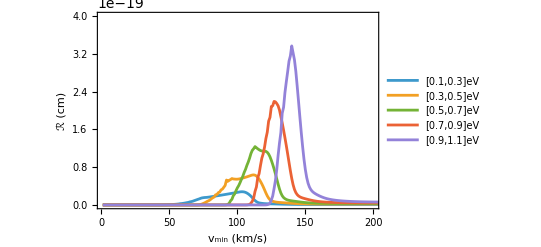

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M1_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
3.3 10^-19*cm
```

1.66667×10^-14

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_10MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_10MeV_q=0_5bins.pdf

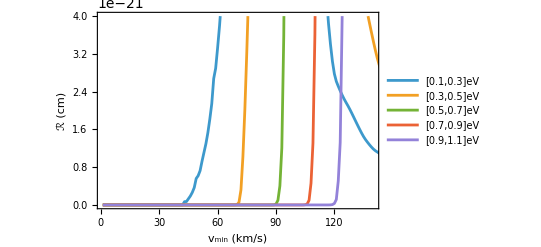

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,140},{0,4 10^-21}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_10MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_10MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M1.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"},PlotLegends->{"[0.1, 0.2]eV","[0.2, 0.3]eV","[0.3, 0.4]eV","[0.4, 0.5]eV","[0.5, 0.6]eV","[0.6, 0.7]eV","[0.7, 0.8]eV","[0.8, 0.9]eV","[0.9, 1.0]eV","[1.0, 1.1]eV",LegendLayout->{"Column",2}}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M1.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)},PlotLegends→{[0.1, 0.2]eV,[0.2, 0.3]eV,[0.3, 0.4]eV,[0.4, 0.5]eV,[0.5, 0.6]eV,[0.6, 0.7]eV,[0.7, 0.8]eV,[0.8, 0.9]eV,[0.9, 1.0]eV,[1.0, 1.1]eV,LegendLayout→{Column,2}}]

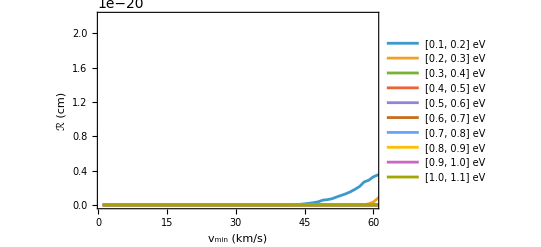

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_10MeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,60},{0,2.2 10^-20}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_10MeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][10 MeV][1,800] * Alexp
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M1_Ko.csv"],vals]
```

{911015.,1.80806×10^6,2.62891×10^6,3.43433×10^6,4.14207×10^6}

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M1_Ko.csv

```mathematica
Alexp
```

1.84056×10^49

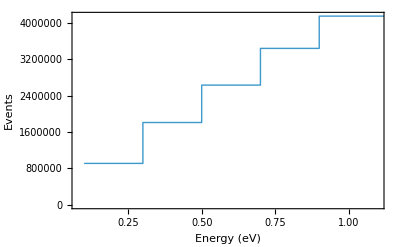

```mathematica
stepData1=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
ListStepPlot[stepData1,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

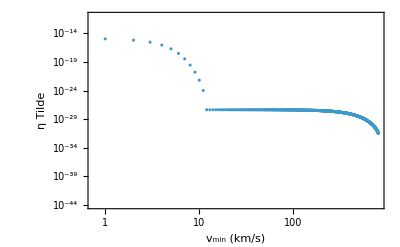

```mathematica
ListPlot[Table[
ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps]*cm+ηtb[1000 MeV][vm kps][2.441876042996079 kps, 11.2 kps] * cm,{vm, 1 , 800 }],
PlotStyle->Thick,
Frame->True,
FrameLabel->{"v_min (km/s)","η Tilde"},
PlotRange->{All,{10^-44, 10^-11}}, 
ScalingFunctions->{"Log","Log"}]
```

```mathematica
Alexp
```

1.84056×10^49

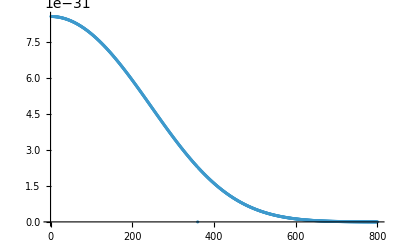

```mathematica
ListPlot[Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }]]
```

```mathematica
Export[FileNameJoin[Direc,"etaTilde_M1.h5"],Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }]]
Export[FileNameJoin[Direc,"etaTilde_M1.csv"],Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }]]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/etaTilde_M1.h5

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/etaTilde_M1.csv

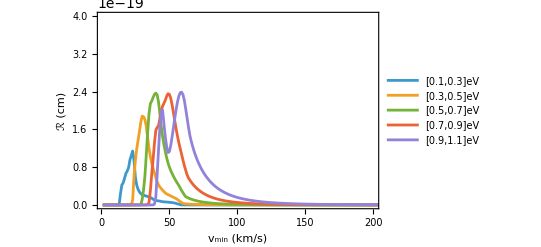

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M2_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_100MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_100MeV_q=0_5bins.pdf

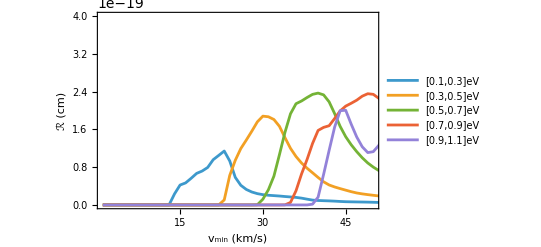

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_100MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_100MeV_q=0_5bins_ZOOMED.pdf

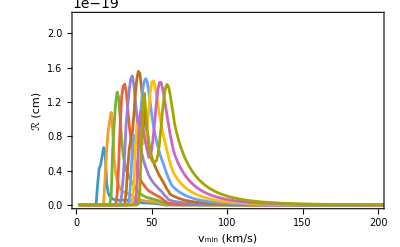

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M2.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"}]
```

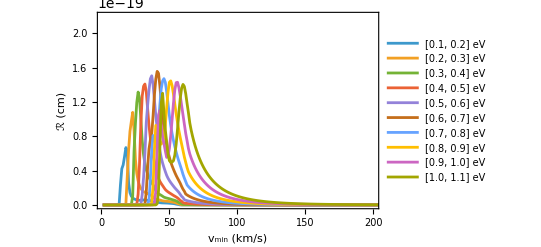

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

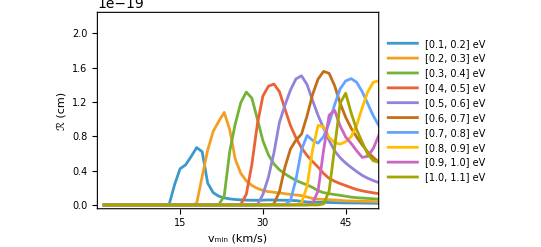

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.26,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

```mathematica
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf",%319,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_100MeV_q=0_SHM.pdf

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][100 MeV][1,800] * Alexp
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M2_Ko.csv"],vals]
```

{104460.,215451.,320672.,422728.,522606.}

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M2_Ko.csv

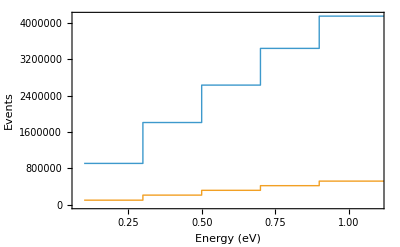

```mathematica
stepData2=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
ListStepPlot[{stepData1,stepData2},PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

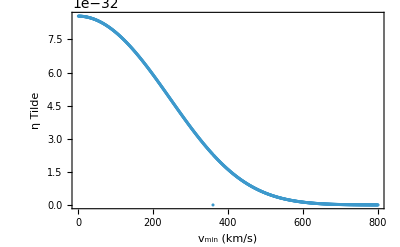

```mathematica
ListPlot[Table[ηth[100 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

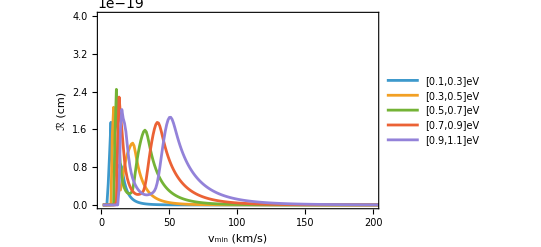

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R5_q0M3_Ko.h5"],{"Datasets","Dataset1"}];
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,200},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins.pdf

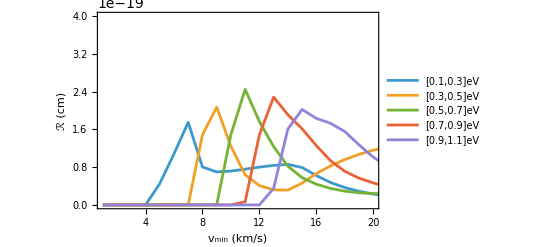

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,20},{0,4 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1,0.3]eV","[0.3,0.5]eV","[0.5,0.7]eV","[0.7,0.9]eV","[0.9,1.1]eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.28,0.75}]]]
```

```mathematica
Export[FileNameJoin[Direc,"results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins_ZOOMED.pdf"],curlyRPlot,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/curlyRplots/curlyR_TES_1000MeV_q=0_5bins_ZOOMED.pdf

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R10_q0M3.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistAl /cm,PlotRange->{{1, 200}, {0, 2.2 10^-19}}, Frame -> True, FrameLabel->{"v_min (km/s)", "ℛ (cm)"}]
```

Import::nffil: File /Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Al_R10_q0M3.h5 not found during Import.

ListLinePlot::lpn: 0.0000198 $Failed is not a list of numbers or pairs of numbers.

ListLinePlot[0.0000198 $Failed,PlotRange→{{1,200},{0,2.2×10^-19}},Frame→True,FrameLabel→{v_min (km/s),ℛ (cm)}]

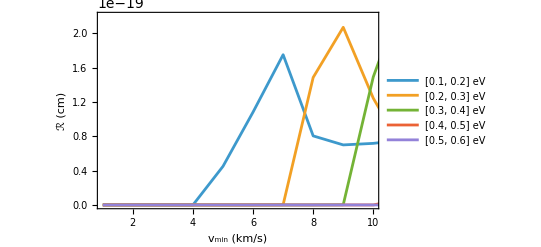

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM_Zoomed.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,10},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.27,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM_Zoomed.pdf",curlyRPlot,"PDF"]
```

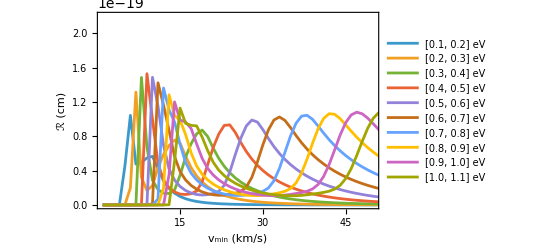

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistAl/cm,PlotRange->{{1,50},{0,2.2 10^-19}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","TES: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.1, 0.2] eV","[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.72,0.75}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_TES_1GeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminAl5[CRlistAl, ηtilde][1000 MeV][1,800] * Alexp
Export[FileNameJoin[Direc,"Events/Al_Events5_SHM_q0M3_Ko.csv"],vals]
```

{10566.8,21257.9,32061.8,42338.3,52451.3}

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/Events/Al_Events5_SHM_q0M3_Ko.csv

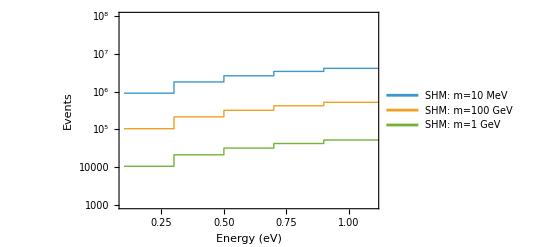

```mathematica
stepData3=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsAl,vals}],1];
EventsSHM = ListStepPlot[{stepData1, stepData2, stepData3},PlotStyle->Thick,Frame->True,
FrameLabel->{{"Events", None}, {"Energy (eV)","TES events for 8200 ng・month"}},
PlotRange->{{0.1,1.1},{10^3,10^8}},
PlotLegends->Placed[LineLegend[{"SHM: m=10 MeV","SHM: m=100 GeV","SHM: m=1 GeV"},LegendLayout->{"Column",1}, LabelStyle->Directive[8]],Scaled[{0.15,0.85}]],
ScalingFunctions->"Log"]
```

```mathematica
kps
```

3.32323×10^-6

```mathematica
Export[FileNameJoin[Direc,"results/Events/Events_TES_SHM_q=0_5bins.pdf"],EventsSHM,"PDF"]
```

/Users/koichiro/Dropbox/GraduateResearch/QSensor_Test/HALOIND/results/Events/Events_TES_SHM_q=0_5bins.pdf

```mathematica
ListPlot[Table[ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps] * cm,{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

```mathematica
(*MKID*)
(* Use imported data *)
```

```mathematica
binsTiN={{0.2,0.3},{0.3,0.4},{0.4,0.5},{0.5,0.6},{0.6,0.7},{0.7,0.8},{0.8,0.9},{0.9,1.0},{1.0,1.1}};
```

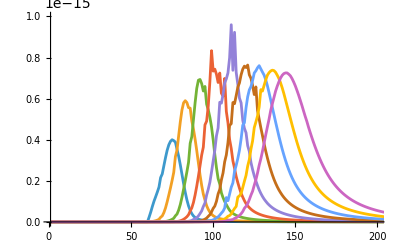

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M1.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

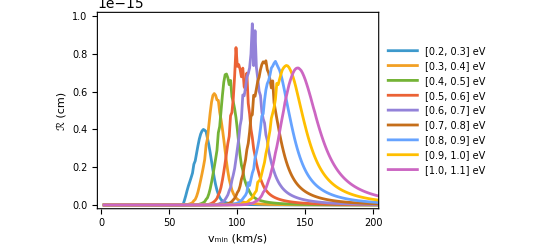

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_10MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=10 MeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",1}, LabelStyle->Directive[8]],Scaled[{0.15,0.52}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_10MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][10 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M1.csv"],vals]
```

{1.70213×10^-50,2.55884×10^-50,3.22273×10^-50,3.97149×10^-50,4.67044×10^-50,5.15322×10^-50,5.68153×10^-50,6.18928×10^-50,6.61773×10^-50}

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/TiN_Events10_q0M1.csv

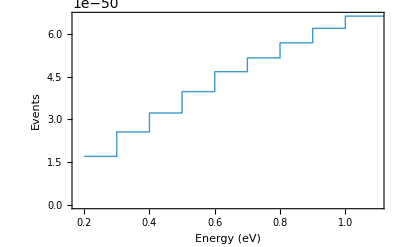

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

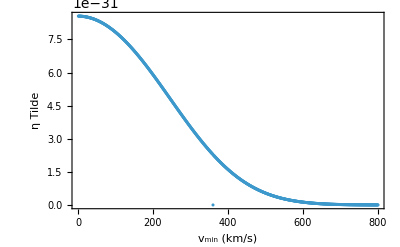

```mathematica
ListPlot[Table[ηth[10 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

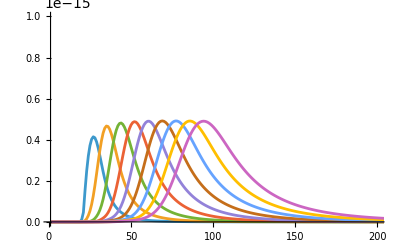

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M2.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

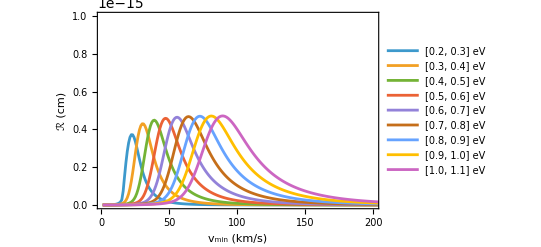

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_100MeV_q=0_SHM.pdf

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=100 MeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_100MeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][100 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M2.csv"],vals]
```

{1.64989×10^-51,2.53733×10^-51,3.23167×10^-51,3.90337×10^-51,4.54904×10^-51,5.16518×10^-51,5.74863×10^-51,6.29662×10^-51,6.80691×10^-51}

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/HALOIND/TiN_Events10_q0M2.csv

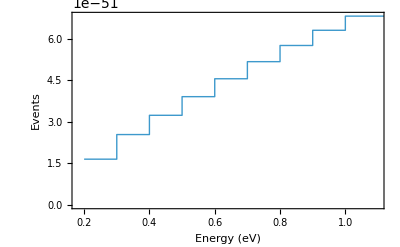

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
ListPlot[Table[ηth[100 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

-Graphics-

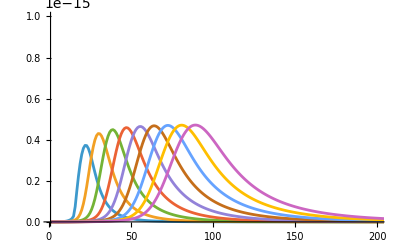

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R10_q0M3.h5"],{"Datasets","Dataset1"}];
ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}}]
```

```mathematica
curlyRPlot = ListLinePlot[CRlistTiN,PlotRange->{{1, 200}, {0, 1 10^-15}},Frame->True,FrameLabel->{{"ℛ (cm)", None}, {"\!\(\*SubscriptBox[\(v\), \(min\)]\) (km/s)","MKID: m=1 GeV"}},PlotLegends->Placed[LineLegend[{"[0.2, 0.3] eV","[0.3, 0.4] eV","[0.4, 0.5] eV","[0.5, 0.6] eV","[0.6, 0.7] eV","[0.7, 0.8] eV","[0.8, 0.9] eV","[0.9, 1.0] eV","[1.0, 1.1] eV"},LegendLayout->{"Column",2}, LabelStyle->Directive[8]],Scaled[{0.73,0.73}]]]
Export["/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_1GeV_q=0_SHM.pdf",curlyRPlot,"PDF"]
```

-Graphics-

/Users/koichiro/Dropbox/GraduateResearch/quantumSensor/KO_test/Main_KO/results/curlyR_MKID_1GeV_q=0_SHM.pdf

```mathematica
vals = RvminTiN[CRlistTiN, ηtilde][1000 MeV][1,800]
Export[FileNameJoin[Direc,"TiN_Events10_q0M3.csv"],vals]
```

```mathematica
stepData=Flatten[MapThread[{{#1[[1]],#2},(*左端->val*){#1[[2]],#2}    (*右端->val*)}&,{binsTiN,vals}],1];
ListStepPlot[stepData,PlotStyle->Thick,Frame->True,FrameLabel->{"Energy (eV)","Events"},PlotRange->All]
```

```mathematica
ListPlot[Table[ηth[1000 MeV][vm kps][230 kps,240 kps, 600 kps],{vm, 1 , 800 }],PlotStyle->Thick,Frame->True,FrameLabel->{"v_min (km/s)","η Tilde"},PlotRange->All]
```

## Data for minimization

### defined

```mathematica
(* data from differential intervals *)
```

```mathematica
SampleInt[f_][Ev1_,dEv_,n_]:=Table[NIntegrate[f[Ev ],{Ev,Ev1+m*dEv,Ev1+dEv+m*dEv}],{m,0,n-1,1}]
```

```mathematica
(* depends on the vmin step used in the response function calculation *)
(* default 1 km/s *)
```

```mathematica
vmlist=Table[v kps,{v,1,800,1}];
```

```mathematica
(* trimming 0 *)
```

```mathematica
(* format *)
```

DropCR0[Data matrix][min v, interval size, # of intervals]

```mathematica
DropCR0[Rmat_][vi_,dv_,ndv_]:=Module[{a,c,Rmatdv,tmInt,tmRdv},
Rmatdv={};
tmInt=0;
tmRdv=0;
a=0;
c=0;
For[i=1,i<=Length[Rmat],i++,
tmInt=LIntpl1D[vmlist,Rmat[[i]]];
tmRdv=SampleInt[tmInt][vi,dv,ndv];
AppendTo[Rmatdv,tmRdv]
];
While[a==0,
c=c+1;
a=Rmatdv[[1,c]];
];
Print[(c-1)"columns dropped"];
Drop[Rmatdv,None,c-1]
]
```

```mathematica
(* Expected events *)
```

```mathematica
Rvmin[Rmat_,eta_][md_][v1_,v2_]:=Table[Sum[eta[md][vm kps]*Rmat[[i]][[vm]]*kps,{vm,v1,v2}],{i,1,9}]
```

```mathematica
RvminAl5[Rmat_,eta_][md_][v1_,v2_]:=Table[Sum[eta[md][vm kps]*Rmat[[i]][[vm]],{vm,v1,v2}],{i,1,5}]
RvminTiN5[Rmat_,eta_][md_][v1_,v2_]:=Table[Sum[eta[md][vm kps]*Rmat[[i]][[vm]],{vm,v1,v2}],{i,1,9}]
```

```mathematica
RvminAl[Rmat_,eta_][md_][v1_,v2_]:=Table[Sum[eta[md][vm kps]*Rmat[[i]][[vm]]*kps,{vm,v1,v2}],{i,1,10}]
RvminTiN[Rmat_,eta_][md_][v1_,v2_]:=Table[Sum[eta[md][vm kps]*Rmat[[i]][[vm]]*kps,{vm,v1,v2}],{i,1,9}]
```

```mathematica
RvminAl[CRlistAl, ηtilde][1000 MeV][1,800] * Alexp
```

```mathematica
RvminTiN[CRlistTiN, ηtilde][1000 MeV][1,800] * TiNexp
```

### data generating

Repeat for other parameters

```mathematica
(* Use imported data *)
```

```mathematica
CRlisAlq0M1=Import[FileNameJoin[Direc,"Al_R10_q0M1.h5"],{"Datasets","Dataset1"}];
```

#### Matrix

```mathematica
(* integrating and trimming *)
```

```mathematica
(* use different interval if needed *)
```

```mathematica
CRmatAlq0M1=Round[DropCR0[CRlisAlq0M1][2 kps,2kps,100]*Alexp/10^24,0.01]
```

```mathematica
(* 10^24 is a random constant, choose a different rounding if needed *)
```

```mathematica
(* Export *)
```

```mathematica
Export[FileNameJoin[Direc,"CRmatAlq0M1.csv"],CRmatAlq0M1]
```

#### Events

```mathematica
(* ηtilde for events *)
```

```mathematica
ηtilde[mχ_][vm_]:=ηth[mχ][vm][v0,ve,vesc]
```

```mathematica
(* this is for Halo only, use different v0, ve, vesc for other distribution *)
```

```mathematica
datηthAlq0M1=Round[Rvmin[CRlisAlq0M1,ηtilde][100 MeV][2,200]*Alexp,1]*10^13
```

```mathematica
(* 10^13 is a random constant, choose a different rounding if needed *)
```

```mathematica
(* Export *)
```

```mathematica
Export[FileNameJoin[Direc,"Event10EtaHaloMatAlq0M1.csv"],datηthAlq0M1]
```

## Minimization

```mathematica
(* this part should be done in python *)
```

```mathematica
(* if we want to use mathematica *)
```

### defined

```mathematica
(* minimization *)
```

```mathematica
etaMinimize[dRmat_,Ndata_]:=Module[{m,n,cons1,cons2,etamin,etadat},
{m,n}=Dimensions[dRmat];
cons1 = Table[y[j + 1] ≤ y[j], {j, 1, n - 1}];
cons2 = Table[0<=y[j], {j, 1, n}];
etamin=NMinimize[{Sum[(Sum[dRmat[[i,j]]*y[j],{j,1,n}]-Ndata[[i]])^2/Ndata[[i]],{i,1,m}],cons1, cons2},Table[y[j],{j,1,n}], Method->"NonlinearInteriorPoint",PrecisionGoal->4];
etadat=Table[y[j],{j,1,n}]*cm/.Delete[etamin,1];
etadat[[1]]
]
```

```mathematica
(* Step plot *)
```

```mathematica
(* format *)
```

datStepPlot[eta data][min v, max v, v step][trimmed column #]

```mathematica
datStepPlot[etalis_][v1_,v2_,dv_][d_]:=Module[{pdata,ele1,ηtdata,vmlis,ind},
vmlis=Drop[Table[vm,{vm,v1,v2,dv}],d];
pdata=Transpose[{vmlis,etalis}]; 
ele1=pdata[[1,2]];
ind=1;
ηtdata={};
While[ind<=Length[pdata],
If[pdata[[ind]][[2]]==ele1,
ele1=pdata[[ind]][[2]];AppendTo[ηtdata,pdata[[ind]]],
ele1=pdata[[ind]][[2]];AppendTo[ηtdata,{pdata[[ind-1]][[1]],pdata[[ind]][[2]]}];AppendTo[ηtdata,pdata[[ind]]]];
ind=ind+1;
];
ηtdata
]
```

### 5 bin example

```mathematica
(* Import matrix *)
```

```mathematica
CRlistAl=Import[FileNameJoin[Direc,"Al_R_q0M2.h5"],{"Datasets","Dataset1"}];
(*CRlistAl = Import[FileNameJoin[Direc,"Al_R10_q0M2.h5"],{"Datasets","Dataset1"}] * 10^49;*)
```

```mathematica
CRlistAl
```

```mathematica
CRlistTiN=Import[FileNameJoin[Direc,"TiN_R_q0M2.h5"],{"Datasets","Dataset1"}];
```

```mathematica
(* Expected data using halo *)
```

```mathematica
dat1Alq0=Round[Rvmin[CRlistAl,ηtilde][100 MeV][2,200]*12,1]*10^13
dat1Alq0=Round[Rvmin[CRlistAl,ηtilde][100 MeV][1,800]*12,1]*10^13
```

```mathematica
dat1TiNq0=Round[Rvmin[CRlistTiN,ηtilde][100 MeV][2,270]*TiNexp,1]*10^12
```

```mathematica
(* Matrix *)
```

```mathematica
CRmat1Alq0=Round[DropCR0[CRlistAl][2 kps,2kps,100]*12/10^24,0.01];
CRmat1TiNq0=Round[DropCR0[CRlistTiN][2 kps,2kps,135]*TiNexp/10^25,0.01];
```

```mathematica
(* Minimization *)
```

```mathematica
datηAl=etaMinimize[CRmat1Alq0,dat1Alq0]/10^10
ListPlot[datηAl]
```

```mathematica
datηTiN=etaMinimize[CRmat1TiNq0,dat1TiNq0]/10^10
ListPlot[datηTiN]
```

```mathematica
(* create step plot *)
```

```mathematica
datηAlStep=datStepPlot[datηAl /10^10*12/10^24 * cm][2,200,2][5];
```

```mathematica
datηTiNStep=datStepPlot[datηTiN][2,270,2][8];
```

```mathematica
pηtAl1q0=ListLinePlot[datηAlStep,ScalingFunctions->{"Log"}]
```

```mathematica
pηtTiN1q0=ListLinePlot[datηTiNStep,PlotStyle->ColorData[116,2],ScalingFunctions->{"Log"}]
```